```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/AuctionExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
randommm = Take[q, {1, Length[q], 100}];
lrandommm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{7117.,6955.,6606.,6261.,6131.,6947.,5811.,6112.,6933.,7149.,7218.,6524.,6614.,6561.,6438.,6537.,6536.,6629.,6708.,6521.,6583.,6904.,6365.,5912.,6506.,6906.,6567.,6915.,5742.,6984.,6293.,6559.,6439.,5356.,6619.,7015.,5912.,6893.,6714.,7050.,5975.,5427.,6761.,7434.,6122.,6463.,6366.,7094.,6643.,6311.,6822.,6061.,6512.,6233.,5672.,7774.,6826.,6138.,5982.,6372.,6187.,5649.,6225.,6851.,6642.,5966.,6590.,6631.,6421.,6745.,6552.,6391.,7018.,6924.,6526.,7333.,6666.,5237.,7053.,5780.,6371.,7022.,5838.,5221.,6410.,6849.,6001.,6878.,5508.,7457.,6089.,5959.,5910.,6800.,6528.,5833.,5897.,6840.,6720.,6166.}

{6158.,8154.,7079.,5833.,5498.,7021.,7835.,5741.,7181.,6849.,6799.,6128.,7149.,6711.,4874.,8008.,5895.,8317.,5491.,6194.,7382.,6397.,7322.,6127.,7383.,7359.,7743.,8867.,6452.,7541.,6446.,6652.,6649.,6969.,7374.,7608.,7280.,6890.,6182.,7793.,7239.,6721.,8460.,6424.,5687.,7508.,5608.,7066.,6332.,6408.,8072.,6844.,6758.,7820.,5765.,6262.,6664.,5720.,6292.,7306.,6865.,5866.,6378.,6927.,6465.,6298.,7074.,6385.,5726.,6135.,8118.,6793.,8023.,6555.,7953.,5510.,5219.,6672.,6773.,7614.,6272.,8235.,6635.,6792.,7116.,7624.,6675.,6862.,6959.,6431.,7340.,6679.,6500.,7022.,7396.,7872.,6353.,6720.,7137.,7694.}

{5661.,5707.,5617.,7057.,6376.,6657.,7066.,6896.,6287.,5816.,6428.,6635.,6042.,6977.,6298.,5812.,5408.,6390.,6394.,6308.,5517.,5851.,5364.,6144.,6550.,7011.,7102.,5830.,6131.,6244.,6830.,7311.,6950.,6934.,6827.,6281.,6471.,6663.,7227.,6168.,6033.,6050.,6364.,6466.,5915.,6636.,6083.,6053.,6402.,6144.,7697.,5931.,6624.,6463.,6223.,5897.,6268.,6448.,6018.,6115.,6159.,6858.,6056.,7167.,5993.,6351.,7034.,6553.,6302.,6673.,7116.,7368.,6268.,6846.,6136.,7024.,6438.,6397.,6708.,6222.,6116.,7090.,7042.,5817.,5633.,5735.,6959.,7443.,6426.,6176.,5823.,6098.,6235.,6173.,6603.,5650.,6129.,8141.,6451.,7085.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{5724.,7209.,5699.,5704.,6207.,6843.,6475.,6644.,6421.,7151.,6266.,6685.,6232.,6277.,6885.,5655.,7106.,6178.,6167.,6765.,6225.,5904.,6145.,7053.,7055.,6091.,5760.,6929.,6746.,6150.,7080.,6766.,7144.,6072.,6848.,7130.,6204.,6257.,5699.,7011.,6121.,6947.,7213.,6469.,6101.,6678.,5399.,6450.,7595.,5562.,6017.,7490.,6828.,6206.,6478.,6842.,6611.,7021.,6504.,7320.,6700.,6494.,7360.,5760.,6607.,6031.,6745.,7587.,6475.,6257.,7203.,6975.,6488.,6469.,6041.,5597.,6846.,6564.,6607.,5997.,6832.,6272.,6309.,6246.,5752.,6479.,6569.,6001.,6614.,6353.,7636.,7310.,6544.,7135.,6455.,6568.,6378.,6252.,6263.,6755.}

{6269.,5413.,6155.,5581.,6071.,6384.,5649.,8069.,7247.,5067.,5329.,6072.,6311.,6247.,5811.,6043.,6303.,5955.,5830.,6404.,5892.,6218.,7032.,5617.,6030.,6775.,6894.,5498.,5945.,7094.,6995.,7063.,6070.,5977.,6218.,5618.,7066.,6703.,6104.,6008.,6344.,6846.,7197.,5750.,6674.,6313.,6839.,6782.,7319.,6115.,6755.,6619.,6767.,6054.,6261.,6971.,5733.,5208.,5944.,7075.,6293.,6715.,7360.,6413.,6539.,6951.,6505.,6246.,6636.,6232.,6945.,5701.,5899.,6128.,6631.,6296.,6198.,6433.,5512.,7219.,6465.,5797.,5588.,6385.,6563.,6561.,6717.,6443.,5714.,5894.,6345.,5969.,6512.,6395.,6027.,6515.,6379.,6080.,6670.,6800.}

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{6439.,5568.,5890.,7121.,5425.,6033.,6184.,6141.,6156.,6728.,6396.,5612.,7350.,6017.,6587.,6618.,7412.,6082.,6287.,7755.,7094.,6373.,6072.,6122.,6497.,6438.,5936.,6771.,6415.,6838.,5557.,7651.,6926.,6340.,6089.,6220.,5755.,7519.,6369.,5888.,6288.,6972.,6055.,5922.,7192.,6071.,6952.,6459.,6708.,6651.,5850.,5338.,6695.,5540.,6848.,6707.,6202.,6100.,6916.,7025.,5420.,5377.,6388.,5871.,5414.,6451.,6063.,6440.,5289.,6426.,5562.,7057.,6000.,6634.,6629.,7219.,5347.,6125.,6521.,6010.,6239.,6796.,7054.,6593.,5569.,6243.,6574.,6852.,6095.,5953.,6083.,6711.,7274.,6886.,6244.,6634.,5754.,6619.,5611.,5973.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,7117.},{1,6955.},{1,6606.},{1,6261.},{1,6131.},{1,6947.},{1,5811.},{1,6112.},{1,6933.},{1,7149.},{1,7218.},{1,6524.},{1,6614.},{1,6561.},{1,6438.},{1,6537.},{1,6536.},{1,6629.},{1,6708.},{1,6521.},{1,6583.},{1,6904.},{1,6365.},{1,5912.},{1,6506.},{1,6906.},{1,6567.},{1,6915.},{1,5742.},{1,6984.},{1,6293.},{1,6559.},{1,6439.},{1,5356.},{1,6619.},{1,7015.},{1,5912.},{1,6893.},{1,6714.},{1,7050.},{1,5975.},{1,5427.},{1,6761.},{1,7434.},{1,6122.},{1,6463.},{1,6366.},{1,7094.},{1,6643.},{1,6311.},{1,6822.},{1,6061.},{1,6512.},{1,6233.},{1,5672.},{1,7774.},{1,6826.},{1,6138.},{1,5982.},{1,6372.},{1,6187.},{1,5649.},{1,6225.},{1,6851.},{1,6642.},{1,5966.},{1,6590.},{1,6631.},{1,6421.},{1,6745.},{1,6552.},{1,6391.},{1,7018.},{1,6924.},{1,6526.},{1,7333.},{1,6666.},{1,5237.},{1,7053.},{1,5780.},{1,6371.},{1,7022.},{1,5838.},{1,5221.},{1,6410.},{1,6849.},{1,6001.},{1,6878.},{1,5508.},{1,7457.},{1,6089.},{1,5959.},{1,5910.},{1,6800.},{1,6528.},{1,5833.},{1,5897.},{1,6840.},{1,6720.},{1,6166.}}

{{2,6158.},{2,8154.},{2,7079.},{2,5833.},{2,5498.},{2,7021.},{2,7835.},{2,5741.},{2,7181.},{2,6849.},{2,6799.},{2,6128.},{2,7149.},{2,6711.},{2,4874.},{2,8008.},{2,5895.},{2,8317.},{2,5491.},{2,6194.},{2,7382.},{2,6397.},{2,7322.},{2,6127.},{2,7383.},{2,7359.},{2,7743.},{2,8867.},{2,6452.},{2,7541.},{2,6446.},{2,6652.},{2,6649.},{2,6969.},{2,7374.},{2,7608.},{2,7280.},{2,6890.},{2,6182.},{2,7793.},{2,7239.},{2,6721.},{2,8460.},{2,6424.},{2,5687.},{2,7508.},{2,5608.},{2,7066.},{2,6332.},{2,6408.},{2,8072.},{2,6844.},{2,6758.},{2,7820.},{2,5765.},{2,6262.},{2,6664.},{2,5720.},{2,6292.},{2,7306.},{2,6865.},{2,5866.},{2,6378.},{2,6927.},{2,6465.},{2,6298.},{2,7074.},{2,6385.},{2,5726.},{2,6135.},{2,8118.},{2,6793.},{2,8023.},{2,6555.},{2,7953.},{2,5510.},{2,5219.},{2,6672.},{2,6773.},{2,7614.},{2,6272.},{2,8235.},{2,6635.},{2,6792.},{2,7116.},{2,7624.},{2,6675.},{2,6862.},{2,6959.},{2,6431.},{2,7340.},{2,6679.},{2,6500.},{2,7022.},{2,7396.},{2,7872.},{2,6353.},{2,6720.},{2,7137.},{2,7694.}}

{{3,5661.},{3,5707.},{3,5617.},{3,7057.},{3,6376.},{3,6657.},{3,7066.},{3,6896.},{3,6287.},{3,5816.},{3,6428.},{3,6635.},{3,6042.},{3,6977.},{3,6298.},{3,5812.},{3,5408.},{3,6390.},{3,6394.},{3,6308.},{3,5517.},{3,5851.},{3,5364.},{3,6144.},{3,6550.},{3,7011.},{3,7102.},{3,5830.},{3,6131.},{3,6244.},{3,6830.},{3,7311.},{3,6950.},{3,6934.},{3,6827.},{3,6281.},{3,6471.},{3,6663.},{3,7227.},{3,6168.},{3,6033.},{3,6050.},{3,6364.},{3,6466.},{3,5915.},{3,6636.},{3,6083.},{3,6053.},{3,6402.},{3,6144.},{3,7697.},{3,5931.},{3,6624.},{3,6463.},{3,6223.},{3,5897.},{3,6268.},{3,6448.},{3,6018.},{3,6115.},{3,6159.},{3,6858.},{3,6056.},{3,7167.},{3,5993.},{3,6351.},{3,7034.},{3,6553.},{3,6302.},{3,6673.},{3,7116.},{3,7368.},{3,6268.},{3,6846.},{3,6136.},{3,7024.},{3,6438.},{3,6397.},{3,6708.},{3,6222.},{3,6116.},{3,7090.},{3,7042.},{3,5817.},{3,5633.},{3,5735.},{3,6959.},{3,7443.},{3,6426.},{3,6176.},{3,5823.},{3,6098.},{3,6235.},{3,6173.},{3,6603.},{3,5650.},{3,6129.},{3,8141.},{3,6451.},{3,7085.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,5724.},{7,7209.},{7,5699.},{7,5704.},{7,6207.},{7,6843.},{7,6475.},{7,6644.},{7,6421.},{7,7151.},{7,6266.},{7,6685.},{7,6232.},{7,6277.},{7,6885.},{7,5655.},{7,7106.},{7,6178.},{7,6167.},{7,6765.},{7,6225.},{7,5904.},{7,6145.},{7,7053.},{7,7055.},{7,6091.},{7,5760.},{7,6929.},{7,6746.},{7,6150.},{7,7080.},{7,6766.},{7,7144.},{7,6072.},{7,6848.},{7,7130.},{7,6204.},{7,6257.},{7,5699.},{7,7011.},{7,6121.},{7,6947.},{7,7213.},{7,6469.},{7,6101.},{7,6678.},{7,5399.},{7,6450.},{7,7595.},{7,5562.},{7,6017.},{7,7490.},{7,6828.},{7,6206.},{7,6478.},{7,6842.},{7,6611.},{7,7021.},{7,6504.},{7,7320.},{7,6700.},{7,6494.},{7,7360.},{7,5760.},{7,6607.},{7,6031.},{7,6745.},{7,7587.},{7,6475.},{7,6257.},{7,7203.},{7,6975.},{7,6488.},{7,6469.},{7,6041.},{7,5597.},{7,6846.},{7,6564.},{7,6607.},{7,5997.},{7,6832.},{7,6272.},{7,6309.},{7,6246.},{7,5752.},{7,6479.},{7,6569.},{7,6001.},{7,6614.},{7,6353.},{7,7636.},{7,7310.},{7,6544.},{7,7135.},{7,6455.},{7,6568.},{7,6378.},{7,6252.},{7,6263.},{7,6755.}}

{{8,6269.},{8,5413.},{8,6155.},{8,5581.},{8,6071.},{8,6384.},{8,5649.},{8,8069.},{8,7247.},{8,5067.},{8,5329.},{8,6072.},{8,6311.},{8,6247.},{8,5811.},{8,6043.},{8,6303.},{8,5955.},{8,5830.},{8,6404.},{8,5892.},{8,6218.},{8,7032.},{8,5617.},{8,6030.},{8,6775.},{8,6894.},{8,5498.},{8,5945.},{8,7094.},{8,6995.},{8,7063.},{8,6070.},{8,5977.},{8,6218.},{8,5618.},{8,7066.},{8,6703.},{8,6104.},{8,6008.},{8,6344.},{8,6846.},{8,7197.},{8,5750.},{8,6674.},{8,6313.},{8,6839.},{8,6782.},{8,7319.},{8,6115.},{8,6755.},{8,6619.},{8,6767.},{8,6054.},{8,6261.},{8,6971.},{8,5733.},{8,5208.},{8,5944.},{8,7075.},{8,6293.},{8,6715.},{8,7360.},{8,6413.},{8,6539.},{8,6951.},{8,6505.},{8,6246.},{8,6636.},{8,6232.},{8,6945.},{8,5701.},{8,5899.},{8,6128.},{8,6631.},{8,6296.},{8,6198.},{8,6433.},{8,5512.},{8,7219.},{8,6465.},{8,5797.},{8,5588.},{8,6385.},{8,6563.},{8,6561.},{8,6717.},{8,6443.},{8,5714.},{8,5894.},{8,6345.},{8,5969.},{8,6512.},{8,6395.},{8,6027.},{8,6515.},{8,6379.},{8,6080.},{8,6670.},{8,6800.}}

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,6439.},{10,5568.},{10,5890.},{10,7121.},{10,5425.},{10,6033.},{10,6184.},{10,6141.},{10,6156.},{10,6728.},{10,6396.},{10,5612.},{10,7350.},{10,6017.},{10,6587.},{10,6618.},{10,7412.},{10,6082.},{10,6287.},{10,7755.},{10,7094.},{10,6373.},{10,6072.},{10,6122.},{10,6497.},{10,6438.},{10,5936.},{10,6771.},{10,6415.},{10,6838.},{10,5557.},{10,7651.},{10,6926.},{10,6340.},{10,6089.},{10,6220.},{10,5755.},{10,7519.},{10,6369.},{10,5888.},{10,6288.},{10,6972.},{10,6055.},{10,5922.},{10,7192.},{10,6071.},{10,6952.},{10,6459.},{10,6708.},{10,6651.},{10,5850.},{10,5338.},{10,6695.},{10,5540.},{10,6848.},{10,6707.},{10,6202.},{10,6100.},{10,6916.},{10,7025.},{10,5420.},{10,5377.},{10,6388.},{10,5871.},{10,5414.},{10,6451.},{10,6063.},{10,6440.},{10,5289.},{10,6426.},{10,5562.},{10,7057.},{10,6000.},{10,6634.},{10,6629.},{10,7219.},{10,5347.},{10,6125.},{10,6521.},{10,6010.},{10,6239.},{10,6796.},{10,7054.},{10,6593.},{10,5569.},{10,6243.},{10,6574.},{10,6852.},{10,6095.},{10,5953.},{10,6083.},{10,6711.},{10,7274.},{10,6886.},{10,6244.},{10,6634.},{10,5754.},{10,6619.},{10,5611.},{10,5973.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem,alrandommm], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 5 | 1.72763×10^7 | 3.45527×10^6 | 10.4815 | 1.1756×10^-9
Error | 594 | 1.95814×10^8 | 329654. |  | 
Total | 599 | 2.13091×10^8 |  |  | ,CellMeans→All | 6488.49
Model[1] | 6472.14
Model[2] | 6839.5
Model[3] | 6415.62
Model[7] | 6519.4
Model[8] | 6332.64
Model[10] | 6351.62,PostTests→{Model→Tukey | {{1,2},{2,3},{2,7},{2,8},{2,10}}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.2,3635.02,4436.06,4604.06,4591.68,4509.97,4492.96,4453.63,4527.87,4518.18,4214.9,3753.03,3450.74,3536.43,3593.55,3714.22,3805.9,3887.94,3909.88,3939.4,3960.58,3920.23,3907.15,3883.87,3913.76,3905.86,3826.14,3813.94,3790.02,3792.49,3741.44,3758.24,3725.21,3690.29,3660.65,3730.93,3673.18,3703.8,3678.08,3701.01,3666.92,3697.72,3683.72,3709.02,3663.15,3629.33,3635.41,3656.06,3670.92,3614.93,3620.91,3578.38,3624.57,3619.03,3570.02,3591.52,3601.33,3609.88,3549.7,3585.67,3581.53,3547.14,3595.61,3583.18,3583.58,3527.12,3533.52,3539.38,3542.1,3520.92,3536.94,3510.11,3530.14,3502.28,3491.03,3489.2,3557.17,3591.29,3550.27,3571.6,3570.6,3549.36,3515.21,3506.17,3515.33,3531.09,3536.51,3495.69,3481.63,3513.37,3490.42,3500.58,3486.23,3497.67,3480.77,3483.67,3518.96,3486.44,3466.45,3488.3,3499.55,3438.21,3446.86,3481.81,3480.9,3471.12,3496.91,3485.73,3463.49,3475.57,3462.05,3447.04,3448.44,3461.42,3456.4,3521.99,3451.48,3446.32,3473.86,3500.37,3448.41,3485.54,3461.57,3490.1,3468.08,3491.23,3452.82,3397.1,3450.,3445.17,3445.44,3471.47,3459.43,3449.94,3476.51,3441.64,3456.47,3461.01,3414.75,3465.72,3437.25,3436.06,3447.58,3437.47,3444.39,3453.,3449.86,3438.36,3443.88,3460.74,3424.72,3450.13,3459.86,3419.22,3440.22,3438.38,3424.74,3434.33,3448.48,3446.54,3464.44,3472.93,3432.34,3429.92,3407.06,3442.91,3468.58,3404.16,3467.31,3473.95,3450.14,3438.47,3436.05,3412.51,3445.83,3448.63,3422.4,3448.4,3431.53,3391.11,3411.48,3420.27,3424.38,3455.76,3405.83,3388.18,3451.41,3437.01,3433.17,3433.13,3417.18,3429.3,3430.04,3407.45,3405.88,3403.9,3421.91,3419.09,3460.24,3414.75,3442.62,3453.73,3412.61,3449.31,3438.37,3431.52,3435.28,3426.38,3449.93,3389.66,3408.45,3410.54,3447.91,3420.68,3396.33,3407.96,3418.83,3409.14,3416.37,3453.29,3436.51,3475.6,3453.01,3417.06,3434.71,3429.66,3436.22,3434.77,3403.34,3402.95,3403.94,3441.13,3408.99,3423.27,3472.09,3425.4,3412.3,3389.89,3446.47,3393.32,3432.,3397.5,3411.75,3397.59,3403.86,3410.23,3402.13,3415.67,3435.17,3409.26,3395.,3418.91,3427.8,3429.06,3408.84,3439.25,3437.82,3402.38,3405.31,3426.84,3408.68,3413.42,3401.5,3409.43,3435.73,3408.12,3394.93,3410.31,3398.05,3410.74,3420.13,3423.18,3434.17,3401.83,3435.72,3413.66,3409.16,3408.52,3428.37,3417.31,3412.64,3411.8,3437.75,3416.19,3440.03,3394.18,3381.27,3426.49,3409.14,3426.55,3403.13,3388.17,3421.28,3424.78,3402.06,3408.56,3434.73,3423.25,3372.15,3436.56,3439.8,3982.8,4313.74,4316.57,4247.62,4226.11,4240.56,4272.85,4251.16,4225.88,4256.79,4222.47,4213.77,4233.62,4214.32,4185.65,4214.66,4202.5,4193.23,4222.56,4208.46,4198.58,4200.02,4216.85,4228.57,4206.59,4199.97,4210.13,4187.2,4218.5,4173.35,4166.37,4201.84,4194.78,4183.08,4194.61,4221.15,4219.76,4176.89,4174.42,4193.16,4243.39,4201.88,4231.7,4202.92,4180.79,4217.34,4189.38,4201.82,4156.51,4194.37,4179.17,4196.72,4203.81,4164.81,4178.85,4182.3,4192.13,4184.71,4176.54,4151.31,4222.36,4202.44,4182.2,4176.09,4166.16,4210.66,4202.62,4192.2,4165.99,4214.75,4177.71,4141.88,4174.09,4202.68,4198.14,4188.98,4187.26,4224.66,4191.82,4182.7,4158.26,4185.,4165.81,4199.72,4194.74,4186.13,4195.88,4205.2,4223.14,4246.74,4203.21,4162.86,4196.37,4215.38,4190.45,4171.91,4204.72,4207.54,4184.,4179.06,4210.86,4176.65,4174.32,4201.99,4202.38,4183.87,4187.76,4155.6,4199.07,4170.4,4224.44,4189.81,4174.28,4184.22,4213.9,4207.39,4145.92,4191.85,4195.21,4202.37,4229.21,4218.15,4198.43,4215.32,4175.51,4178.04,4205.53,4202.96,4200.9,4172.07,4209.75,4178.94,4178.46,4162.75,4187.55,4134.57,4195.07,4206.01,4231.56,4185.33,4203.35,4217.03,4204.22,4191.18,4173.38,4158.3,4156.37,4202.36,4192.82,4177.86,4198.22,4186.51,4207.02,4240.4,4204.23,4236.26,4222.,4217.25,4225.86,4229.5,4211.85,4218.32,4144.06,4152.08,4167.94,4187.36,4209.74,4234.09,4215.1,4215.98,4226.94,4205.72,4181.1,4200.48,4226.56,4217.22,4230.09,4207.48,4202.64,4212.89,4154.89,4166.56,4219.93,4187.4,4198.87,4192.3,4212.63,4195.13,4158.83,4192.42,4199.12,4249.05,4206.56,4170.72,4182.55,4223.53,4246.08,4168.44,4201.22,4211.24,3532.24,3412.37,3392.,3379.86,3392.4,3397.17,3391.32,3383.23,3383.99,3401.23,3391.34,3401.19,3423.59,3382.83,3404.59,3416.29,3400.66,3400.79,3370.9,3376.89,3410.94,3395.01,3384.5,3394.37,3370.56,3384.4,3395.87,3421.98,3366.04,3338.8,3390.18,3382.7,3402.58,3393.09,3385.58,3398.57,3371.77,3394.55,3407.4,3371.52,3403.57,3389.9,3408.05,3400.54,3394.96,3396.43,3393.44,3391.71,3375.32,3396.21,3396.54,3378.13,3384.64,3397.89,3392.38,3403.99,3405.21,3413.16,3389.61,3380.84,3443.08,3388.84,3379.13,3409.81,3407.4,3380.3,3394.17,3393.03,3389.92,3394.15,3385.61,3398.98,3443.91,3387.35,3416.82,3382.78,3386.54,3384.12,3402.56,3427.92,3385.3,3390.23,3410.26,3375.81,3401.9,3390.52,3382.57,3392.24,3409.18,3423.9,3423.94,3406.49,3369.15,3384.59,3387.86,3402.27,3398.12,3403.82,3435.3,3468.01,4470.46,5387.65,6054.09,6404.5,6620.18,6609.61,6413.08,6188.99,6168.48,6171.42,6178.56,6278.32,6417.17,6329.65,6223.32,6225.41,6215.22,6177.89,6232.37,6236.8,6235.02,6254.35,6232.25,6179.5,6161.55,6232.58,6295.72,6322.,6272.8,6209.58,6185.87,6217.55,6195.02,6223.44,6201.3,6277.51,6202.3,6195.08,6188.73,6255.98,6199.5,6265.87,6275.78,6222.2,6235.66,6163.78,6248.75,6218.96,6234.7,6266.57,6293.18,6291.43,6265.68,6215.37,6230.84,6207.59,6239.72,6244.59,6260.,6226.2,6273.13,6215.7,6255.76,6251.22,6192.21,6259.57,6264.52,6290.05,6283.93,6276.73,6257.42,6303.05,6320.1,6271.72,6305.74,6264.94,6274.02,6287.84,6256.59,6251.12,6232.92,6289.36,6268.58,6276.19,6280.9,6280.62,6156.02,6231.22,6259.01,6258.13,6254.66,6267.63,6273.52,6232.22,6285.42,6239.97,6244.7,6312.48,6246.21,6236.49,6259.23,6343.7,6284.65,6296.97,6324.53,6288.28,6262.44,6238.96,6238.13,6245.22,6225.43,6249.29,6246.02,6294.8,6258.19,6293.66,6289.53,6346.91,6323.44,6365.02,6285.11,6255.17,6257.75,6319.25,6260.95,6246.76,6277.44,6256.65,6238.92,6272.13,6287.56,6274.39,6333.47,6263.6,6260.41,6301.79,6287.77,6336.4,6313.33,6298.05,6285.34,6241.23,6302.2,6286.93,6336.03,6286.54,6238.52,6220.62,6229.26,6247.,6306.56,6285.61,6300.96,6333.23,6284.55,6309.13,6304.26,6300.56,6294.24,6342.57,6294.92,6267.46,6340.48,6309.71,6293.7,6300.1,6248.13,6301.38,6271.13,6299.25,6295.6,6261.8,6284.1,6336.13,6222.02,6318.55,6349.63,6319.22,6278.82,6296.65,6353.41,6272.34,6292.56,6384.76,6348.64,6300.85,6327.05,6279.08,6269.,6260.46,6275.88,6271.37,6291.32,6277.54,6297.02,6303.98,6299.86,6328.96,6319.31,6270.37,3781.75,3333.89,3394.38,3419.93,3374.49,3379.12,3412.75,3362.78,3385.37,3409.63,3420.08,3420.32,3408.06,3376.65,3374.11,3397.29,3411.05,3409.34,3393.89,3380.28,3394.75,3395.92,3409.25,3398.45,3368.81,3403.58,3381.63,3402.73,3395.27,3379.9,3372.62,3385.07,3397.49,3384.18,3385.75,3389.31,3419.02,3363.92,3402.56,3390.02,3404.12,3399.3,3411.99,3408.2,3387.77,3416.08,3396.32,3404.06,3355.85,3395.93,3393.44,3417.85,3385.34,3383.12,3395.21,3369.14,3372.7,3390.68,3371.83,3375.66,3389.41,3403.9,3350.52,3399.51,3373.67,3392.67,3404.52,3359.59,3369.61,3395.72,3396.7,3398.92,3400.68,3402.88,3406.21,3367.82,3362.09,3389.24,3378.15,3393.01,3393.59,3398.93,3363.49,3403.2,3398.76,3375.74,3368.36,3379.4,3388.29,3407.79,3407.84,3369.,3378.59,3388.25,3403.52,3365.36,3402.96,3363.84,3386.39,3443.44,3852.62,4175.25,4299.85,4190.35,4095.26,4141.16,4194.86,4205.85,4129.14,4146.09,4234.37,4179.72,4175.51,4181.85,4165.84,4183.07,4191.97,4188.63,4190.88,4171.67,4193.49,4144.7,4165.2,4147.01,4196.88,4217.6,4158.84,4173.4,4174.23,4167.16,4198.43,4184.88,4201.63,4205.66,4180.34,4178.7,4160.49,4157.55,4159.,4193.99,4177.15,4186.03,4185.81,4235.34,4181.8,4153.12,4161.53,4185.98,4156.69,4178.7,4147.19,4179.36,4199.69,4209.21,4163.59,4193.79,4177.77,4179.74,4212.51,4166.61,4199.57,4188.51,4208.81,4194.27,4229.97,4178.18,4180.42,4168.37,4172.85,4160.64,4233.26,4171.68,4176.75,4163.71,4173.97,4194.49,4155.62,4151.75,4198.28,4187.42,4177.39,4218.16,4263.55,4196.9,4204.55,4202.1,4170.53,4190.63,4185.88,4215.92,4196.49,4182.53,4178.71,4199.41,4188.04,4191.7,4211.89,4193.14,4170.19,4178.88,4195.56,4175.71,4154.34,4191.95,4230.03,4228.93,4155.1,4222.13,4205.36,4184.54,4180.53,4191.45,4192.1,4187.67,4165.34,4204.04,4222.44,4184.26,4187.98,4181.82,4184.68,4201.59,4211.99,4220.77,4190.24,4176.07,4169.32,4211.36,4207.84,4174.57,4201.62,4179.75,4191.23,4190.12,4191.14,4216.1,4170.53,4161.47,4244.17,4205.31,4161.39,4167.61,4193.28,4220.83,4234.24,4192.99,4151.13,4152.4,4169.36,4209.46,4184.97,4150.23,4131.77,4192.14,4215.6,4183.9,4189.81,4177.37,4169.82,4188.53,4160.53,4184.47,4156.36,4164.46,4197.68,4157.63,4199.97,4162.39,4175.65,4157.2,4167.88,4222.85,4185.5,4167.16,4164.52,4188.57,4177.11,4179.42,4152.79,4207.61,4186.33,4210.59,4146.92,4181.52,4212.9,4188.99,4155.12,4156.89,4227.45,4203.94,4190.53,4187.19,4164.4,4166.08,4178.53,4185.44,4184.25,4192.56,4170.1,4149.14,3502.61,3371.48,3386.57,3402.07,3399.27,3406.54,3370.47,3397.48,3415.58,3394.09,3387.29,3388.51,3399.28,3394.53,3429.84,3381.75,3372.59,3410.09,3407.12,3358.88,3413.18,3389.09,3392.68,3394.2,3366.91,3380.97,3383.35,3412.66,3380.8,3399.,3373.06,3374.99,3384.13,3388.04,3392.82,3381.65,3403.31,3395.51,3394.37,3387.19,3372.48,3383.59,3415.32,3397.84,3390.33,3386.96,3355.42,3379.24,3394.35,3390.01,3384.64,3396.61,3409.32,3368.31,3400.18,3401.84,3392.76,3382.08,3379.05,3371.94,3380.65,3391.48,3380.13,3373.68,3382.33,3401.87,3402.56,3400.92,3388.38,3396.14,3409.23,3393.55,3367.95,3368.99,3390.2,3408.63,3388.,3397.2,3410.32,3387.49,3382.55,3412.09,3363.13,3373.4,3378.87,3399.23,3391.33,3397.6,3394.61,3386.93,3383.7,3375.32,3357.23,3400.01,3382.88,3365.61,3393.33,3398.7,3394.17,3449.55,4391.24,5238.79,5911.62,6373.93,6691.63,6829.77,6723.2,6529.87,6286.51,6097.92,6114.27,6197.76,6336.98,6435.01,6435.27,6397.21,6249.4,6186.82,6238.12,6278.76,6294.56,6333.66,6372.6,6301.55,6311.21,6241.64,6276.52,6295.83,6323.8,6338.84,6336.48,6385.28,6292.78,6296.03,6368.13,6368.18,6377.77,6320.55,6331.5,6275.55,6265.85,6302.24,6324.31,6338.12,6404.87,6366.68,6350.04,6330.8,6361.1,6304.57,6315.28,6332.56,6291.17,6298.12,6337.36,6323.15,6322.77,6344.8,6338.66,6312.75,6338.38,6329.94,6333.64,6352.24,6336.32,6318.16,6327.12,6308.71,6289.52,6304.6,6272.15,6255.53,6287.1,6289.97,6292.23,6299.61,6312.86,6306.39,6325.46,6343.39,6258.85,6297.9,6315.22,6343.66,6359.07,6347.56,6376.8,6369.67,6358.39,6314.8,6296.83,6331.12,6355.81,6383.39,6355.44,6322.64,6286.7,6284.33,6322.21,6347.14,6375.97,6404.65,6341.24,6310.4,6338.02,6351.84,6401.82,6344.97,6289.53,6307.07,6323.92,6356.84,6272.97,6365.38,6284.3,6302.08,6299.98,6325.45,6265.97,6287.39,6293.96,6317.49,6351.68,6319.23,6213.14,6301.33,6354.69,6315.51,6292.88,6263.22,6289.74,6307.7,6323.73,6338.03,6304.41,6343.44,6310.76,6339.03,6320.68,6353.05,6354.4,6368.65,6296.69,6322.87,6340.04,6298.54,6381.59,6363.97,6372.39,6285.9,6262.46,6317.43,6350.29,6303.15,6294.03,6249.5,6332.01,6317.45,6357.92,6442.03,6293.08,6267.78,6271.34,6204.44,6276.7,6324.17,6311.26,6349.8,6324.98,6271.19,6324.11,6315.09,6287.22,6316.53,6337.21,6381.92,6334.,6307.26,6306.22,6312.27,6336.93,6325.92,6356.33,6342.26,6304.4,6270.86,6270.03,6319.87,6302.84,6343.4,6393.39,6396.69,6366.,6338.8,6298.82,6291.04,6349.27,6315.79,6289.76,6237.04,3745.98,3330.05,3412.,3421.02,3356.93,3400.69,3366.95,3368.8,3388.59,3385.66,3374.15,3374.04,3413.42,3378.42,3365.65,3399.95,3378.84,3347.42,3376.84,3377.41,3388.51,3412.49,3386.14,3384.35,3407.33,3375.39,3389.43,3381.6,3388.82,3371.45,3368.84,3399.15,3386.95,3383.33,3378.43,3382.21,3399.75,3378.77,3386.24,3403.,3397.31,3398.03,3397.21,3386.86,3403.44,3403.49,3379.85,3361.35,3382.67,3423.17,3404.21,3400.71,3373.29,3375.66,3411.91,3362.57,3372.02,3396.21,3359.29,3381.52,3384.9,3394.86,3377.96,3376.59,3388.39,3415.59,3387.58,3393.63,3377.33,3368.66,3364.61,3360.73,3389.29,3395.03,3376.67,3375.76,3358.09,3416.77,3398.91,3395.63,3377.41,3384.94,3397.19,3387.8,3383.35,3393.78,3377.32,3388.72,3387.5,3385.02,3367.73,3405.58,3391.3,3396.26,3372.87,3409.63,3400.31,3375.25,3411.42,3402.52,3872.73,4162.24,4315.97,4254.92,4171.41,4136.78,4234.64,4185.37,4180.49,4162.32,4166.51,4226.88,4221.77,4172.8,4174.02,4170.88,4174.27,4180.45,4181.07,4201.74,4187.83,4195.64,4185.3,4184.6,4183.52,4168.53,4176.8,4182.57,4179.26,4185.17,4206.52,4172.55,4176.47,4174.77,4201.46,4172.79,4160.46,4173.82,4201.72,4149.23,4146.,4166.69,4188.05,4186.18,4186.59,4201.17,4176.04,4192.82,4173.95,4208.79,4221.42,4192.06,4124.05,4174.24,4192.64,4186.98,4184.99,4166.03,4180.35,4228.34,4197.37,4192.5,4199.93,4181.43,4161.65,4191.08,4161.27,4227.37,4181.52,4159.02,4166.97,4157.34,4170.77,4201.99,4185.37,4158.78,4167.23,4169.25,4248.34,4201.23,4197.03,4158.92,4177.77,4199.96,4171.51,4187.93,4170.78,4153.78,4181.51,4169.26,4149.22,4236.61,4236.08,4177.83,4123.03,4126.85,4182.07,4184.13,4172.89,4161.03,4179.13,4189.94,4218.41,4209.13,4147.4,4195.34,4201.,4194.34,4156.92,4211.33,4221.13,4203.44,4196.34,4195.66,4180.8,4167.31,4171.21,4159.73,4200.79,4143.34,4167.61,4154.22,4184.01,4157.9,4162.38,4173.37,4164.06,4168.85,4191.89,4231.97,4181.35,4184.93,4158.42,4161.01,4199.91,4168.68,4229.9,4183.71,4182.21,4196.02,4195.99,4161.46,4146.38,4157.54,4205.65,4176.53,4179.67,4199.65,4155.88,4174.37,4215.03,4216.13,4166.14,4163.67,4201.92,4215.17,4204.66,4166.22,4165.79,4184.35,4216.02,4198.17,4193.02,4195.54,4175.55,4216.07,4212.63,4175.52,4127.59,4164.48,4170.21,4184.35,4210.,4165.33,4150.5,4117.89,4178.43,4129.26,4164.61,4174.31,4187.12,4192.18,4185.77,4147.47,4183.22,4166.19,4143.28,4178.01,4185.74,4145.67,4173.59,4169.75,4167.59,4206.68,4147.35,4168.1,4184.25,4163.8,4159.55,4162.85,3443.7,3374.01,3372.24,3392.32,3394.29,3382.67,3416.26,3380.18,3379.02,3405.87,3389.53,3379.67,3397.71,3354.49,3403.59,3374.68,3364.06,3379.4,3388.96,3398.13,3384.45,3408.16,3377.21,3373.36,3397.07,3353.97,3396.52,3392.58,3377.36,3365.23,3365.28,3373.5,3369.67,3373.86,3413.09,3398.26,3403.77,3365.5,3387.31,3384.,3366.97,3372.03,3397.48,3393.61,3388.12,3386.53,3425.18,3384.4,3396.62,3381.71,3383.12,3396.6,3376.08,3399.99,3375.13,3403.51,3416.93,3408.05,3394.05,3399.3,3368.79,3360.68,3406.07,3388.62,3378.82,3357.51,3385.97,3403.19,3379.23,3399.47,3364.33,3391.13,3386.31,3362.35,3403.85,3386.61,3375.61,3379.63,3377.67,3374.47,3364.69,3376.2,3383.47,3406.56,3371.77,3393.56,3416.15,3388.38,3384.45,3391.5,3400.37,3383.29,3372.21,3397.64,3401.79,3403.56,3412.78,3397.92,3401.94,3446.27,4419.9,5239.59,5873.44,6386.65,6632.16,6773.81,6733.22,6490.56,6232.41,6114.82,6115.,6231.87,6295.75,6359.86,6415.46,6427.96,6363.26,6321.6,6247.59,6201.52,6334.44,6390.34,6326.84,6324.45,6375.16,6324.02,6258.8,6281.18,6270.18,6251.21,6299.23,6335.42,6348.5,6330.74,6360.1,6323.39,6269.69,6335.92,6281.75,6344.23,6330.95,6338.3,6320.55,6292.44,6333.31,6300.57,6300.08,6293.37,6286.68,6318.73,6370.71,6294.72,6331.25,6319.51,6324.79,6303.92,6378.32,6315.77,6312.15,6322.93,6311.43,6353.71,6291.01,6295.04,6294.37,6256.5,6264.67,6322.08,6400.84,6358.94,6297.16,6398.44,6283.81,6300.79,6293.69,6348.61,6405.01,6375.87,6348.88,6345.19,6283.62,6356.15,6328.55,6335.57,6384.38,6356.31,6354.31,6349.36,6347.77,6277.39,6247.27,6322.64,6335.98,6374.37,6311.98,6303.83,6249.9,6291.85,6365.85,6329.3,6321.44,6344.1,6358.1,6385.94,6317.89,6279.74,6316.99,6317.73,6338.66,6369.32,6332.14,6310.,6297.45,6310.66,6289.27,6433.3,6381.28,6350.72,6389.19,6339.32,6298.68,6271.73,6300.22,6280.46,6340.51,6400.26,6416.79,6322.88,6326.46,6319.65,6338.8,6349.22,6334.2,6359.66,6332.18,6300.52,6282.82,6291.69,6321.95,6331.63,6287.12,6370.18,6328.09,6325.2,6264.09,6288.39,6324.53,6289.05,6343.05,6308.15,6286.87,6337.12,6322.91,6268.65,6312.11,6310.5,6279.89,6361.87,6320.76,6377.61,6362.08,6348.24,6391.64,6392.02,6339.96,6333.75,6337.56,6336.36,6261.07,6342.,6289.74,6346.54,6334.17,6301.87,6336.37,6360.3,6316.71,6352.55,6355.39,6373.05,6413.35,6377.71,6360.19,6353.2,6312.62,6279.91,6294.72,6302.48,6318.06,6339.35,6330.16,6333.61,6335.63,6312.62,6377.71,6258.17,6288.85,6370.03,6332.64},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

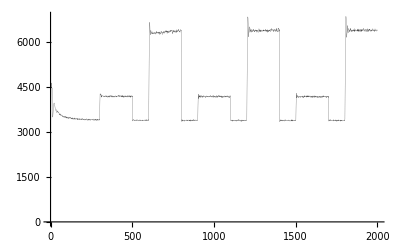

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2029.8, 3833.77, 5256.5, 6257.29, 6889.43, 7150.54, 7243.69, 7107.68, 7008.33, 6966.05, 6832.87, 6839.4, 6529.36, 6240.51, 5986.95, 5639.03, « 19 », 4456.45, 4489.65, 4502.28, 4496.67, 4423.88, 4484.37, 4436.23, 4398.73, 4369.48, 4350.76, 4293.52, 4253.29, 4165.99, 4127.44, 4147.43, « 1950 »}, « 2 », « 9 » → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.8,3833.77,5256.5,6257.29,6889.43,7150.54,7243.69,7107.68,7008.33,6966.05,6832.87,6839.4,6529.36,6240.51,5986.95,5639.03,5185.6,4796.66,4584.96,4485.63,4352.84,4356.16,4357.08,4334.77,4357.31,4322.02,4274.97,4311.28,4361.75,4391.29,4425.6,4401.14,4442.51,4476.72,4437.13,4456.45,4489.65,4502.28,4496.67,4423.88,4484.37,4436.23,4398.73,4369.48,4350.76,4293.52,4253.29,4165.99,4127.44,4147.43,4078.11,4121.12,4090.32,4042.47,4028.48,3977.87,3961.5,3925.5,3939.87,3899.86,3866.98,3868.27,3810.04,3810.11,3797.07,3814.44,3721.68,3813.65,3760.34,3721.48,3737.01,3691.5,3676.82,3659.44,3678.36,3670.05,3672.37,3675.96,3673.56,3635.82,3620.4,3630.81,3602.74,3633.94,3575.49,3627.98,3604.51,3608.9,3623.57,3593.41,3575.67,3585.64,3574.13,3592.02,3625.78,3615.97,3564.75,3555.61,3564.05,3528.69,3555.54,3564.22,3539.73,3535.7,3588.56,3544.49,3567.87,3544.44,3536.6,3505.04,3514.2,3543.76,3540.09,3520.69,3529.72,3541.6,3522.02,3545.44,3542.23,3484.04,3507.77,3514.81,3512.48,3500.61,3526.39,3512.21,3459.61,3484.61,3535.21,3502.94,3520.93,3514.,3509.8,3502.1,3530.64,3514.3,3496.32,3524.17,3504.58,3522.81,3522.65,3504.49,3502.4,3513.97,3482.99,3493.92,3529.89,3517.17,3526.1,3499.07,3499.83,3505.96,3466.67,3534.1,3495.17,3503.3,3528.19,3479.3,3493.08,3499.42,3494.99,3477.81,3490.38,3481.79,3483.14,3524.15,3504.12,3504.2,3505.18,3514.74,3511.24,3517.25,3489.01,3484.98,3528.78,3494.79,3476.23,3471.01,3500.34,3497.66,3515.67,3483.94,3477.63,3488.3,3457.69,3484.7,3471.69,3452.13,3492.9,3510.37,3519.81,3520.86,3477.09,3498.76,3497.56,3519.58,3481.94,3496.01,3471.3,3485.91,3513.16,3547.65,3538.24,3492.04,3460.98,3481.22,3490.54,3496.1,3497.75,3487.34,3483.31,3494.05,3515.53,3494.23,3473.8,3517.84,3506.5,3474.96,3505.7,3494.58,3488.82,3506.69,3499.95,3474.95,3479.09,3467.44,3534.66,3487.25,3500.65,3471.82,3500.34,3514.48,3508.2,3473.98,3493.04,3520.24,3513.48,3474.45,3475.79,3520.07,3492.4,3472.91,3449.13,3458.36,3497.69,3441.42,3475.89,3500.53,3475.38,3516.14,3508.65,3488.42,3481.21,3520.51,3481.61,3465.4,3487.27,3496.59,3487.72,3482.39,3490.71,3476.07,3495.21,3501.02,3456.77,3465.2,3471.36,3455.58,3493.74,3452.54,3499.58,3477.46,3502.19,3464.86,3507.65,3482.23,3472.56,3464.29,3516.71,3466.65,3476.1,3482.25,3481.36,3492.66,3470.43,3505.43,3492.8,3472.87,3480.78,3465.33,3462.27,3451.92,3478.08,3455.31,3468.04,3467.5,3436.93,3508.69,3498.62,3461.64,3516.14,4049.77,4642.68,4919.09,4881.67,4756.92,4579.09,4486.76,4484.75,4419.83,4484.75,4459.36,4415.73,4429.74,4370.14,4372.95,4374.98,4389.46,4360.34,4352.18,4330.15,4380.16,4365.66,4379.59,4372.98,4337.71,4313.44,4330.07,4363.3,4344.16,4339.62,4345.09,4312.74,4294.65,4317.46,4328.71,4339.63,4295.56,4322.68,4292.39,4343.13,4341.2,4314.82,4335.52,4343.86,4304.55,4284.17,4293.74,4311.76,4287.57,4325.17,4319.28,4244.44,4248.48,4335.06,4345.62,4328.47,4292.68,4367.35,4349.02,4243.95,4333.38,4335.09,4316.65,4331.2,4340.94,4293.1,4297.76,4344.87,4328.43,4369.89,4322.81,4320.25,4331.56,4333.07,4316.12,4322.5,4316.38,4311.7,4365.56,4367.22,4359.7,4333.18,4307.23,4311.11,4356.52,4358.55,4354.78,4316.24,4333.11,4314.32,4330.23,4312.12,4328.94,4351.76,4332.71,4321.55,4332.61,4347.57,4313.09,4290.61,4317.58,4314.64,4323.04,4359.51,4326.11,4327.29,4354.22,4333.7,4299.54,4328.19,4370.11,4338.09,4334.47,4317.08,4365.17,4356.17,4319.32,4368.5,4330.8,4338.5,4346.28,4338.88,4376.15,4332.84,4289.34,4334.45,4312.92,4269.46,4317.37,4327.89,4358.76,4351.76,4318.56,4281.51,4301.03,4274.34,4367.33,4297.11,4353.81,4321.98,4312.13,4279.36,4339.93,4313.01,4325.19,4318.87,4326.08,4330.78,4309.5,4312.33,4335.43,4318.04,4288.43,4325.19,4292.76,4309.38,4281.49,4306.61,4312.41,4328.16,4316.9,4296.54,4304.17,4334.18,4286.85,4302.18,4309.67,4299.68,4324.85,4340.4,4294.85,4321.82,4321.22,4338.68,4342.98,4279.45,4340.52,4339.75,4364.11,4361.97,4293.95,4324.01,4363.34,4307.92,4337.32,4316.05,4324.89,4362.17,4304.52,4348.75,4315.93,4340.47,4322.27,4328.22,4306.33,4316.66,4318.05,4322.62,4322.55,4285.78,3644.41,3551.84,3523.5,3498.2,3491.13,3516.77,3486.17,3503.34,3456.17,3509.19,3521.69,3495.03,3478.34,3496.53,3476.42,3463.72,3496.34,3522.26,3486.22,3502.37,3500.58,3495.77,3463.28,3500.12,3503.1,3446.78,3481.13,3518.,3470.86,3465.36,3472.98,3473.72,3489.87,3468.78,3505.64,3477.82,3461.26,3450.43,3456.71,3479.5,3455.04,3453.68,3506.97,3482.22,3469.08,3467.58,3476.36,3460.39,3447.77,3440.93,3440.82,3457.08,3478.53,3485.51,3481.32,3486.81,3499.79,3515.34,3463.87,3478.44,3497.01,3460.09,3461.22,3455.85,3459.24,3465.43,3469.17,3454.39,3453.33,3502.24,3474.9,3457.37,3475.11,3444.93,3443.79,3453.28,3486.39,3452.74,3468.96,3470.73,3474.68,3471.59,3464.79,3456.17,3483.95,3505.26,3485.1,3477.32,3463.53,3485.94,3478.,3472.54,3468.63,3465.61,3467.07,3455.29,3483.69,3482.22,3462.15,3514.48,4507.75,5571.32,6457.17,7090.56,7449.35,7720.03,7741.84,7566.01,7431.66,7130.72,6977.06,6852.05,6714.82,6749.24,6700.1,6730.33,6705.41,6707.06,6608.81,6588.06,6590.08,6627.14,6595.92,6589.34,6601.85,6531.19,6568.12,6576.56,6494.29,6530.2,6579.33,6597.85,6481.51,6461.24,6492.62,6581.16,6523.71,6481.39,6502.56,6488.77,6436.6,6518.6,6536.45,6558.25,6471.11,6528.19,6497.44,6478.18,6484.57,6515.7,6484.51,6496.5,6397.68,6451.91,6452.88,6582.04,6550.57,6569.77,6564.12,6520.99,6505.81,6499.16,6520.85,6489.54,6520.53,6440.2,6490.47,6484.88,6486.71,6541.76,6452.89,6496.49,6447.96,6459.41,6487.58,6555.51,6558.97,6548.3,6554.89,6559.6,6581.,6508.15,6582.7,6494.35,6511.54,6458.97,6491.65,6569.77,6529.34,6519.13,6501.12,6495.7,6478.69,6515.33,6550.31,6492.19,6510.86,6536.38,6474.66,6472.3,6503.94,6490.77,6525.17,6507.72,6563.91,6533.35,6447.03,6490.14,6453.32,6485.23,6496.47,6503.86,6526.99,6534.,6546.68,6513.82,6448.44,6493.95,6496.09,6497.09,6521.84,6510.22,6468.15,6496.46,6473.92,6502.69,6507.66,6614.29,6590.25,6509.02,6547.48,6464.21,6462.17,6490.12,6486.29,6529.99,6486.4,6476.74,6486.39,6495.92,6551.61,6495.14,6533.26,6504.04,6478.74,6488.67,6530.64,6497.42,6475.47,6545.,6535.91,6555.4,6578.69,6524.28,6527.59,6552.44,6529.22,6488.8,6494.94,6505.05,6516.68,6491.83,6530.24,6540.83,6473.69,6535.7,6528.75,6457.64,6423.17,6446.38,6517.54,6504.45,6550.54,6533.73,6497.19,6506.21,6421.94,6540.16,6496.76,6590.5,6538.53,6538.17,6589.71,6544.1,6565.99,6522.91,6509.71,6507.51,6553.56,6505.16,6509.7,6557.62,6531.78,6507.16,6484.28,6475.31,6489.32,6524.84,6449.43,6419.75,4106.69,3542.32,3484.2,3509.13,3494.83,3485.92,3502.98,3491.9,3484.38,3497.9,3480.95,3466.19,3460.79,3513.23,3508.1,3468.05,3477.75,3505.59,3506.02,3447.5,3486.01,3457.37,3465.9,3471.84,3485.22,3476.79,3497.98,3473.27,3461.99,3479.85,3502.57,3479.32,3457.75,3472.84,3453.67,3487.57,3488.27,3445.39,3460.37,3454.8,3460.79,3466.48,3430.88,3488.09,3469.26,3494.14,3468.77,3475.68,3462.13,3487.97,3437.09,3486.03,3517.45,3450.33,3458.73,3430.87,3474.33,3448.,3464.91,3455.56,3471.07,3463.12,3471.85,3449.49,3472.85,3470.4,3458.93,3446.71,3459.01,3464.22,3459.44,3452.92,3452.85,3473.18,3455.84,3484.78,3480.84,3463.99,3476.06,3459.66,3460.79,3473.84,3493.97,3470.3,3450.43,3439.67,3436.2,3482.27,3436.29,3478.91,3434.76,3475.97,3458.02,3454.98,3494.58,3447.6,3460.05,3429.33,3470.33,3497.7,3920.64,4353.98,4616.11,4619.23,4451.23,4398.01,4367.67,4401.77,4429.59,4398.91,4377.93,4374.28,4382.73,4377.87,4361.84,4382.74,4382.27,4372.49,4360.44,4345.67,4337.3,4382.77,4391.66,4372.34,4302.27,4349.52,4355.4,4357.95,4351.66,4311.28,4343.4,4331.47,4351.14,4349.98,4372.15,4354.16,4315.75,4340.16,4335.36,4331.35,4307.2,4312.94,4318.5,4339.7,4290.55,4333.08,4326.86,4328.19,4319.18,4317.61,4350.08,4301.45,4322.27,4285.05,4275.08,4307.27,4327.01,4304.54,4280.55,4338.35,4312.31,4296.36,4296.18,4356.79,4337.68,4313.48,4311.71,4297.82,4317.29,4299.4,4298.52,4336.61,4310.26,4283.44,4309.29,4303.65,4310.11,4309.41,4261.81,4312.5,4295.95,4295.93,4317.96,4275.66,4301.91,4325.78,4321.3,4326.41,4273.38,4303.89,4298.96,4316.68,4304.48,4309.59,4282.49,4275.05,4284.87,4342.49,4333.48,4328.64,4311.49,4307.51,4310.01,4290.46,4346.51,4301.93,4318.77,4331.67,4332.89,4300.39,4320.9,4284.64,4285.83,4261.75,4280.75,4314.16,4316.59,4335.64,4293.6,4279.92,4313.39,4306.79,4326.7,4317.97,4323.62,4276.71,4271.,4338.45,4302.14,4338.46,4292.15,4279.12,4336.97,4341.77,4346.44,4317.97,4299.09,4287.02,4331.42,4353.22,4301.02,4291.42,4313.89,4292.66,4285.95,4315.76,4297.61,4313.71,4320.12,4305.4,4296.09,4299.14,4297.59,4324.01,4311.89,4286.23,4325.59,4329.15,4326.42,4303.,4277.33,4321.12,4332.62,4330.73,4319.82,4311.41,4291.14,4348.01,4300.94,4316.68,4285.58,4300.13,4294.81,4334.75,4300.66,4288.22,4290.54,4318.3,4295.93,4256.66,4271.1,4293.01,4307.02,4341.58,4305.61,4315.56,4290.76,4262.36,4284.34,4351.8,4307.83,4281.89,4321.82,4310.31,4335.43,4324.47,4268.98,4299.04,4308.43,4281.45,3620.5,3532.03,3490.2,3496.98,3481.85,3475.69,3471.98,3459.07,3474.62,3478.95,3452.13,3507.97,3475.57,3440.23,3452.4,3501.17,3445.64,3479.75,3458.44,3461.55,3480.31,3460.87,3455.34,3504.37,3475.03,3477.08,3471.32,3478.14,3464.29,3477.37,3461.92,3475.74,3449.69,3424.08,3444.08,3474.32,3479.46,3475.03,3459.38,3480.58,3440.8,3471.6,3464.87,3466.69,3465.02,3482.61,3449.1,3479.8,3477.03,3456.03,3470.13,3472.18,3438.36,3482.88,3477.02,3448.28,3446.39,3481.29,3468.75,3458.36,3452.65,3484.87,3456.89,3447.01,3457.9,3443.96,3466.23,3468.39,3444.04,3441.28,3439.75,3476.66,3448.52,3471.89,3467.87,3445.3,3451.09,3474.02,3471.48,3470.57,3469.71,3474.06,3457.62,3425.47,3463.8,3462.92,3435.44,3460.66,3457.72,3413.18,3442.03,3463.56,3432.72,3456.56,3443.55,3448.24,3466.4,3448.01,3495.2,3526.66,4480.02,5430.39,6216.75,6836.93,7197.15,7481.94,7469.34,7373.86,7103.76,6857.82,6689.12,6690.88,6694.82,6699.39,6707.56,6816.19,6836.41,6718.06,6781.11,6688.61,6642.69,6581.57,6600.2,6654.69,6617.92,6693.2,6693.37,6641.78,6570.46,6617.16,6558.69,6619.72,6685.41,6652.3,6630.72,6603.84,6524.11,6558.02,6553.3,6549.69,6517.44,6597.34,6631.39,6608.93,6605.11,6601.44,6577.96,6619.76,6562.19,6526.28,6534.63,6556.43,6542.57,6535.64,6567.46,6517.75,6560.73,6653.59,6617.59,6643.73,6636.82,6629.3,6575.37,6575.24,6515.97,6533.32,6532.19,6528.06,6588.22,6564.97,6618.99,6507.82,6596.4,6583.65,6538.47,6546.47,6551.96,6551.71,6563.19,6488.62,6565.65,6523.54,6506.78,6520.6,6509.51,6544.15,6556.35,6563.13,6586.42,6489.21,6541.91,6542.26,6502.25,6552.86,6632.62,6556.9,6538.94,6588.82,6515.44,6523.64,6529.91,6561.69,6583.62,6597.68,6529.85,6554.23,6439.51,6458.42,6549.32,6531.3,6514.85,6590.36,6615.82,6586.6,6487.47,6487.96,6528.61,6518.58,6541.94,6556.87,6501.27,6505.97,6514.11,6519.58,6557.86,6573.44,6586.04,6541.11,6514.74,6516.46,6548.05,6585.17,6597.73,6528.96,6559.92,6501.48,6489.1,6558.95,6615.71,6518.89,6574.17,6460.11,6502.87,6494.53,6562.54,6616.11,6597.7,6556.44,6478.28,6442.57,6479.05,6509.45,6520.56,6546.38,6563.43,6522.13,6546.83,6521.91,6586.69,6553.29,6495.23,6467.45,6577.6,6586.78,6564.67,6502.15,6524.99,6477.24,6521.53,6488.18,6550.72,6542.63,6562.12,6560.58,6586.87,6548.27,6543.09,6571.38,6510.99,6503.78,6467.22,6507.75,6559.62,6536.12,6546.28,6525.01,6496.06,6557.23,6514.89,6521.9,6589.87,6593.97,6531.6,6526.66,6554.39,6513.04,6558.82,6561.33,6518.84,6518.32,4100.46,3506.05,3502.44,3491.97,3462.54,3490.1,3460.79,3469.47,3481.25,3477.81,3451.85,3483.91,3473.34,3445.03,3475.54,3459.68,3499.26,3464.94,3460.18,3485.67,3500.33,3456.56,3463.49,3506.7,3473.35,3482.29,3444.54,3497.12,3489.32,3458.74,3488.22,3437.29,3462.37,3492.38,3442.38,3496.27,3466.75,3470.66,3459.79,3448.27,3475.58,3467.52,3471.52,3484.25,3448.65,3481.28,3468.79,3497.52,3464.42,3460.5,3453.06,3436.76,3489.14,3459.18,3457.84,3452.75,3470.63,3456.67,3459.05,3482.43,3490.73,3480.04,3479.93,3487.31,3455.56,3458.46,3453.34,3494.96,3449.87,3461.32,3429.6,3464.82,3463.33,3477.07,3464.72,3473.73,3469.59,3442.47,3449.38,3502.42,3453.69,3486.35,3457.57,3468.29,3439.8,3495.52,3462.63,3447.41,3453.32,3499.92,3464.5,3450.84,3447.67,3487.68,3473.57,3467.55,3462.93,3445.42,3436.07,3519.86,3944.15,4314.47,4503.33,4525.64,4446.02,4333.85,4315.54,4372.11,4431.22,4413.53,4347.58,4328.87,4318.97,4358.62,4386.79,4370.75,4357.58,4323.4,4337.06,4362.05,4339.31,4359.91,4299.99,4334.66,4298.42,4329.33,4340.03,4312.06,4323.2,4327.74,4331.42,4340.74,4328.47,4274.41,4309.4,4302.17,4304.8,4341.23,4341.68,4277.34,4272.14,4308.08,4339.09,4337.93,4348.88,4316.18,4289.27,4309.61,4305.39,4284.12,4302.86,4290.81,4311.92,4325.01,4295.57,4321.01,4359.07,4329.36,4295.46,4286.58,4315.83,4286.39,4326.39,4346.74,4324.39,4304.66,4319.33,4295.83,4294.28,4285.4,4301.24,4272.57,4289.04,4250.17,4291.13,4320.12,4346.94,4293.02,4319.06,4304.41,4299.,4256.34,4266.96,4275.53,4249.03,4318.12,4319.18,4308.82,4309.,4283.25,4281.49,4290.24,4269.15,4312.51,4280.12,4303.29,4288.29,4257.83,4319.55,4294.75,4259.06,4275.61,4310.26,4310.91,4310.27,4339.6,4300.86,4280.27,4275.91,4277.51,4275.31,4297.08,4295.,4295.87,4284.39,4287.19,4342.22,4293.25,4302.56,4280.68,4272.17,4301.39,4272.48,4309.31,4267.55,4275.43,4308.32,4274.79,4327.61,4276.45,4277.03,4269.45,4321.71,4277.72,4330.09,4299.69,4291.33,4302.89,4279.75,4247.5,4303.43,4287.66,4309.22,4312.58,4270.28,4304.5,4283.75,4298.97,4306.95,4288.56,4316.15,4323.29,4314.51,4333.21,4294.33,4278.92,4272.06,4339.93,4330.4,4273.01,4286.2,4311.7,4317.98,4345.87,4285.31,4281.21,4274.19,4282.53,4303.52,4309.93,4316.46,4324.1,4292.3,4291.58,4299.44,4275.28,4332.64,4283.81,4276.88,4274.33,4279.21,4299.53,4276.07,4308.09,4279.02,4308.34,4278.15,4305.69,4244.86,4308.89,4303.99,4228.32,4287.74,4322.98,4342.32,4320.7,4323.74,4262.26,4291.78,4265.69,3670.85,3519.13,3488.96,3475.48,3491.85,3481.34,3475.43,3479.24,3464.97,3469.18,3477.62,3480.3,3485.56,3463.51,3465.89,3462.18,3473.18,3518.36,3477.05,3444.51,3478.56,3488.18,3481.34,3464.24,3450.86,3464.38,3485.76,3488.41,3494.11,3455.19,3491.99,3489.58,3467.31,3483.96,3470.13,3466.32,3460.71,3476.,3449.29,3488.01,3478.55,3500.83,3450.93,3479.13,3446.54,3478.48,3491.1,3512.87,3474.38,3444.02,3495.21,3490.54,3471.62,3462.16,3464.46,3467.93,3489.91,3478.48,3474.81,3458.87,3449.39,3472.9,3468.6,3441.87,3485.21,3466.83,3456.5,3486.4,3484.1,3475.45,3474.97,3445.39,3484.2,3458.28,3453.46,3466.69,3444.26,3500.1,3462.81,3494.37,3483.09,3495.77,3453.51,3472.89,3453.95,3467.9,3436.8,3494.25,3452.4,3432.86,3475.1,3488.11,3468.42,3488.01,3439.25,3482.57,3503.13,3472.1,3459.13,3501.11,4441.69,5385.59,6147.,6773.24,7181.33,7351.65,7326.68,7191.59,6925.19,6735.61,6540.31,6462.,6578.81,6678.96,6739.19,6782.69,6749.31,6729.72,6657.76,6618.96,6598.47,6675.13,6583.2,6543.26,6532.6,6554.68,6651.52,6668.74,6594.53,6630.93,6597.37,6582.97,6539.14,6557.61,6589.34,6610.89,6610.61,6633.58,6562.8,6544.68,6567.26,6610.29,6632.72,6646.89,6580.64,6566.9,6545.79,6504.4,6510.24,6557.36,6567.58,6614.48,6554.74,6509.8,6521.45,6458.33,6520.96,6587.88,6540.9,6603.82,6551.95,6565.38,6561.67,6519.24,6548.26,6541.12,6554.21,6567.17,6572.65,6527.08,6536.69,6524.1,6515.46,6530.26,6598.1,6529.34,6487.74,6524.75,6562.44,6519.9,6548.48,6521.12,6495.35,6565.35,6538.9,6591.23,6550.88,6510.17,6558.14,6546.19,6570.8,6536.21,6579.39,6576.36,6506.45,6564.63,6539.15,6488.36,6443.92,6495.88,6550.88,6548.43,6597.85,6535.87,6489.9,6472.32,6469.51,6465.67,6516.2,6528.36,6597.59,6522.81,6597.53,6604.64,6570.98,6572.17,6565.23,6546.42,6502.83,6537.03,6594.16,6578.04,6579.27,6588.81,6555.59,6528.5,6492.41,6508.32,6527.05,6494.31,6552.76,6473.29,6460.45,6497.5,6504.54,6520.43,6523.98,6537.71,6533.41,6510.17,6578.02,6547.72,6505.34,6492.28,6473.36,6506.88,6493.5,6513.1,6579.95,6560.68,6544.89,6520.66,6484.75,6509.12,6471.68,6419.49,6504.37,6480.59,6496.41,6541.75,6480.47,6529.46,6495.08,6537.58,6482.02,6549.29,6561.,6563.08,6574.31,6538.33,6535.54,6592.28,6567.42,6561.82,6483.45,6532.58,6487.68,6523.92,6510.29,6506.56,6536.43,6584.34,6534.91,6500.62,6456.38,6572.72,6570.13,6598.83,6523.32,6547.04,6555.83,6496.27,6565.46,6515.61,6482.84,6517.37,6505.67,6489.81,6519.4},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2030.54, 3188.05, 3567.51, 3483.97, 3380.14, 3381.56, 3389.72, 3383.89, 3401.71, 3394.19, 3383.09, 3409.06, 3432.01, 3418.94, 3424.96, 3396.92, 3405.58, 3409.35, 3398.87, « 13 », 3400.8, 3408.02, 3406.35, 3413.41, 3405.06, 3410.34, 3412.79, 3425.87, 3406.13, 3390.43, 3380.84, 3386.5, 3416.58, 3396.9, 3413.71, 3421.9, 3389.59, 3389.59, « 1950 »}, « 2 », « 9 » → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.54,3188.05,3567.51,3483.97,3380.14,3381.56,3389.72,3383.89,3401.71,3394.19,3383.09,3409.06,3432.01,3418.94,3424.96,3396.92,3405.58,3409.35,3398.87,3415.45,3390.79,3398.33,3422.61,3410.34,3406.94,3430.54,3380.47,3392.63,3399.28,3399.86,3393.33,3406.21,3400.8,3408.02,3406.35,3413.41,3405.06,3410.34,3412.79,3425.87,3406.13,3390.43,3380.84,3386.5,3416.58,3396.9,3413.71,3421.9,3389.59,3389.59,3419.34,3408.35,3405.08,3402.87,3411.38,3399.72,3405.9,3402.18,3401.75,3404.49,3388.25,3425.92,3397.77,3394.02,3394.52,3410.08,3392.01,3394.74,3417.13,3414.81,3395.75,3400.89,3388.29,3398.77,3388.73,3392.86,3429.38,3407.93,3389.73,3401.74,3423.29,3414.83,3383.89,3386.38,3409.55,3381.96,3386.53,3413.78,3410.03,3380.97,3389.38,3404.06,3401.55,3415.08,3405.39,3421.36,3414.26,3417.7,3409.63,3419.66,3436.23,3425.64,3427.56,3407.04,3384.39,3395.61,3414.5,3406.54,3404.15,3414.65,3415.78,3415.65,3388.64,3378.97,3423.18,3402.3,3399.03,3407.87,3398.76,3416.52,3386.45,3368.86,3392.75,3406.45,3393.56,3407.34,3397.95,3404.33,3418.31,3407.48,3389.28,3397.,3406.02,3402.35,3397.05,3417.38,3403.06,3383.71,3417.52,3404.35,3419.72,3411.13,3422.74,3407.45,3411.86,3414.21,3419.55,3404.72,3405.48,3402.13,3366.23,3388.8,3410.1,3405.74,3397.,3392.49,3377.4,3408.88,3423.57,3420.12,3385.16,3387.21,3423.03,3416.48,3403.39,3404.7,3393.35,3413.06,3398.27,3403.12,3406.46,3442.65,3396.26,3409.76,3399.01,3394.76,3371.71,3415.06,3427.9,3430.07,3390.,3392.39,3413.71,3404.84,3393.,3398.46,3379.19,3400.21,3409.22,3406.73,3396.95,3410.67,3399.23,3421.02,3407.4,3393.12,3396.58,3384.17,3408.55,3399.52,3404.52,3437.09,3420.81,3404.12,3405.19,3391.84,3392.08,3401.18,3406.79,3423.,3378.94,3404.62,3396.02,3416.76,3401.17,3399.69,3372.45,3397.49,3414.05,3391.94,3412.87,3398.7,3423.55,3417.91,3411.54,3388.9,3390.06,3418.67,3413.66,3417.05,3369.39,3389.06,3398.71,3414.62,3406.47,3398.49,3398.09,3421.7,3426.25,3397.2,3414.65,3392.79,3409.45,3418.59,3392.31,3379.24,3390.72,3395.88,3401.65,3391.79,3412.16,3400.87,3417.29,3393.67,3405.22,3426.94,3411.79,3397.09,3424.85,3432.14,3402.12,3396.44,3396.06,3357.83,3393.17,3441.04,3415.9,3401.79,3394.48,3405.98,3391.75,3400.73,3386.58,3416.17,3405.53,3397.29,3405.04,3407.05,3407.87,3416.32,3394.59,3403.47,3388.61,3379.06,3408.83,3411.17,3424.54,3394.3,3430.48,3425.86,3405.66,3411.25,3411.51,3407.25,3442.25,3417.33,3400.,3419.63,3385.79,3406.03,3437.24,3856.85,4129.58,4264.51,4204.66,4207.11,4183.83,4228.81,4186.88,4172.51,4207.66,4193.83,4146.46,4190.02,4183.92,4168.3,4179.96,4206.91,4181.83,4162.71,4178.86,4179.96,4188.65,4176.62,4214.83,4174.86,4180.22,4167.71,4179.81,4159.48,4182.57,4182.04,4168.84,4182.13,4183.66,4201.19,4217.22,4198.21,4157.04,4164.04,4204.39,4176.38,4205.59,4207.91,4177.39,4177.25,4195.7,4200.62,4188.25,4190.88,4171.62,4189.91,4207.26,4194.5,4169.61,4205.97,4191.1,4165.24,4180.6,4177.73,4187.7,4174.41,4145.86,4202.87,4204.51,4182.76,4213.53,4234.2,4181.71,4177.3,4188.1,4189.38,4177.8,4200.9,4195.4,4155.26,4210.64,4167.77,4159.6,4170.74,4201.82,4212.96,4179.59,4224.83,4191.03,4226.98,4196.76,4177.47,4190.01,4211.75,4197.55,4204.44,4190.2,4216.8,4183.7,4194.12,4208.1,4178.86,4207.52,4184.39,4169.22,4185.97,4165.04,4181.74,4202.54,4208.06,4197.52,4199.99,4185.47,4186.59,4194.16,4221.87,4217.43,4192.46,4157.81,4192.01,4187.61,4182.37,4212.97,4195.13,4181.64,4188.63,4155.26,4215.99,4227.26,4162.9,4175.24,4217.43,4197.67,4191.23,4195.,4177.81,4145.55,4216.44,4155.79,4191.41,4197.65,4200.38,4197.64,4207.15,4199.75,4179.69,4207.82,4206.92,4197.74,4189.12,4195.8,4210.04,4185.06,4208.07,4171.54,4182.4,4208.76,4175.14,4219.48,4229.56,4210.75,4179.32,4192.23,4212.74,4181.65,4202.02,4170.02,4222.32,4218.05,4185.02,4191.77,4220.17,4179.7,4190.54,4205.83,4236.,4220.06,4205.95,4208.88,4210.77,4167.8,4151.98,4182.76,4195.01,4180.1,4168.26,4227.71,4216.16,4196.65,4169.74,4223.73,4188.12,4173.42,4183.33,4210.84,4212.61,4192.77,4196.5,4183.73,4172.21,4171.71,4222.97,4184.55,4218.68,4187.75,3501.69,3352.71,3397.89,3406.6,3394.27,3404.14,3427.95,3403.72,3386.09,3384.47,3410.96,3375.71,3402.42,3404.62,3394.22,3414.65,3399.49,3426.38,3383.29,3407.45,3426.88,3407.67,3389.83,3385.26,3404.48,3419.38,3420.63,3385.32,3416.46,3415.5,3422.38,3411.91,3417.92,3409.96,3421.22,3390.35,3389.09,3387.25,3375.85,3388.51,3382.45,3428.2,3420.32,3405.54,3417.88,3385.37,3416.41,3402.77,3421.16,3418.78,3388.49,3401.77,3414.46,3418.46,3409.99,3400.56,3412.62,3403.09,3430.09,3389.38,3404.93,3400.09,3398.09,3404.38,3406.74,3406.95,3396.94,3411.45,3395.97,3388.11,3423.05,3372.82,3419.92,3434.77,3425.63,3413.33,3417.16,3410.96,3410.98,3397.05,3409.74,3395.79,3388.75,3406.82,3407.58,3417.6,3415.19,3419.34,3405.86,3400.66,3396.47,3423.92,3426.26,3409.87,3403.56,3390.79,3418.85,3381.59,3426.3,3457.28,4392.28,5229.99,5915.57,6390.91,6671.91,6783.17,6755.6,6659.92,6477.37,6351.45,6294.67,6411.63,6432.91,6472.82,6517.43,6527.43,6409.92,6369.82,6353.25,6368.35,6433.15,6408.16,6447.53,6467.12,6449.17,6455.38,6409.23,6399.46,6331.48,6399.67,6424.51,6489.72,6460.08,6454.2,6386.48,6384.77,6465.74,6403.83,6426.14,6429.61,6435.1,6392.44,6410.83,6424.76,6439.42,6431.95,6399.64,6379.01,6372.63,6403.54,6442.49,6455.07,6420.95,6399.68,6402.38,6354.63,6370.89,6362.87,6433.84,6431.28,6401.01,6391.34,6442.48,6425.4,6418.,6439.66,6393.81,6419.64,6426.17,6472.29,6394.55,6334.45,6358.61,6357.55,6398.42,6417.73,6384.72,6394.87,6438.95,6420.41,6402.24,6362.27,6369.78,6375.4,6373.85,6439.13,6352.11,6352.08,6399.46,6366.27,6333.21,6356.86,6411.59,6379.61,6415.98,6392.86,6439.41,6377.81,6391.4,6378.4,6324.88,6354.56,6422.26,6395.28,6431.62,6358.79,6428.12,6390.9,6393.1,6398.56,6353.76,6395.46,6404.98,6409.89,6437.11,6417.75,6444.77,6424.17,6338.61,6378.55,6413.66,6336.06,6423.95,6394.76,6404.03,6424.68,6372.93,6375.17,6357.26,6380.93,6368.17,6434.85,6377.12,6444.8,6439.4,6424.73,6404.68,6451.74,6392.71,6378.44,6377.67,6411.57,6353.87,6382.95,6374.35,6394.06,6379.47,6407.33,6400.81,6419.17,6472.01,6366.09,6456.11,6433.75,6421.44,6343.89,6372.45,6399.08,6396.47,6405.12,6437.45,6420.29,6401.88,6436.52,6363.51,6367.61,6448.59,6421.3,6451.01,6395.46,6399.41,6412.86,6391.91,6420.59,6400.93,6465.93,6465.12,6467.95,6434.36,6487.15,6409.19,6417.,6444.58,6380.66,6421.16,6445.52,6485.28,6447.02,6433.12,6404.04,6381.1,6419.74,6479.75,6420.89,6413.71,6370.36,6367.8,6408.19,6412.94,6276.5,3738.95,3324.67,3377.56,3417.36,3421.16,3403.31,3401.5,3424.55,3391.18,3410.63,3419.31,3400.46,3404.23,3412.66,3400.92,3405.76,3408.54,3376.33,3401.7,3395.72,3405.77,3410.03,3425.36,3428.38,3403.33,3412.02,3417.65,3406.52,3376.96,3382.46,3395.29,3402.18,3373.31,3401.98,3414.13,3387.54,3412.94,3406.82,3389.32,3412.62,3414.72,3403.54,3400.43,3427.96,3429.07,3420.37,3402.45,3423.61,3411.67,3437.75,3429.55,3415.3,3393.1,3411.52,3432.01,3385.97,3428.78,3400.67,3394.23,3419.94,3387.2,3404.77,3399.03,3429.11,3403.94,3432.55,3433.89,3412.51,3415.75,3371.72,3421.85,3375.43,3376.7,3396.08,3393.33,3399.8,3407.57,3410.88,3399.47,3377.66,3415.62,3399.2,3423.01,3402.56,3377.45,3426.55,3399.79,3417.24,3419.69,3406.8,3383.88,3401.72,3441.98,3386.42,3406.93,3379.82,3393.75,3405.21,3393.1,3430.65,3884.65,4175.63,4271.23,4233.07,4164.1,4203.46,4172.31,4186.7,4179.48,4182.97,4199.97,4162.56,4196.59,4219.82,4180.59,4176.16,4176.41,4201.21,4215.2,4224.63,4183.,4199.75,4199.78,4199.38,4177.85,4185.13,4170.94,4167.2,4215.24,4208.31,4194.83,4202.15,4210.23,4157.09,4204.22,4205.2,4151.98,4210.96,4178.54,4185.09,4187.72,4174.27,4157.67,4194.54,4188.76,4188.9,4220.35,4217.1,4168.25,4183.6,4202.47,4175.17,4198.22,4184.98,4216.19,4205.19,4163.15,4162.42,4176.33,4195.35,4157.27,4177.85,4171.63,4194.12,4196.15,4219.6,4169.52,4179.48,4189.34,4184.3,4206.48,4180.9,4191.66,4174.01,4187.09,4158.44,4180.83,4196.08,4173.12,4180.49,4190.64,4208.91,4197.18,4196.6,4153.77,4190.95,4185.93,4197.35,4191.07,4206.54,4188.27,4157.8,4186.82,4178.11,4180.93,4193.82,4172.62,4194.55,4172.88,4209.18,4197.1,4188.3,4163.95,4212.58,4185.65,4166.68,4188.39,4183.1,4185.24,4203.15,4212.73,4223.06,4187.82,4193.95,4207.24,4179.19,4178.64,4193.55,4177.2,4192.78,4189.39,4207.16,4175.02,4186.03,4193.14,4162.47,4192.45,4171.34,4174.21,4165.11,4216.72,4199.91,4212.76,4187.86,4168.74,4218.38,4210.36,4213.1,4169.52,4212.94,4180.53,4208.,4212.59,4209.55,4194.47,4153.87,4204.61,4188.61,4196.53,4214.61,4226.05,4200.54,4213.5,4197.5,4206.67,4193.5,4205.73,4214.93,4168.3,4217.55,4182.05,4178.44,4190.85,4212.1,4204.94,4200.68,4193.5,4152.46,4192.98,4196.11,4168.49,4164.09,4149.79,4185.86,4224.77,4210.35,4175.79,4209.96,4164.96,4165.91,4174.36,4206.63,4168.48,4161.71,4174.55,4198.23,4224.49,4213.84,4201.47,4198.75,4230.13,4233.9,4219.52,4170.48,4175.34,4157.87,4193.99,4192.35,4209.13,4194.49,3478.22,3389.19,3409.21,3425.3,3415.53,3410.32,3378.59,3389.06,3396.33,3417.46,3420.74,3399.65,3445.39,3424.84,3389.53,3394.76,3417.61,3413.39,3385.25,3431.64,3413.6,3376.63,3405.34,3403.47,3402.69,3404.22,3417.32,3404.8,3373.75,3392.66,3424.4,3391.59,3388.55,3415.28,3399.37,3401.29,3408.96,3421.44,3414.91,3405.22,3397.58,3404.06,3396.51,3382.65,3391.84,3404.84,3427.18,3401.36,3413.47,3386.05,3387.95,3394.6,3394.15,3417.26,3422.57,3395.06,3392.65,3417.03,3410.13,3385.47,3383.01,3406.67,3364.79,3402.11,3406.65,3404.11,3401.87,3362.51,3382.83,3393.32,3382.97,3420.13,3418.35,3397.16,3422.45,3404.11,3418.36,3399.2,3399.28,3392.71,3418.9,3418.64,3401.55,3421.19,3407.25,3398.53,3400.38,3406.,3435.2,3416.33,3423.75,3425.65,3384.75,3403.21,3386.18,3414.14,3387.57,3388.24,3430.77,3452.42,4407.25,5245.61,5882.53,6388.1,6617.3,6701.85,6744.78,6576.53,6433.41,6279.04,6299.73,6383.41,6416.3,6416.54,6442.81,6441.38,6462.76,6444.64,6370.77,6399.59,6375.21,6422.92,6396.29,6449.32,6437.45,6417.86,6409.95,6441.84,6400.03,6387.01,6393.18,6364.68,6429.58,6396.68,6379.17,6434.,6353.54,6384.71,6415.81,6460.47,6435.94,6369.,6377.29,6385.36,6343.2,6393.43,6404.98,6410.38,6431.13,6431.3,6409.71,6379.42,6436.19,6381.12,6449.11,6419.97,6382.27,6362.72,6399.74,6378.49,6391.44,6358.08,6399.58,6393.72,6433.97,6481.11,6454.11,6433.58,6469.48,6428.66,6451.9,6449.17,6343.65,6421.27,6345.27,6344.34,6416.48,6395.25,6458.45,6387.07,6370.14,6367.81,6366.3,6400.84,6385.27,6355.79,6389.18,6460.08,6389.6,6382.3,6385.48,6326.19,6383.05,6439.51,6346.44,6371.43,6426.71,6441.39,6399.88,6345.98,6425.1,6350.5,6347.97,6411.51,6413.16,6424.61,6398.46,6384.11,6382.57,6345.33,6375.28,6434.76,6363.26,6380.72,6365.93,6406.73,6438.83,6418.42,6398.08,6391.55,6416.94,6397.45,6411.48,6401.89,6401.42,6371.98,6363.87,6343.42,6388.46,6413.75,6436.16,6415.54,6435.08,6422.02,6431.77,6423.31,6423.73,6399.21,6405.34,6385.5,6436.53,6457.72,6408.98,6415.78,6421.05,6385.99,6400.02,6401.21,6342.28,6399.57,6439.97,6424.89,6452.26,6409.21,6403.26,6411.07,6386.42,6459.57,6400.86,6473.97,6438.49,6453.2,6399.34,6451.41,6410.58,6372.53,6351.78,6374.52,6439.34,6405.97,6427.61,6490.03,6401.55,6332.5,6413.25,6419.99,6390.65,6448.01,6461.66,6431.99,6405.88,6396.08,6342.89,6350.09,6377.05,6390.53,6381.46,6402.37,6414.25,6404.88,6352.2,6381.69,6383.83,6412.39,6397.57,6414.38,6416.76,6402.67,6414.76,6330.82,3785.98,3352.09,3409.11,3423.66,3398.42,3423.93,3412.79,3370.33,3411.5,3395.83,3410.73,3416.76,3410.48,3413.76,3412.2,3402.53,3404.82,3418.13,3394.8,3420.04,3405.91,3436.76,3368.03,3416.95,3417.25,3425.93,3415.6,3396.1,3412.55,3407.56,3381.53,3426.65,3405.5,3409.96,3394.81,3390.87,3423.59,3392.47,3396.46,3412.36,3381.61,3444.63,3414.99,3396.84,3405.79,3410.12,3389.33,3414.89,3423.23,3394.68,3410.92,3393.82,3390.45,3419.79,3414.86,3394.84,3377.1,3350.06,3423.5,3423.15,3387.68,3425.72,3417.45,3423.68,3422.23,3425.18,3406.62,3370.8,3393.29,3402.72,3408.17,3399.6,3414.93,3382.15,3400.47,3395.41,3412.28,3384.17,3396.17,3406.92,3411.7,3382.4,3402.18,3412.82,3400.44,3409.29,3401.34,3391.4,3401.53,3417.12,3417.77,3417.71,3400.9,3409.17,3420.41,3413.34,3405.25,3388.8,3418.31,3437.8,3880.63,4180.55,4303.61,4268.59,4171.64,4190.95,4168.21,4222.04,4177.91,4176.22,4176.58,4192.33,4202.63,4198.91,4167.03,4186.99,4196.55,4166.38,4208.42,4197.04,4200.65,4177.67,4162.18,4166.37,4172.83,4156.26,4159.31,4180.88,4129.27,4168.24,4207.94,4179.77,4164.94,4187.25,4175.32,4165.69,4181.93,4178.73,4183.08,4207.31,4198.62,4183.16,4207.63,4225.68,4209.79,4196.52,4199.02,4205.8,4190.19,4196.61,4194.01,4170.52,4174.49,4194.7,4208.74,4191.77,4199.01,4204.51,4196.81,4216.56,4206.39,4182.02,4190.84,4190.54,4195.65,4190.52,4190.06,4178.51,4199.85,4208.98,4215.99,4196.06,4183.06,4194.04,4197.77,4189.42,4211.82,4192.89,4188.15,4176.21,4215.99,4184.34,4211.01,4203.09,4207.94,4203.37,4209.46,4240.69,4218.39,4187.57,4200.03,4206.1,4210.37,4224.38,4215.22,4188.13,4160.15,4185.16,4204.33,4146.13,4174.13,4190.08,4197.57,4191.41,4210.17,4180.35,4201.58,4165.11,4193.02,4194.08,4214.59,4228.37,4193.86,4153.89,4186.76,4207.62,4207.23,4207.31,4189.54,4218.35,4202.87,4162.69,4165.63,4218.95,4209.56,4195.94,4169.68,4204.38,4187.1,4183.07,4199.67,4164.74,4204.06,4214.08,4174.81,4180.33,4189.21,4196.66,4171.87,4211.02,4170.78,4178.64,4134.17,4172.96,4223.99,4182.1,4178.24,4194.34,4171.87,4189.44,4202.49,4197.83,4198.96,4202.2,4177.16,4183.17,4195.28,4197.38,4174.29,4164.4,4145.43,4184.25,4160.31,4199.76,4174.15,4184.82,4220.57,4194.52,4178.62,4218.41,4172.19,4167.05,4207.68,4209.08,4169.14,4189.36,4184.17,4179.2,4200.81,4205.86,4216.13,4228.57,4199.73,4206.65,4216.91,4219.25,4196.25,4181.69,4192.79,4182.68,4166.98,4199.02,4211.33,4207.82,4187.07,4177.85,4182.35,4195.41,4221.4,4190.51,3491.52,3381.82,3411.13,3407.48,3408.86,3386.37,3409.82,3413.95,3427.29,3413.25,3398.65,3400.13,3363.62,3384.92,3397.02,3366.91,3407.7,3441.86,3413.6,3387.28,3398.35,3381.57,3410.55,3437.09,3407.01,3402.96,3381.65,3397.61,3428.72,3397.32,3399.39,3413.57,3421.48,3422.46,3414.87,3402.04,3387.18,3416.26,3409.95,3399.1,3379.59,3386.69,3390.75,3391.07,3415.47,3428.34,3395.37,3394.56,3398.29,3401.97,3406.94,3391.42,3398.58,3391.4,3408.16,3378.01,3365.86,3392.05,3399.65,3416.76,3408.75,3413.23,3390.9,3413.2,3390.4,3395.38,3394.02,3421.12,3419.33,3385.55,3419.89,3395.92,3400.48,3398.73,3393.37,3405.36,3405.85,3383.72,3368.97,3410.57,3418.52,3411.79,3396.56,3411.23,3413.86,3400.34,3388.24,3408.8,3409.26,3436.77,3384.08,3414.51,3388.21,3396.65,3401.88,3407.36,3404.5,3396.07,3417.54,3450.41,4383.94,5221.09,5864.74,6352.39,6675.2,6797.44,6769.42,6686.45,6504.6,6320.63,6286.43,6380.39,6511.33,6444.52,6495.35,6467.18,6459.03,6408.39,6394.64,6399.17,6423.72,6418.28,6466.55,6493.89,6422.8,6447.29,6451.43,6427.27,6452.71,6442.23,6412.62,6473.53,6412.32,6401.15,6347.02,6406.38,6385.66,6412.11,6407.26,6421.14,6400.34,6378.18,6376.74,6380.1,6417.65,6427.89,6416.47,6427.26,6423.99,6358.76,6396.11,6422.03,6417.97,6439.96,6409.84,6408.21,6453.14,6487.19,6444.97,6472.9,6440.74,6372.99,6364.98,6345.29,6341.37,6327.21,6426.97,6453.48,6500.96,6427.43,6493.64,6414.8,6435.03,6377.03,6363.49,6401.64,6383.18,6399.92,6402.74,6400.91,6408.11,6409.9,6344.24,6404.82,6375.64,6359.93,6414.8,6476.9,6452.44,6377.2,6429.49,6404.45,6415.1,6417.68,6408.68,6417.26,6453.75,6370.43,6436.77,6424.11,6391.76,6414.93,6414.56,6410.9,6369.09,6348.97,6383.96,6353.14,6465.35,6409.92,6362.77,6454.92,6383.95,6444.43,6326.68,6398.09,6388.9,6405.68,6391.25,6361.98,6382.19,6400.48,6360.67,6315.88,6381.96,6428.37,6433.24,6448.79,6491.38,6408.79,6417.96,6350.93,6398.9,6447.84,6376.98,6451.84,6457.35,6423.33,6438.2,6417.5,6348.82,6348.32,6393.73,6393.46,6374.4,6400.83,6449.62,6435.79,6387.59,6455.82,6493.13,6411.52,6409.36,6375.45,6333.57,6396.32,6402.97,6422.22,6378.76,6361.33,6343.55,6403.96,6389.22,6368.76,6402.45,6359.88,6360.5,6384.43,6414.2,6444.8,6434.12,6434.72,6423.17,6455.99,6392.7,6416.78,6367.2,6381.13,6398.53,6391.23,6351.03,6343.48,6400.55,6439.39,6461.71,6426.12,6404.67,6422.23,6431.63,6391.36,6397.61,6457.85,6381.85,6433.61,6387.96,6359.38,6357.2,6399.77,6472.14},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2029.4, 3815.34, 5153.63, 6034.99, 6549.38, 6101.85, 5159.52, 4676.15, 4380.65, 4194.62, 4087.24, 3953.55, 3912.6, 3892.69, 3849.74, 3859.1, 3778.71, « 17 », 3658.98, 3601.4, 3608.12, 3588.94, 3611.88, 3621.86, 3618.15, 3612.16, 3574.82, 3604.85, 3572.44, 3625.5, 3593.68, 3611.69, 3601.35, 3585.65, « 1950 »}, « 10 » → True, « 1 », PlotStyle → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.4,3815.34,5153.63,6034.99,6549.38,6101.85,5159.52,4676.15,4380.65,4194.62,4087.24,3953.55,3912.6,3892.69,3849.74,3859.1,3778.71,3752.95,3789.06,3765.87,3786.43,3711.75,3727.74,3699.56,3617.9,3666.23,3686.14,3669.96,3657.88,3671.28,3625.95,3660.43,3629.88,3611.,3658.98,3601.4,3608.12,3588.94,3611.88,3621.86,3618.15,3612.16,3574.82,3604.85,3572.44,3625.5,3593.68,3611.69,3601.35,3585.65,3531.37,3565.41,3546.51,3571.86,3574.95,3567.22,3579.93,3625.41,3597.38,3537.13,3556.31,3574.33,3565.92,3582.91,3528.53,3530.62,3600.09,3535.73,3570.97,3554.46,3552.07,3625.64,3592.31,3598.16,3545.88,3563.16,3566.1,3548.24,3555.5,3545.4,3569.96,3556.2,3554.94,3531.65,3539.84,3550.23,3556.04,3543.11,3492.99,3506.07,3551.15,3527.91,3568.12,3541.43,3572.18,3569.99,3538.18,3525.49,3557.03,3527.72,3521.2,3524.64,3483.01,3519.92,3565.38,3524.92,3513.37,3509.69,3508.57,3503.51,3533.01,3533.75,3535.42,3527.54,3503.13,3524.36,3519.22,3499.46,3501.98,3520.34,3508.12,3484.64,3523.39,3491.21,3501.27,3491.68,3476.84,3503.84,3495.38,3484.22,3488.69,3500.47,3495.41,3519.81,3494.67,3550.2,3545.52,3553.67,3529.15,3466.73,3525.37,3517.08,3506.16,3527.03,3515.61,3486.55,3509.03,3498.56,3524.78,3531.72,3500.19,3488.32,3507.85,3502.87,3494.98,3523.23,3507.65,3494.78,3545.53,3532.29,3521.14,3480.41,3517.67,3538.43,3529.41,3495.71,3493.45,3520.02,3495.19,3506.86,3503.69,3508.,3515.79,3511.15,3536.61,3541.39,3507.54,3494.99,3503.5,3519.6,3543.48,3574.88,3542.26,3506.5,3491.84,3518.55,3534.14,3511.53,3501.49,3539.91,3492.72,3529.48,3571.24,3478.25,3480.7,3519.33,3518.36,3581.14,3524.02,3500.39,3482.96,3512.75,3532.04,3514.64,3508.23,3465.27,3498.4,3462.97,3499.04,3539.8,3521.08,3523.58,3526.96,3520.04,3588.3,3488.8,3483.96,3491.78,3502.45,3557.05,3547.84,3527.36,3509.44,3501.49,3497.27,3499.4,3519.04,3480.17,3479.47,3489.15,3524.6,3480.82,3470.46,3505.89,3496.09,3474.78,3477.92,3497.66,3561.65,3533.1,3470.14,3492.79,3488.48,3513.33,3507.46,3505.68,3505.69,3462.9,3523.91,3535.33,3504.89,3491.07,3529.82,3516.32,3534.69,3473.19,3500.45,3487.08,3526.76,3549.82,3524.82,3475.99,3502.45,3523.38,3480.58,3485.51,3481.43,3461.39,3501.13,3485.68,3484.49,3533.13,3554.71,3529.59,3476.16,3475.24,3488.86,3525.33,3498.24,3466.25,3440.54,3492.,3477.52,3466.39,3471.36,3420.57,3446.23,3437.02,3477.64,3489.21,3496.73,3484.46,3488.88,3527.18,3510.98,3471.34,3514.86,3529.78,3511.14,3474.07,3535.53,4073.57,4612.49,4977.63,5077.42,4840.31,4665.24,4643.84,4681.15,4729.61,4706.13,4656.07,4603.,4595.15,4597.83,4617.65,4551.04,4488.63,4521.13,4501.96,4549.97,4554.22,4511.17,4489.73,4490.73,4526.52,4471.88,4545.57,4461.2,4458.54,4508.14,4452.2,4466.87,4499.01,4430.37,4461.12,4441.8,4402.62,4392.53,4389.54,4398.01,4419.78,4374.11,4408.3,4388.38,4386.81,4373.54,4438.38,4450.7,4445.34,4363.,4364.64,4406.61,4426.47,4459.57,4451.44,4425.82,4435.77,4409.78,4396.76,4379.54,4351.91,4374.11,4363.35,4376.39,4369.38,4364.75,4363.97,4336.84,4401.58,4308.05,4400.99,4446.6,4455.49,4434.74,4407.22,4387.67,4401.5,4364.99,4362.12,4398.42,4402.38,4405.17,4396.95,4376.73,4348.39,4350.13,4331.16,4381.44,4412.04,4398.14,4383.02,4406.65,4424.47,4411.54,4354.67,4352.35,4381.61,4363.27,4373.69,4343.15,4394.33,4395.52,4363.96,4359.9,4367.11,4404.71,4405.5,4372.57,4381.15,4332.4,4375.6,4332.16,4370.41,4408.96,4377.03,4376.39,4397.68,4410.65,4359.34,4340.94,4365.02,4362.72,4406.11,4406.21,4394.49,4399.62,4342.43,4364.59,4401.49,4312.33,4319.87,4361.12,4352.85,4329.13,4352.26,4399.22,4300.88,4287.08,4331.3,4328.64,4315.05,4356.89,4377.08,4355.28,4289.67,4343.07,4303.88,4325.85,4338.56,4351.13,4355.94,4354.94,4388.18,4318.29,4367.88,4371.18,4377.35,4418.44,4325.76,4349.74,4414.28,4397.49,4319.18,4364.51,4391.13,4387.02,4415.79,4390.93,4323.17,4387.05,4354.19,4350.97,4356.03,4371.55,4364.09,4323.86,4341.7,4347.65,4340.71,4377.51,4412.16,4389.67,4350.24,4333.92,4368.79,4366.59,4389.01,4317.18,4330.35,4328.96,4304.08,4371.47,4323.26,4331.5,4355.25,4362.31,4348.51,4341.38,4366.97,4343.6,3827.55,3645.24,3639.71,3589.95,3558.58,3560.66,3560.91,3562.09,3553.59,3541.38,3553.57,3498.2,3527.89,3498.82,3519.,3525.68,3495.84,3567.12,3530.32,3520.15,3572.48,3545.08,3513.63,3496.32,3533.06,3541.56,3527.65,3498.97,3489.38,3518.68,3519.5,3482.42,3498.15,3489.55,3516.81,3545.88,3500.48,3521.72,3524.4,3489.88,3426.19,3488.2,3533.48,3556.88,3526.38,3490.53,3545.89,3525.64,3543.08,3526.01,3520.43,3525.34,3536.77,3550.89,3512.84,3508.58,3576.72,3552.87,3488.92,3545.49,3500.73,3575.64,3592.17,3542.8,3520.81,3557.51,3492.8,3525.54,3557.19,3543.9,3515.8,3536.38,3512.6,3507.06,3547.92,3545.66,3513.76,3531.1,3548.92,3544.82,3520.07,3520.08,3547.48,3496.99,3516.38,3516.99,3543.29,3518.18,3505.93,3467.28,3529.41,3525.,3524.17,3492.51,3485.5,3515.01,3515.69,3481.36,3504.09,3536.27,4556.92,5647.17,6605.79,7426.74,7954.64,8340.37,8444.86,8350.47,8088.71,7777.88,7465.74,7442.03,7311.56,7311.19,7335.15,7330.35,7329.96,7288.36,7288.98,7246.99,7168.14,7118.52,7155.05,7180.03,7172.53,7157.37,7183.55,7147.18,7156.23,7168.79,7071.36,7120.77,7032.56,7093.31,7053.39,7052.07,7034.29,7034.52,7052.02,7019.26,7066.64,6983.75,7068.84,7030.,6971.95,6981.72,7036.81,7065.32,7001.03,7003.38,6926.62,6848.63,6876.96,6960.04,7005.15,7009.15,7061.53,6918.42,6968.93,6919.,6926.35,6954.42,6984.79,6908.9,6795.96,6852.53,6838.75,6877.59,6869.09,6836.97,6803.39,6767.19,6777.17,6765.36,6839.33,6930.23,6962.45,6906.31,6904.1,6872.46,6801.23,6794.62,6929.52,6976.82,6989.28,6924.23,6936.74,6935.2,6941.36,6928.65,6894.75,6886.55,6925.46,6907.26,6969.98,6933.8,6929.68,6952.32,6921.74,6860.54,6806.25,6809.16,6855.61,6844.3,6813.04,6790.36,6876.54,6920.2,6899.82,6965.22,6947.51,6800.14,6840.87,6904.91,6886.85,6901.3,6884.15,6863.92,6848.66,6980.12,6892.91,6940.35,6933.1,6968.06,6954.15,7038.14,7039.83,6990.64,7000.01,7066.51,6953.99,6948.25,7013.43,6918.4,6826.5,6790.79,6839.22,6948.72,7027.12,6915.8,7003.19,6887.04,6876.88,6947.25,7076.11,7041.25,6968.11,6964.44,6944.1,6924.55,6869.05,6800.71,6763.04,6992.18,6950.34,6916.,6869.15,6933.53,6867.79,6854.94,6791.08,6957.29,6899.86,6852.14,6857.78,6868.82,6921.32,6908.27,6937.1,6923.13,6845.82,6799.35,6837.76,6835.47,6811.73,6785.55,6821.84,6933.63,6893.61,6830.25,6885.72,6896.93,6898.23,6995.91,6929.5,6955.29,6995.68,7061.2,6980.01,6944.78,6863.52,6825.7,6825.28,6895.06,6894.45,6764.36,6828.15,6807.98,6837.11,6746.36,4716.01,4031.01,3770.37,3626.73,3578.99,3598.83,3611.55,3578.83,3558.77,3562.76,3585.3,3601.84,3607.86,3508.04,3560.86,3548.48,3539.01,3554.11,3550.17,3501.29,3542.05,3524.99,3542.5,3554.6,3548.77,3526.39,3534.09,3548.71,3547.23,3476.5,3490.05,3528.13,3517.4,3509.93,3571.25,3531.38,3560.45,3539.83,3565.47,3574.63,3548.82,3550.84,3553.53,3541.02,3508.47,3550.07,3524.15,3569.99,3534.07,3536.66,3537.16,3512.56,3550.38,3549.48,3540.47,3550.37,3527.59,3579.56,3542.23,3522.86,3517.78,3545.94,3556.82,3514.9,3515.39,3485.8,3516.66,3583.01,3504.57,3466.62,3504.64,3572.15,3520.51,3508.93,3528.86,3549.74,3558.33,3504.98,3515.8,3521.08,3492.5,3520.23,3528.67,3513.42,3530.21,3512.97,3484.26,3515.72,3564.75,3533.55,3529.96,3482.8,3534.84,3515.69,3540.5,3561.36,3532.42,3483.59,3504.62,3556.89,3999.46,4517.28,4832.29,4867.98,4747.98,4685.59,4655.75,4634.29,4637.61,4586.97,4546.43,4565.91,4572.48,4569.96,4526.27,4496.55,4485.93,4506.56,4507.78,4488.74,4490.33,4507.07,4485.59,4451.49,4447.02,4477.69,4467.57,4476.7,4505.31,4521.55,4505.63,4478.41,4416.99,4422.32,4490.19,4516.47,4470.48,4401.01,4434.52,4436.11,4507.88,4483.64,4457.72,4447.02,4466.68,4382.01,4320.93,4418.89,4403.17,4402.08,4395.44,4379.26,4415.87,4395.99,4467.51,4444.24,4410.34,4390.19,4400.02,4416.24,4438.2,4452.3,4384.49,4376.64,4445.35,4430.28,4414.02,4394.46,4423.65,4451.82,4438.74,4419.58,4408.81,4402.61,4397.18,4425.06,4453.06,4432.97,4384.93,4380.52,4428.56,4420.93,4363.91,4384.6,4354.24,4376.76,4361.13,4433.82,4372.66,4376.53,4354.93,4327.03,4342.89,4307.41,4353.26,4383.7,4392.5,4409.54,4430.39,4372.61,4335.06,4326.86,4343.77,4373.15,4417.41,4339.57,4381.47,4401.62,4448.42,4391.71,4371.47,4405.7,4402.59,4292.12,4306.74,4332.56,4351.84,4401.52,4426.66,4433.61,4353.07,4357.59,4352.81,4361.74,4359.34,4344.91,4360.18,4364.09,4356.99,4347.67,4354.99,4416.6,4359.45,4360.17,4351.37,4399.32,4326.19,4375.74,4407.35,4351.04,4299.74,4294.69,4300.46,4386.51,4357.07,4351.86,4386.95,4392.2,4324.3,4366.69,4356.26,4376.12,4386.66,4358.62,4410.57,4385.38,4338.02,4327.51,4327.77,4374.07,4417.81,4399.33,4428.62,4399.28,4329.38,4368.07,4425.25,4405.84,4380.39,4345.57,4357.33,4390.71,4367.87,4364.68,4369.16,4355.76,4354.09,4414.99,4415.22,4386.83,4348.06,4378.6,4365.89,4364.48,4312.64,4351.95,4337.53,4358.66,4375.11,4370.02,4364.73,4364.89,4400.52,4338.32,4398.36,4317.78,4352.55,4359.16,4332.45,4307.78,3781.08,3649.42,3589.41,3546.38,3516.72,3526.53,3518.45,3502.29,3483.04,3497.76,3476.34,3486.3,3485.97,3523.75,3546.37,3522.61,3453.96,3501.29,3501.69,3503.81,3454.01,3510.44,3510.74,3528.68,3519.72,3517.14,3503.82,3520.6,3558.07,3512.17,3515.83,3499.32,3490.37,3503.57,3548.68,3518.71,3481.33,3475.95,3479.98,3530.91,3497.46,3455.64,3472.91,3516.77,3512.88,3501.06,3560.88,3535.64,3525.03,3510.76,3547.62,3522.79,3483.28,3506.34,3513.47,3505.37,3564.19,3536.93,3493.43,3561.74,3539.07,3486.65,3501.09,3481.22,3458.04,3528.04,3506.67,3469.76,3465.04,3501.88,3501.25,3496.,3499.76,3490.66,3470.29,3475.13,3487.98,3447.93,3469.4,3484.19,3513.29,3534.09,3487.27,3477.19,3497.14,3466.95,3475.31,3490.7,3546.67,3504.3,3470.23,3494.21,3477.83,3465.73,3462.27,3509.43,3493.79,3511.87,3450.43,3547.55,4558.51,5650.92,6623.86,7429.09,8058.35,8315.56,8461.55,8245.46,7946.91,7674.82,7547.27,7337.21,7434.02,7396.34,7288.86,7276.07,7228.61,7197.83,7122.37,7164.18,7150.,7096.96,7059.39,7046.77,7075.43,7042.95,7010.6,6983.94,7034.32,7077.06,7066.19,6971.06,7034.49,7055.51,7005.01,7092.49,7091.77,7086.42,7101.03,7049.67,6990.91,6984.51,7037.74,7024.16,7003.97,6977.83,6954.7,7032.37,7043.48,7057.52,7082.33,7088.6,7079.38,7090.15,7082.21,7038.38,7071.31,7068.07,7034.5,7107.27,7049.44,7018.38,6989.31,6929.5,6901.69,6943.7,7011.53,7005.84,7001.7,6985.35,6947.65,6994.16,6918.7,6922.76,6869.73,6848.33,6923.94,6999.29,6988.01,6968.22,6922.74,6885.21,6941.14,6908.25,6884.73,6878.01,6893.64,6969.86,6990.14,6900.31,6952.01,6950.07,6961.44,6933.49,6890.29,6904.52,7007.17,6992.71,6891.14,6903.91,6903.68,6897.77,6902.12,6934.24,6890.77,6870.31,6905.87,6966.15,7021.73,7006.54,7024.07,6940.22,6918.15,6894.56,6880.59,6889.64,6781.68,6968.31,6901.25,6842.63,6809.67,6937.02,6960.64,6941.34,6916.24,6921.97,7024.9,6968.95,6879.67,6800.67,6906.69,6996.97,7005.62,6916.98,6852.44,6931.74,6831.21,6838.98,6778.73,6881.52,6897.33,6857.04,6802.48,6797.22,6844.08,6883.62,6818.66,6857.85,6941.74,6923.86,6909.09,6823.38,6756.99,6738.36,6699.6,6812.46,6865.22,6865.61,6988.78,7009.95,7021.86,6970.85,6976.63,6914.07,6857.42,6889.69,6836.82,6910.6,6917.84,6877.11,6807.68,6854.47,6890.57,6914.79,6771.5,6753.92,6751.5,6804.31,6782.21,6842.55,6861.7,6842.9,6831.63,6834.8,6948.85,6923.91,6936.87,6864.09,6959.45,6886.08,6787.19,6837.42,6914.34,6848.27,6787.96,6815.94,6825.1,6846.78,6848.45,6829.61,4686.12,4001.68,3771.12,3643.34,3634.06,3618.3,3584.85,3568.68,3589.14,3576.94,3566.89,3549.56,3596.19,3539.3,3534.98,3546.85,3573.25,3582.56,3522.87,3530.47,3583.45,3604.67,3535.05,3554.63,3501.98,3508.21,3541.34,3524.43,3543.27,3529.01,3539.43,3519.51,3486.84,3490.47,3498.66,3539.34,3500.21,3535.56,3500.09,3491.86,3473.91,3506.31,3504.01,3506.57,3547.2,3526.23,3502.47,3506.35,3533.77,3549.64,3504.22,3457.12,3494.69,3548.63,3520.03,3470.92,3463.62,3479.8,3479.15,3568.2,3523.74,3477.66,3517.67,3494.45,3524.4,3549.59,3557.4,3482.52,3501.1,3534.18,3545.16,3533.72,3514.76,3471.32,3537.99,3503.96,3540.02,3503.7,3548.5,3537.05,3513.59,3518.77,3501.34,3539.15,3511.29,3496.06,3484.97,3499.66,3467.11,3489.35,3503.67,3528.33,3491.73,3507.5,3504.53,3494.65,3465.15,3484.55,3473.21,3483.35,4034.9,4576.16,4989.52,4997.74,4825.98,4684.8,4597.24,4578.06,4638.13,4608.16,4590.87,4592.16,4586.92,4552.95,4491.61,4530.9,4466.51,4483.23,4461.92,4444.71,4461.14,4429.92,4527.19,4469.32,4476.21,4440.22,4445.86,4452.58,4463.62,4499.79,4455.08,4472.88,4447.38,4427.27,4387.9,4375.45,4366.5,4380.94,4397.5,4487.89,4490.12,4458.48,4419.21,4413.6,4414.79,4394.55,4452.32,4456.53,4410.6,4359.43,4360.06,4364.29,4440.26,4426.11,4492.46,4370.47,4326.74,4357.71,4411.4,4347.73,4333.24,4377.22,4382.59,4404.17,4373.47,4343.26,4331.84,4300.71,4314.86,4382.32,4369.37,4383.69,4372.33,4413.26,4420.06,4379.67,4396.55,4346.46,4384.13,4393.52,4355.33,4356.83,4383.43,4372.78,4421.07,4412.68,4418.83,4346.54,4435.15,4424.24,4397.08,4331.16,4386.9,4403.32,4411.3,4419.11,4451.29,4365.29,4380.95,4409.24,4399.23,4437.28,4411.25,4390.39,4403.94,4408.06,4368.54,4372.17,4367.83,4419.37,4391.27,4328.29,4394.8,4460.67,4389.87,4364.09,4392.08,4426.64,4457.24,4438.63,4356.72,4384.79,4309.,4388.95,4403.1,4388.15,4338.42,4327.61,4372.6,4299.08,4345.64,4408.93,4402.08,4426.98,4445.54,4393.42,4450.37,4394.39,4368.16,4370.06,4394.49,4444.64,4431.63,4394.28,4430.55,4379.45,4362.62,4397.36,4396.25,4355.61,4359.35,4363.63,4399.75,4465.42,4391.69,4359.58,4366.87,4337.18,4406.43,4407.74,4408.25,4431.02,4406.62,4378.77,4355.17,4437.22,4375.72,4416.22,4384.85,4392.63,4431.62,4395.55,4418.71,4416.4,4383.6,4406.14,4415.6,4429.23,4364.9,4429.73,4428.37,4398.35,4410.6,4373.65,4352.3,4461.78,4367.38,4371.22,4364.24,4320.17,4371.4,4375.97,4364.21,4409.44,4392.22,4416.81,4393.16,4321.29,4313.74,4315.1,3783.87,3587.72,3559.91,3553.6,3545.46,3515.4,3527.39,3537.71,3490.19,3503.93,3505.87,3532.51,3496.56,3523.17,3503.93,3509.55,3513.1,3525.59,3485.4,3502.49,3492.64,3491.45,3510.18,3507.61,3504.62,3521.24,3479.18,3494.73,3500.36,3508.67,3464.82,3503.57,3514.1,3507.63,3512.73,3508.5,3495.5,3492.21,3502.49,3528.14,3540.34,3552.64,3520.37,3498.03,3517.99,3507.56,3512.91,3475.51,3526.98,3518.02,3504.81,3511.63,3518.53,3551.61,3509.91,3472.12,3505.91,3500.73,3467.08,3470.15,3503.04,3494.88,3492.55,3529.2,3534.62,3526.3,3554.27,3481.07,3458.79,3464.12,3470.71,3522.49,3476.41,3550.07,3516.28,3501.46,3498.83,3463.18,3480.48,3480.2,3500.79,3499.65,3516.51,3473.25,3483.26,3507.63,3498.02,3494.34,3547.29,3487.22,3498.14,3473.77,3508.49,3493.8,3513.18,3484.1,3484.76,3493.75,3464.,3542.27,4565.87,5646.45,6628.06,7411.6,7954.06,8370.18,8454.09,8379.08,8003.71,7709.06,7386.6,7393.46,7332.62,7326.5,7295.05,7314.99,7307.04,7282.83,7304.29,7208.87,7142.68,7130.62,7198.36,7156.63,7124.25,7149.62,7151.29,7055.48,7018.82,7062.72,7145.07,7079.09,7006.19,7087.95,7120.42,7109.84,7041.02,7096.42,7036.4,7071.01,6920.56,6996.78,7077.06,7035.65,7002.67,6980.16,6996.67,7080.38,7006.41,6946.89,6963.16,7026.71,7076.62,7028.74,6953.9,6956.12,6883.21,6912.62,6967.96,6986.41,7006.28,7089.76,7070.9,6979.92,6989.39,6994.42,6942.69,6934.64,6921.9,6941.33,6957.39,6965.47,6897.98,6901.96,6919.12,6905.02,6927.54,6931.87,6848.77,6828.22,6844.84,6746.74,6780.9,6779.3,6827.68,6960.02,6929.8,6938.9,6959.31,6929.,6972.45,7059.14,7076.02,6968.05,6913.82,6935.77,6905.88,7001.01,7034.94,7029.99,6979.35,7055.54,6974.39,7020.41,6935.9,6908.65,6990.22,6958.75,6978.73,6895.11,6879.92,6853.68,6811.15,6834.,6844.98,6859.19,6857.33,6881.54,6899.35,6938.96,6925.38,6923.4,6956.93,7044.01,7056.73,6909.74,6932.28,6893.23,6955.96,6834.37,6889.16,6989.19,6962.73,7022.6,7046.85,7062.75,7004.6,6910.37,7008.37,6881.93,6948.15,7015.,6994.81,6967.94,6926.72,6830.43,6814.48,6805.67,6796.61,6853.49,6812.74,6962.9,6968.39,6958.29,7000.98,7038.92,6982.64,6935.03,6976.35,6948.72,6980.94,7034.59,6962.34,6950.58,6916.44,6906.1,6874.83,6722.13,6787.72,6887.83,6951.53,6960.72,6917.88,6900.19,7004.,6941.3,6972.05,6954.88,6920.47,6941.29,6901.78,6884.8,6901.44,6910.31,6877.38,6921.52,6833.88,6902.14,6860.33,6897.51,6905.61,6852.87,6877.32,6859.26,6794.6,6846.55,6782.22,6806.02,6839.5},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2032.2, 3829.92, 5259.61, 6289.71, 6930.98, 7149.34, 7198.03, 7120.04, 7066.6, 7057.24, 7000.36, 6991.27, 6807.93, 6578.29, 6263.09, 6005.03, 5523., 5036.78, « 15 », 4636.14, 4668.84, 4699.47, 4743.16, 4731.19, 4760.37, 4781.31, 4831.73, 4840.53, 4823.63, 4798.86, 4798.89, 4775.04, 4811.01, 4841.49, 4796.68, 4770.04, « 1950 »}, « 2 », PlotStyle → {« 1 »}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2032.2,3829.92,5259.61,6289.71,6930.98,7149.34,7198.03,7120.04,7066.6,7057.24,7000.36,6991.27,6807.93,6578.29,6263.09,6005.03,5523.,5036.78,4798.63,4717.94,4660.27,4466.99,4459.97,4357.35,4350.61,4363.68,4393.98,4423.83,4440.89,4524.95,4488.5,4622.6,4611.85,4636.14,4668.84,4699.47,4743.16,4731.19,4760.37,4781.31,4831.73,4840.53,4823.63,4798.86,4798.89,4775.04,4811.01,4841.49,4796.68,4770.04,4679.36,4604.42,4675.03,4656.46,4583.41,4634.87,4674.21,4618.82,4571.83,4587.52,4537.93,4464.47,4488.65,4458.95,4444.21,4471.11,4434.1,4444.32,4376.43,4365.83,4308.81,4257.94,4218.44,4275.6,4294.75,4298.58,4260.2,4238.95,4143.06,4103.2,4176.65,4140.99,4167.3,4118.31,4092.47,4062.1,4097.27,4049.06,4055.6,4065.2,4129.56,4039.71,4031.98,4025.01,4038.09,4017.7,4001.92,3986.97,3991.03,3981.3,3968.11,3928.81,3939.91,3939.25,3949.1,3939.69,3931.94,3911.47,3900.83,3908.45,3940.14,3890.36,3909.72,3898.9,3913.52,3949.98,3926.25,3913.58,3978.27,3917.92,3904.76,3860.17,3900.59,3843.83,3867.97,3840.82,3809.04,3873.94,3920.01,3816.19,3796.11,3852.58,3888.56,3835.01,3881.6,3822.11,3848.47,3802.03,3831.55,3821.66,3773.67,3789.53,3780.48,3788.89,3784.38,3793.12,3776.11,3797.73,3808.25,3799.31,3847.29,3821.59,3807.03,3779.42,3785.42,3750.81,3770.68,3782.05,3737.82,3792.98,3758.78,3765.62,3743.61,3741.77,3769.93,3728.61,3781.85,3769.65,3792.34,3775.04,3765.02,3761.57,3787.76,3798.15,3789.71,3718.24,3750.31,3734.99,3731.67,3735.79,3755.7,3729.81,3755.94,3751.28,3701.8,3759.23,3775.28,3802.09,3763.47,3798.41,3699.2,3693.32,3712.48,3745.66,3780.5,3768.07,3770.54,3740.39,3735.31,3752.01,3714.44,3698.3,3738.72,3723.97,3703.11,3713.61,3690.47,3694.13,3720.2,3689.27,3733.33,3691.72,3734.72,3702.77,3739.48,3711.88,3756.65,3743.4,3752.1,3707.62,3756.06,3726.26,3693.66,3730.53,3723.78,3745.55,3712.46,3683.21,3754.56,3717.19,3678.82,3728.53,3744.1,3721.76,3718.19,3713.45,3732.14,3696.39,3674.72,3734.9,3672.29,3710.43,3702.69,3691.31,3738.02,3696.29,3742.86,3675.61,3696.81,3698.64,3748.93,3720.99,3689.43,3694.57,3724.2,3715.25,3761.38,3713.36,3685.48,3665.92,3744.62,3706.72,3699.86,3680.,3662.71,3710.61,3724.07,3700.08,3759.76,3686.57,3722.48,3724.59,3695.69,3677.57,3700.12,3690.66,3695.85,3750.37,3760.87,3675.67,3622.7,3710.63,3686.85,3730.48,3683.7,3701.31,3746.39,3692.29,3684.61,3740.32,3704.32,3666.65,3714.07,3684.98,3692.78,3719.05,3693.19,3669.06,3694.97,3653.83,3753.55,4365.26,5119.25,5595.08,5844.,5775.32,5596.62,5363.69,5062.11,5039.95,4975.55,4904.68,4899.05,4905.46,4914.97,4802.15,4771.41,4751.53,4740.41,4720.49,4693.53,4635.57,4639.03,4628.51,4648.94,4679.18,4623.26,4608.1,4601.37,4579.65,4582.93,4571.06,4541.07,4547.97,4542.48,4565.54,4532.26,4536.48,4531.72,4493.56,4552.35,4526.49,4508.41,4535.59,4517.46,4506.73,4498.89,4459.88,4519.95,4473.2,4494.28,4437.44,4479.97,4442.33,4460.13,4514.09,4477.54,4413.48,4443.72,4483.59,4488.7,4501.27,4470.79,4469.86,4507.25,4457.1,4449.76,4481.32,4455.92,4524.25,4433.02,4454.3,4499.89,4440.75,4452.04,4462.33,4459.02,4453.88,4469.2,4471.73,4426.97,4390.56,4475.72,4494.76,4491.92,4448.82,4473.24,4486.81,4449.47,4440.95,4432.72,4464.74,4438.2,4463.02,4460.72,4448.79,4461.64,4467.35,4455.09,4506.83,4449.44,4487.59,4497.66,4501.55,4457.11,4424.37,4431.55,4414.88,4440.53,4470.3,4461.5,4442.47,4428.93,4452.95,4455.19,4427.29,4435.24,4464.93,4448.53,4459.4,4442.62,4433.95,4446.25,4385.96,4409.76,4392.29,4413.51,4393.61,4370.03,4426.55,4475.17,4483.03,4453.11,4497.84,4420.57,4493.83,4437.9,4430.97,4425.14,4461.79,4471.21,4441.73,4472.03,4488.95,4441.7,4442.77,4414.85,4413.74,4431.04,4448.76,4435.74,4476.23,4400.72,4418.11,4445.09,4444.45,4454.15,4451.18,4416.6,4447.22,4444.23,4491.84,4439.58,4400.31,4422.85,4398.41,4423.08,4437.15,4434.85,4444.74,4432.66,4379.12,4393.33,4400.16,4398.63,4467.88,4418.7,4401.75,4427.63,4465.46,4465.99,4426.01,4409.51,4411.76,4375.74,4433.46,4474.13,4492.48,4400.23,4415.01,4400.17,4425.38,4407.19,4414.12,4441.06,4383.44,4429.97,4424.27,4400.74,4387.14,4406.68,3898.27,3806.5,3788.56,3738.83,3705.3,3703.01,3682.2,3676.36,3681.48,3674.51,3649.04,3665.94,3676.27,3648.38,3619.52,3624.12,3583.14,3608.56,3641.47,3639.76,3601.83,3595.16,3575.68,3628.48,3643.5,3610.43,3598.78,3604.54,3613.04,3597.16,3586.67,3601.12,3631.71,3565.3,3584.91,3570.34,3560.93,3611.86,3584.09,3562.85,3569.17,3549.57,3588.24,3565.64,3536.42,3597.82,3589.27,3561.8,3610.23,3571.98,3583.58,3572.82,3560.4,3601.74,3624.06,3585.41,3532.26,3556.66,3557.87,3572.35,3567.05,3547.57,3590.76,3556.14,3588.97,3559.05,3551.9,3564.75,3565.82,3588.12,3546.38,3551.,3568.23,3556.24,3557.29,3575.57,3569.41,3575.78,3596.68,3588.91,3551.37,3545.55,3595.99,3550.06,3600.37,3606.96,3587.06,3593.29,3577.18,3533.18,3562.03,3580.22,3597.47,3604.63,3569.94,3597.48,3575.17,3612.76,3583.54,3689.76,4739.5,5963.64,7029.29,7870.06,8391.81,8704.21,8921.68,8885.39,8680.25,8450.91,8073.55,7797.06,7576.19,7422.7,7351.49,7218.71,7132.12,7055.58,6979.99,6982.27,6954.09,6996.64,6903.21,6747.52,6780.23,6784.9,6685.53,6740.23,6708.71,6633.91,6657.,6647.45,6602.25,6612.8,6497.27,6570.54,6697.15,6641.92,6552.34,6595.55,6457.52,6466.39,6468.4,6524.05,6467.3,6473.46,6489.57,6487.18,6510.16,6417.83,6467.48,6456.35,6436.82,6452.05,6448.72,6421.74,6402.4,6468.55,6443.85,6448.54,6460.34,6446.43,6468.28,6395.62,6401.97,6348.13,6382.77,6352.27,6360.33,6442.4,6416.8,6390.65,6391.36,6394.76,6440.64,6496.42,6484.94,6477.48,6469.44,6405.84,6458.02,6471.21,6495.78,6502.29,6448.75,6480.94,6543.05,6510.22,6510.27,6447.65,6372.99,6393.48,6435.08,6365.11,6377.01,6423.63,6393.71,6374.24,6381.99,6389.49,6415.6,6419.98,6481.7,6458.87,6402.87,6398.23,6370.23,6422.23,6404.12,6421.96,6456.92,6420.11,6478.02,6408.56,6471.45,6514.61,6461.31,6457.48,6428.27,6466.12,6543.44,6456.3,6510.16,6481.22,6421.83,6477.31,6458.33,6484.08,6451.88,6460.11,6452.,6483.99,6502.52,6471.14,6480.15,6418.73,6491.76,6402.37,6474.73,6546.27,6551.36,6532.92,6519.83,6531.07,6465.66,6520.97,6548.16,6420.59,6442.9,6420.98,6363.45,6453.67,6521.97,6471.28,6378.29,6448.59,6476.97,6495.42,6494.33,6580.69,6451.33,6498.51,6495.61,6437.36,6455.7,6478.25,6505.78,6514.31,6521.14,6476.19,6474.51,6531.06,6514.59,6481.72,6442.05,6505.9,6498.6,6495.29,6505.12,6498.29,6519.1,6448.43,6476.8,6385.65,6432.18,6491.99,6481.1,6493.41,6448.42,6455.33,6461.61,6473.1,6457.29,6488.83,6512.95,6498.84,6506.56,6443.14,6456.34,6389.43,4358.71,3828.05,3715.05,3650.59,3639.38,3599.58,3624.81,3609.95,3594.62,3586.01,3619.31,3602.09,3597.02,3530.54,3599.73,3571.25,3549.53,3548.53,3586.68,3562.03,3513.62,3523.93,3576.65,3568.27,3536.44,3564.06,3546.27,3520.93,3511.24,3533.54,3544.52,3527.39,3530.15,3562.45,3551.93,3532.24,3491.,3526.56,3555.13,3507.76,3501.83,3521.96,3541.3,3497.61,3494.38,3512.3,3501.29,3499.93,3537.1,3541.59,3516.13,3526.18,3517.02,3527.53,3514.47,3526.64,3544.46,3515.47,3525.8,3531.86,3552.17,3482.42,3516.11,3517.91,3520.37,3520.67,3531.1,3528.98,3515.07,3542.97,3564.06,3518.59,3514.17,3522.41,3513.21,3553.91,3514.34,3559.86,3507.72,3501.83,3532.51,3483.16,3492.1,3499.97,3539.75,3472.25,3519.97,3507.53,3499.51,3509.56,3515.57,3547.96,3524.62,3521.28,3522.22,3511.32,3496.06,3514.65,3519.2,3508.08,4001.15,4403.37,4616.57,4703.46,4548.71,4354.65,4365.44,4329.31,4442.65,4395.55,4404.22,4382.13,4327.81,4333.87,4350.56,4346.43,4327.34,4322.67,4323.11,4339.12,4326.96,4310.57,4297.23,4311.05,4334.46,4343.61,4337.4,4341.25,4310.75,4334.81,4355.01,4323.55,4298.02,4363.25,4313.15,4310.82,4304.71,4362.45,4373.45,4306.71,4340.29,4329.26,4335.91,4353.71,4369.55,4354.32,4348.83,4315.56,4343.,4332.66,4313.96,4298.22,4290.68,4314.94,4341.41,4327.73,4324.91,4300.26,4342.76,4294.23,4319.91,4287.5,4352.42,4286.15,4302.47,4325.99,4329.27,4272.26,4338.85,4331.61,4360.86,4319.96,4293.93,4313.87,4279.31,4264.15,4294.46,4292.9,4328.52,4269.04,4335.85,4283.21,4274.79,4336.95,4301.98,4303.5,4300.85,4281.25,4298.92,4309.55,4272.01,4301.84,4318.94,4323.85,4289.15,4262.04,4287.25,4308.34,4307.32,4297.06,4305.1,4329.88,4295.11,4320.9,4370.31,4345.11,4305.08,4313.88,4309.14,4307.58,4299.78,4319.32,4298.13,4292.73,4240.35,4262.33,4295.44,4309.53,4318.35,4275.78,4290.75,4330.52,4304.58,4275.52,4313.07,4314.94,4304.83,4264.09,4306.69,4324.49,4314.8,4239.08,4305.13,4291.95,4324.4,4312.89,4269.31,4308.05,4266.09,4306.03,4289.15,4300.65,4286.34,4308.39,4266.05,4298.47,4337.08,4308.51,4290.24,4270.13,4285.92,4265.33,4302.05,4290.93,4282.17,4298.34,4338.36,4286.34,4316.29,4271.98,4292.72,4295.95,4284.1,4263.04,4304.48,4339.98,4325.95,4294.12,4287.72,4277.87,4297.36,4298.95,4344.3,4341.98,4301.01,4288.63,4330.51,4285.52,4277.88,4307.96,4276.75,4293.09,4327.07,4282.61,4291.3,4294.26,4344.79,4343.33,4297.31,4314.38,4357.97,4299.71,4298.63,4302.16,4304.17,4350.,4289.36,4283.25,4342.77,4321.18,3771.45,3662.48,3618.56,3649.17,3614.74,3626.85,3576.48,3591.51,3592.29,3593.92,3579.09,3536.36,3591.98,3576.92,3537.22,3518.28,3585.03,3557.22,3552.15,3583.26,3573.36,3562.64,3548.24,3512.49,3570.69,3549.46,3546.37,3535.73,3547.74,3539.08,3525.26,3553.89,3525.78,3511.26,3534.04,3535.93,3484.47,3523.66,3523.46,3522.04,3540.8,3507.34,3546.02,3487.44,3526.64,3565.14,3541.02,3538.51,3498.24,3521.09,3531.69,3531.21,3504.96,3534.88,3488.74,3507.11,3539.61,3549.34,3540.2,3516.46,3529.07,3528.59,3537.19,3564.18,3508.19,3518.36,3529.62,3505.89,3521.17,3492.01,3496.28,3538.58,3523.51,3470.81,3516.23,3529.13,3529.16,3537.87,3509.02,3525.43,3516.84,3509.87,3512.9,3494.22,3526.52,3506.19,3493.76,3530.06,3532.58,3509.36,3489.37,3530.02,3484.77,3482.04,3501.7,3474.16,3495.22,3540.72,3485.95,3550.87,4511.57,5459.66,6257.04,6874.87,7266.72,7429.22,7442.63,7379.21,7135.5,6870.12,6693.36,6742.19,6705.55,6705.06,6664.55,6685.92,6705.53,6668.24,6700.79,6584.41,6561.18,6578.15,6644.35,6630.42,6611.88,6605.34,6570.82,6523.25,6505.86,6514.16,6531.49,6597.32,6550.15,6550.15,6565.83,6506.79,6543.13,6503.84,6555.03,6472.42,6440.85,6505.57,6511.22,6547.93,6523.69,6502.1,6487.62,6467.93,6485.2,6449.29,6433.39,6466.6,6438.,6513.27,6514.82,6527.33,6515.69,6454.97,6474.76,6464.6,6492.37,6456.39,6499.15,6417.57,6417.34,6467.72,6472.37,6483.87,6500.58,6480.71,6510.58,6479.88,6439.66,6454.46,6487.12,6426.49,6467.77,6406.77,6387.38,6440.42,6458.86,6479.62,6464.8,6476.43,6519.36,6426.34,6441.8,6526.45,6446.79,6468.97,6511.04,6491.71,6476.87,6474.36,6443.66,6488.87,6458.34,6489.53,6509.54,6447.9,6452.57,6510.7,6532.39,6486.88,6459.33,6468.39,6521.68,6495.03,6518.08,6532.6,6506.79,6475.87,6489.74,6530.97,6461.88,6465.51,6458.57,6426.09,6377.12,6380.26,6490.46,6457.,6419.16,6491.28,6503.83,6525.73,6456.11,6412.09,6405.26,6470.18,6454.1,6529.11,6476.86,6504.93,6414.97,6451.97,6469.56,6535.01,6462.77,6465.9,6471.92,6468.77,6484.67,6446.94,6469.26,6489.74,6423.28,6442.34,6448.37,6470.76,6435.17,6426.8,6516.94,6431.9,6432.63,6460.34,6441.31,6478.69,6524.14,6431.35,6434.54,6434.98,6448.23,6438.78,6508.23,6469.02,6450.38,6437.93,6478.52,6414.12,6455.88,6434.05,6428.93,6484.55,6499.88,6468.55,6506.66,6489.48,6445.71,6489.52,6440.18,6517.32,6555.55,6444.41,6493.71,6459.31,6433.54,6460.56,6418.46,6392.49,6482.15,6436.53,6454.76,6482.21,6438.22,6432.59,6528.65,6554.88,6509.99,6397.91,4240.12,3716.62,3655.35,3637.41,3648.59,3597.54,3570.46,3592.82,3589.85,3584.81,3571.18,3526.49,3536.47,3547.83,3571.9,3535.82,3536.27,3525.34,3540.5,3522.71,3548.4,3544.09,3527.4,3546.28,3517.74,3489.71,3494.58,3525.99,3511.47,3526.73,3515.78,3503.44,3519.99,3523.57,3551.76,3514.88,3482.54,3509.94,3512.18,3524.12,3468.95,3512.96,3484.89,3514.61,3501.65,3541.19,3534.61,3513.08,3530.15,3531.48,3509.,3462.13,3512.7,3483.44,3511.18,3507.43,3489.6,3493.95,3542.68,3511.97,3504.1,3524.24,3488.43,3494.55,3554.54,3560.57,3507.84,3512.07,3510.43,3482.93,3505.54,3518.29,3469.93,3509.28,3496.67,3480.39,3501.43,3467.37,3482.83,3521.71,3548.76,3527.37,3501.28,3493.18,3529.31,3521.15,3499.01,3511.39,3571.12,3518.82,3500.57,3525.99,3497.71,3486.94,3467.1,3535.27,3505.75,3499.26,3510.13,3549.33,4009.67,4379.29,4605.99,4635.5,4509.21,4403.65,4345.79,4337.65,4386.88,4369.94,4341.33,4317.83,4317.29,4333.39,4294.39,4335.42,4351.85,4381.45,4345.61,4268.81,4278.7,4316.24,4303.07,4296.4,4293.14,4314.36,4346.63,4353.03,4312.36,4291.08,4324.45,4326.4,4278.26,4297.36,4275.28,4303.28,4302.99,4270.34,4296.36,4263.63,4311.79,4275.79,4302.35,4317.64,4296.06,4289.56,4258.63,4318.59,4330.5,4305.39,4271.45,4287.55,4289.99,4275.64,4283.65,4333.39,4300.18,4264.88,4284.84,4305.44,4297.11,4289.72,4269.43,4267.93,4293.68,4260.68,4254.76,4300.15,4281.64,4331.95,4310.3,4251.98,4265.93,4258.23,4293.17,4279.33,4262.31,4275.,4296.89,4274.74,4255.24,4262.88,4314.76,4305.17,4279.73,4282.12,4240.4,4293.73,4261.9,4309.96,4286.82,4314.16,4309.24,4314.58,4318.41,4252.85,4242.79,4275.27,4314.1,4309.16,4264.16,4236.74,4262.71,4314.09,4313.57,4286.39,4244.67,4285.44,4323.85,4258.17,4290.46,4255.81,4256.93,4234.23,4297.48,4264.05,4246.72,4234.3,4284.2,4271.2,4211.19,4266.28,4286.4,4295.14,4260.2,4287.41,4305.4,4294.72,4275.75,4270.43,4248.77,4277.07,4259.52,4230.66,4307.27,4301.43,4302.37,4267.1,4284.72,4308.58,4302.29,4297.51,4270.67,4247.84,4281.08,4301.28,4248.46,4247.8,4238.16,4228.5,4272.12,4267.19,4241.05,4286.76,4238.65,4281.55,4303.66,4270.64,4250.49,4280.99,4281.23,4266.11,4226.42,4263.14,4319.6,4274.2,4296.21,4261.3,4237.24,4265.26,4293.99,4269.05,4347.24,4335.6,4279.58,4218.58,4285.07,4307.42,4257.34,4317.1,4268.81,4274.12,4241.56,4219.05,4313.29,4268.18,4292.06,4285.27,4287.31,4302.95,4286.55,4315.46,4282.45,4268.75,4270.55,4286.12,4290.83,4244.84,4297.54,4307.67,3713.34,3639.02,3611.59,3619.15,3581.29,3569.39,3575.13,3594.34,3563.54,3579.03,3587.4,3551.75,3552.78,3546.34,3575.32,3529.6,3532.74,3537.02,3515.54,3516.61,3525.36,3540.98,3529.82,3529.22,3528.99,3496.77,3522.37,3534.71,3522.12,3489.33,3533.69,3507.05,3518.52,3496.21,3538.7,3551.95,3528.43,3512.57,3538.02,3493.54,3492.8,3499.24,3502.03,3528.58,3533.17,3505.09,3519.73,3517.02,3527.79,3518.26,3564.26,3528.04,3486.82,3525.04,3517.02,3490.58,3532.65,3526.94,3498.72,3504.03,3478.96,3548.08,3529.44,3493.38,3516.05,3492.76,3493.4,3488.41,3484.98,3492.44,3477.07,3489.16,3501.81,3505.3,3517.83,3488.08,3521.49,3494.85,3517.13,3490.17,3479.01,3513.98,3508.97,3487.81,3516.87,3494.68,3460.,3473.76,3502.83,3529.9,3499.59,3490.57,3492.3,3480.79,3499.81,3515.47,3483.9,3504.75,3521.15,3539.66,4497.68,5400.52,6138.23,6747.62,7152.83,7270.98,7318.59,7220.07,6929.,6690.48,6497.56,6502.,6609.47,6660.99,6720.26,6682.14,6632.79,6551.64,6429.54,6389.53,6451.63,6498.97,6480.6,6564.14,6557.17,6565.73,6502.4,6502.91,6498.41,6476.8,6495.6,6435.31,6413.3,6403.06,6498.92,6564.66,6518.85,6514.43,6459.43,6442.39,6467.04,6503.38,6574.54,6466.36,6451.45,6400.97,6494.74,6442.19,6491.53,6509.37,6503.81,6532.54,6489.66,6470.34,6514.14,6444.95,6473.59,6488.64,6496.31,6511.48,6510.93,6489.8,6517.76,6454.21,6425.54,6407.53,6474.98,6504.11,6524.7,6502.95,6446.85,6458.88,6486.56,6536.41,6477.73,6503.54,6524.6,6537.88,6470.28,6546.83,6515.85,6469.81,6493.07,6507.41,6537.76,6467.86,6406.33,6367.98,6413.48,6476.24,6495.69,6476.27,6500.59,6432.8,6415.77,6487.93,6449.94,6466.1,6495.64,6423.6,6414.36,6446.82,6499.99,6483.08,6510.29,6477.47,6492.21,6463.98,6472.34,6411.42,6462.58,6442.96,6516.09,6447.61,6448.72,6445.,6445.68,6429.35,6421.8,6400.15,6399.75,6381.95,6411.95,6513.88,6494.12,6446.69,6438.44,6368.96,6447.97,6418.3,6471.15,6458.75,6500.09,6494.83,6451.86,6420.03,6438.34,6370.75,6408.58,6435.04,6501.84,6472.23,6446.46,6455.24,6462.99,6433.87,6463.57,6565.09,6546.49,6427.1,6420.31,6438.59,6395.36,6443.64,6425.71,6421.3,6450.2,6476.42,6429.38,6474.83,6434.01,6468.9,6495.74,6437.31,6465.3,6459.96,6487.42,6483.35,6423.72,6506.84,6416.47,6420.1,6391.62,6488.92,6432.81,6444.85,6441.2,6397.,6341.61,6389.53,6344.95,6465.5,6451.68,6452.97,6413.37,6466.93,6464.62,6460.5,6415.92,6455.94,6475.34,6460.88,6498.49,6484.02,6487.31,6408.8,6500.09,6408.71,6415.62},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Show[ListPlot[{2029.8,3833.77,5256.5,6257.29,6889.43,7150.54,7243.69,7107.68,7008.33,6966.05,6832.87,6839.4,6529.36,6240.51,5986.95,5639.03,5185.6,4796.66,4584.96,4485.63,4352.84,4356.16,4357.08,4334.77,4357.31,4322.02,4274.97,4311.28,4361.75,4391.29,4425.6,4401.14,4442.51,4476.72,4437.13,4456.45,4489.65,4502.28,4496.67,4423.88,4484.37,4436.23,4398.73,4369.48,4350.76,4293.52,4253.29,4165.99,4127.44,4147.43,4078.11,4121.12,4090.32,4042.47,4028.48,3977.87,3961.5,3925.5,3939.87,3899.86,3866.98,3868.27,3810.04,3810.11,3797.07,3814.44,3721.68,3813.65,3760.34,3721.48,3737.01,3691.5,3676.82,3659.44,3678.36,3670.05,3672.37,3675.96,3673.56,3635.82,3620.4,3630.81,3602.74,3633.94,3575.49,3627.98,3604.51,3608.9,3623.57,3593.41,3575.67,3585.64,3574.13,3592.02,3625.78,3615.97,3564.75,3555.61,3564.05,3528.69,3555.54,3564.22,3539.73,3535.7,3588.56,3544.49,3567.87,3544.44,3536.6,3505.04,3514.2,3543.76,3540.09,3520.69,3529.72,3541.6,3522.02,3545.44,3542.23,3484.04,3507.77,3514.81,3512.48,3500.61,3526.39,3512.21,3459.61,3484.61,3535.21,3502.94,3520.93,3514.,3509.8,3502.1,3530.64,3514.3,3496.32,3524.17,3504.58,3522.81,3522.65,3504.49,3502.4,3513.97,3482.99,3493.92,3529.89,3517.17,3526.1,3499.07,3499.83,3505.96,3466.67,3534.1,3495.17,3503.3,3528.19,3479.3,3493.08,3499.42,3494.99,3477.81,3490.38,3481.79,3483.14,3524.15,3504.12,3504.2,3505.18,3514.74,3511.24,3517.25,3489.01,3484.98,3528.78,3494.79,3476.23,3471.01,3500.34,3497.66,3515.67,3483.94,3477.63,3488.3,3457.69,3484.7,3471.69,3452.13,3492.9,3510.37,3519.81,3520.86,3477.09,3498.76,3497.56,3519.58,3481.94,3496.01,3471.3,3485.91,3513.16,3547.65,3538.24,3492.04,3460.98,3481.22,3490.54,3496.1,3497.75,3487.34,3483.31,3494.05,3515.53,3494.23,3473.8,3517.84,3506.5,3474.96,3505.7,3494.58,3488.82,3506.69,3499.95,3474.95,3479.09,3467.44,3534.66,3487.25,3500.65,3471.82,3500.34,3514.48,3508.2,3473.98,3493.04,3520.24,3513.48,3474.45,3475.79,3520.07,3492.4,3472.91,3449.13,3458.36,3497.69,3441.42,3475.89,3500.53,3475.38,3516.14,3508.65,3488.42,3481.21,3520.51,3481.61,3465.4,3487.27,3496.59,3487.72,3482.39,3490.71,3476.07,3495.21,3501.02,3456.77,3465.2,3471.36,3455.58,3493.74,3452.54,3499.58,3477.46,3502.19,3464.86,3507.65,3482.23,3472.56,3464.29,3516.71,3466.65,3476.1,3482.25,3481.36,3492.66,3470.43,3505.43,3492.8,3472.87,3480.78,3465.33,3462.27,3451.92,3478.08,3455.31,3468.04,3467.5,3436.93,3508.69,3498.62,3461.64,3516.14,4049.77,4642.68,4919.09,4881.67,4756.92,4579.09,4486.76,4484.75,4419.83,4484.75,4459.36,4415.73,4429.74,4370.14,4372.95,4374.98,4389.46,4360.34,4352.18,4330.15,4380.16,4365.66,4379.59,4372.98,4337.71,4313.44,4330.07,4363.3,4344.16,4339.62,4345.09,4312.74,4294.65,4317.46,4328.71,4339.63,4295.56,4322.68,4292.39,4343.13,4341.2,4314.82,4335.52,4343.86,4304.55,4284.17,4293.74,4311.76,4287.57,4325.17,4319.28,4244.44,4248.48,4335.06,4345.62,4328.47,4292.68,4367.35,4349.02,4243.95,4333.38,4335.09,4316.65,4331.2,4340.94,4293.1,4297.76,4344.87,4328.43,4369.89,4322.81,4320.25,4331.56,4333.07,4316.12,4322.5,4316.38,4311.7,4365.56,4367.22,4359.7,4333.18,4307.23,4311.11,4356.52,4358.55,4354.78,4316.24,4333.11,4314.32,4330.23,4312.12,4328.94,4351.76,4332.71,4321.55,4332.61,4347.57,4313.09,4290.61,4317.58,4314.64,4323.04,4359.51,4326.11,4327.29,4354.22,4333.7,4299.54,4328.19,4370.11,4338.09,4334.47,4317.08,4365.17,4356.17,4319.32,4368.5,4330.8,4338.5,4346.28,4338.88,4376.15,4332.84,4289.34,4334.45,4312.92,4269.46,4317.37,4327.89,4358.76,4351.76,4318.56,4281.51,4301.03,4274.34,4367.33,4297.11,4353.81,4321.98,4312.13,4279.36,4339.93,4313.01,4325.19,4318.87,4326.08,4330.78,4309.5,4312.33,4335.43,4318.04,4288.43,4325.19,4292.76,4309.38,4281.49,4306.61,4312.41,4328.16,4316.9,4296.54,4304.17,4334.18,4286.85,4302.18,4309.67,4299.68,4324.85,4340.4,4294.85,4321.82,4321.22,4338.68,4342.98,4279.45,4340.52,4339.75,4364.11,4361.97,4293.95,4324.01,4363.34,4307.92,4337.32,4316.05,4324.89,4362.17,4304.52,4348.75,4315.93,4340.47,4322.27,4328.22,4306.33,4316.66,4318.05,4322.62,4322.55,4285.78,3644.41,3551.84,3523.5,3498.2,3491.13,3516.77,3486.17,3503.34,3456.17,3509.19,3521.69,3495.03,3478.34,3496.53,3476.42,3463.72,3496.34,3522.26,3486.22,3502.37,3500.58,3495.77,3463.28,3500.12,3503.1,3446.78,3481.13,3518.,3470.86,3465.36,3472.98,3473.72,3489.87,3468.78,3505.64,3477.82,3461.26,3450.43,3456.71,3479.5,3455.04,3453.68,3506.97,3482.22,3469.08,3467.58,3476.36,3460.39,3447.77,3440.93,3440.82,3457.08,3478.53,3485.51,3481.32,3486.81,3499.79,3515.34,3463.87,3478.44,3497.01,3460.09,3461.22,3455.85,3459.24,3465.43,3469.17,3454.39,3453.33,3502.24,3474.9,3457.37,3475.11,3444.93,3443.79,3453.28,3486.39,3452.74,3468.96,3470.73,3474.68,3471.59,3464.79,3456.17,3483.95,3505.26,3485.1,3477.32,3463.53,3485.94,3478.,3472.54,3468.63,3465.61,3467.07,3455.29,3483.69,3482.22,3462.15,3514.48,4507.75,5571.32,6457.17,7090.56,7449.35,7720.03,7741.84,7566.01,7431.66,7130.72,6977.06,6852.05,6714.82,6749.24,6700.1,6730.33,6705.41,6707.06,6608.81,6588.06,6590.08,6627.14,6595.92,6589.34,6601.85,6531.19,6568.12,6576.56,6494.29,6530.2,6579.33,6597.85,6481.51,6461.24,6492.62,6581.16,6523.71,6481.39,6502.56,6488.77,6436.6,6518.6,6536.45,6558.25,6471.11,6528.19,6497.44,6478.18,6484.57,6515.7,6484.51,6496.5,6397.68,6451.91,6452.88,6582.04,6550.57,6569.77,6564.12,6520.99,6505.81,6499.16,6520.85,6489.54,6520.53,6440.2,6490.47,6484.88,6486.71,6541.76,6452.89,6496.49,6447.96,6459.41,6487.58,6555.51,6558.97,6548.3,6554.89,6559.6,6581.,6508.15,6582.7,6494.35,6511.54,6458.97,6491.65,6569.77,6529.34,6519.13,6501.12,6495.7,6478.69,6515.33,6550.31,6492.19,6510.86,6536.38,6474.66,6472.3,6503.94,6490.77,6525.17,6507.72,6563.91,6533.35,6447.03,6490.14,6453.32,6485.23,6496.47,6503.86,6526.99,6534.,6546.68,6513.82,6448.44,6493.95,6496.09,6497.09,6521.84,6510.22,6468.15,6496.46,6473.92,6502.69,6507.66,6614.29,6590.25,6509.02,6547.48,6464.21,6462.17,6490.12,6486.29,6529.99,6486.4,6476.74,6486.39,6495.92,6551.61,6495.14,6533.26,6504.04,6478.74,6488.67,6530.64,6497.42,6475.47,6545.,6535.91,6555.4,6578.69,6524.28,6527.59,6552.44,6529.22,6488.8,6494.94,6505.05,6516.68,6491.83,6530.24,6540.83,6473.69,6535.7,6528.75,6457.64,6423.17,6446.38,6517.54,6504.45,6550.54,6533.73,6497.19,6506.21,6421.94,6540.16,6496.76,6590.5,6538.53,6538.17,6589.71,6544.1,6565.99,6522.91,6509.71,6507.51,6553.56,6505.16,6509.7,6557.62,6531.78,6507.16,6484.28,6475.31,6489.32,6524.84,6449.43,6419.75,4106.69,3542.32,3484.2,3509.13,3494.83,3485.92,3502.98,3491.9,3484.38,3497.9,3480.95,3466.19,3460.79,3513.23,3508.1,3468.05,3477.75,3505.59,3506.02,3447.5,3486.01,3457.37,3465.9,3471.84,3485.22,3476.79,3497.98,3473.27,3461.99,3479.85,3502.57,3479.32,3457.75,3472.84,3453.67,3487.57,3488.27,3445.39,3460.37,3454.8,3460.79,3466.48,3430.88,3488.09,3469.26,3494.14,3468.77,3475.68,3462.13,3487.97,3437.09,3486.03,3517.45,3450.33,3458.73,3430.87,3474.33,3448.,3464.91,3455.56,3471.07,3463.12,3471.85,3449.49,3472.85,3470.4,3458.93,3446.71,3459.01,3464.22,3459.44,3452.92,3452.85,3473.18,3455.84,3484.78,3480.84,3463.99,3476.06,3459.66,3460.79,3473.84,3493.97,3470.3,3450.43,3439.67,3436.2,3482.27,3436.29,3478.91,3434.76,3475.97,3458.02,3454.98,3494.58,3447.6,3460.05,3429.33,3470.33,3497.7,3920.64,4353.98,4616.11,4619.23,4451.23,4398.01,4367.67,4401.77,4429.59,4398.91,4377.93,4374.28,4382.73,4377.87,4361.84,4382.74,4382.27,4372.49,4360.44,4345.67,4337.3,4382.77,4391.66,4372.34,4302.27,4349.52,4355.4,4357.95,4351.66,4311.28,4343.4,4331.47,4351.14,4349.98,4372.15,4354.16,4315.75,4340.16,4335.36,4331.35,4307.2,4312.94,4318.5,4339.7,4290.55,4333.08,4326.86,4328.19,4319.18,4317.61,4350.08,4301.45,4322.27,4285.05,4275.08,4307.27,4327.01,4304.54,4280.55,4338.35,4312.31,4296.36,4296.18,4356.79,4337.68,4313.48,4311.71,4297.82,4317.29,4299.4,4298.52,4336.61,4310.26,4283.44,4309.29,4303.65,4310.11,4309.41,4261.81,4312.5,4295.95,4295.93,4317.96,4275.66,4301.91,4325.78,4321.3,4326.41,4273.38,4303.89,4298.96,4316.68,4304.48,4309.59,4282.49,4275.05,4284.87,4342.49,4333.48,4328.64,4311.49,4307.51,4310.01,4290.46,4346.51,4301.93,4318.77,4331.67,4332.89,4300.39,4320.9,4284.64,4285.83,4261.75,4280.75,4314.16,4316.59,4335.64,4293.6,4279.92,4313.39,4306.79,4326.7,4317.97,4323.62,4276.71,4271.,4338.45,4302.14,4338.46,4292.15,4279.12,4336.97,4341.77,4346.44,4317.97,4299.09,4287.02,4331.42,4353.22,4301.02,4291.42,4313.89,4292.66,4285.95,4315.76,4297.61,4313.71,4320.12,4305.4,4296.09,4299.14,4297.59,4324.01,4311.89,4286.23,4325.59,4329.15,4326.42,4303.,4277.33,4321.12,4332.62,4330.73,4319.82,4311.41,4291.14,4348.01,4300.94,4316.68,4285.58,4300.13,4294.81,4334.75,4300.66,4288.22,4290.54,4318.3,4295.93,4256.66,4271.1,4293.01,4307.02,4341.58,4305.61,4315.56,4290.76,4262.36,4284.34,4351.8,4307.83,4281.89,4321.82,4310.31,4335.43,4324.47,4268.98,4299.04,4308.43,4281.45,3620.5,3532.03,3490.2,3496.98,3481.85,3475.69,3471.98,3459.07,3474.62,3478.95,3452.13,3507.97,3475.57,3440.23,3452.4,3501.17,3445.64,3479.75,3458.44,3461.55,3480.31,3460.87,3455.34,3504.37,3475.03,3477.08,3471.32,3478.14,3464.29,3477.37,3461.92,3475.74,3449.69,3424.08,3444.08,3474.32,3479.46,3475.03,3459.38,3480.58,3440.8,3471.6,3464.87,3466.69,3465.02,3482.61,3449.1,3479.8,3477.03,3456.03,3470.13,3472.18,3438.36,3482.88,3477.02,3448.28,3446.39,3481.29,3468.75,3458.36,3452.65,3484.87,3456.89,3447.01,3457.9,3443.96,3466.23,3468.39,3444.04,3441.28,3439.75,3476.66,3448.52,3471.89,3467.87,3445.3,3451.09,3474.02,3471.48,3470.57,3469.71,3474.06,3457.62,3425.47,3463.8,3462.92,3435.44,3460.66,3457.72,3413.18,3442.03,3463.56,3432.72,3456.56,3443.55,3448.24,3466.4,3448.01,3495.2,3526.66,4480.02,5430.39,6216.75,6836.93,7197.15,7481.94,7469.34,7373.86,7103.76,6857.82,6689.12,6690.88,6694.82,6699.39,6707.56,6816.19,6836.41,6718.06,6781.11,6688.61,6642.69,6581.57,6600.2,6654.69,6617.92,6693.2,6693.37,6641.78,6570.46,6617.16,6558.69,6619.72,6685.41,6652.3,6630.72,6603.84,6524.11,6558.02,6553.3,6549.69,6517.44,6597.34,6631.39,6608.93,6605.11,6601.44,6577.96,6619.76,6562.19,6526.28,6534.63,6556.43,6542.57,6535.64,6567.46,6517.75,6560.73,6653.59,6617.59,6643.73,6636.82,6629.3,6575.37,6575.24,6515.97,6533.32,6532.19,6528.06,6588.22,6564.97,6618.99,6507.82,6596.4,6583.65,6538.47,6546.47,6551.96,6551.71,6563.19,6488.62,6565.65,6523.54,6506.78,6520.6,6509.51,6544.15,6556.35,6563.13,6586.42,6489.21,6541.91,6542.26,6502.25,6552.86,6632.62,6556.9,6538.94,6588.82,6515.44,6523.64,6529.91,6561.69,6583.62,6597.68,6529.85,6554.23,6439.51,6458.42,6549.32,6531.3,6514.85,6590.36,6615.82,6586.6,6487.47,6487.96,6528.61,6518.58,6541.94,6556.87,6501.27,6505.97,6514.11,6519.58,6557.86,6573.44,6586.04,6541.11,6514.74,6516.46,6548.05,6585.17,6597.73,6528.96,6559.92,6501.48,6489.1,6558.95,6615.71,6518.89,6574.17,6460.11,6502.87,6494.53,6562.54,6616.11,6597.7,6556.44,6478.28,6442.57,6479.05,6509.45,6520.56,6546.38,6563.43,6522.13,6546.83,6521.91,6586.69,6553.29,6495.23,6467.45,6577.6,6586.78,6564.67,6502.15,6524.99,6477.24,6521.53,6488.18,6550.72,6542.63,6562.12,6560.58,6586.87,6548.27,6543.09,6571.38,6510.99,6503.78,6467.22,6507.75,6559.62,6536.12,6546.28,6525.01,6496.06,6557.23,6514.89,6521.9,6589.87,6593.97,6531.6,6526.66,6554.39,6513.04,6558.82,6561.33,6518.84,6518.32,4100.46,3506.05,3502.44,3491.97,3462.54,3490.1,3460.79,3469.47,3481.25,3477.81,3451.85,3483.91,3473.34,3445.03,3475.54,3459.68,3499.26,3464.94,3460.18,3485.67,3500.33,3456.56,3463.49,3506.7,3473.35,3482.29,3444.54,3497.12,3489.32,3458.74,3488.22,3437.29,3462.37,3492.38,3442.38,3496.27,3466.75,3470.66,3459.79,3448.27,3475.58,3467.52,3471.52,3484.25,3448.65,3481.28,3468.79,3497.52,3464.42,3460.5,3453.06,3436.76,3489.14,3459.18,3457.84,3452.75,3470.63,3456.67,3459.05,3482.43,3490.73,3480.04,3479.93,3487.31,3455.56,3458.46,3453.34,3494.96,3449.87,3461.32,3429.6,3464.82,3463.33,3477.07,3464.72,3473.73,3469.59,3442.47,3449.38,3502.42,3453.69,3486.35,3457.57,3468.29,3439.8,3495.52,3462.63,3447.41,3453.32,3499.92,3464.5,3450.84,3447.67,3487.68,3473.57,3467.55,3462.93,3445.42,3436.07,3519.86,3944.15,4314.47,4503.33,4525.64,4446.02,4333.85,4315.54,4372.11,4431.22,4413.53,4347.58,4328.87,4318.97,4358.62,4386.79,4370.75,4357.58,4323.4,4337.06,4362.05,4339.31,4359.91,4299.99,4334.66,4298.42,4329.33,4340.03,4312.06,4323.2,4327.74,4331.42,4340.74,4328.47,4274.41,4309.4,4302.17,4304.8,4341.23,4341.68,4277.34,4272.14,4308.08,4339.09,4337.93,4348.88,4316.18,4289.27,4309.61,4305.39,4284.12,4302.86,4290.81,4311.92,4325.01,4295.57,4321.01,4359.07,4329.36,4295.46,4286.58,4315.83,4286.39,4326.39,4346.74,4324.39,4304.66,4319.33,4295.83,4294.28,4285.4,4301.24,4272.57,4289.04,4250.17,4291.13,4320.12,4346.94,4293.02,4319.06,4304.41,4299.,4256.34,4266.96,4275.53,4249.03,4318.12,4319.18,4308.82,4309.,4283.25,4281.49,4290.24,4269.15,4312.51,4280.12,4303.29,4288.29,4257.83,4319.55,4294.75,4259.06,4275.61,4310.26,4310.91,4310.27,4339.6,4300.86,4280.27,4275.91,4277.51,4275.31,4297.08,4295.,4295.87,4284.39,4287.19,4342.22,4293.25,4302.56,4280.68,4272.17,4301.39,4272.48,4309.31,4267.55,4275.43,4308.32,4274.79,4327.61,4276.45,4277.03,4269.45,4321.71,4277.72,4330.09,4299.69,4291.33,4302.89,4279.75,4247.5,4303.43,4287.66,4309.22,4312.58,4270.28,4304.5,4283.75,4298.97,4306.95,4288.56,4316.15,4323.29,4314.51,4333.21,4294.33,4278.92,4272.06,4339.93,4330.4,4273.01,4286.2,4311.7,4317.98,4345.87,4285.31,4281.21,4274.19,4282.53,4303.52,4309.93,4316.46,4324.1,4292.3,4291.58,4299.44,4275.28,4332.64,4283.81,4276.88,4274.33,4279.21,4299.53,4276.07,4308.09,4279.02,4308.34,4278.15,4305.69,4244.86,4308.89,4303.99,4228.32,4287.74,4322.98,4342.32,4320.7,4323.74,4262.26,4291.78,4265.69,3670.85,3519.13,3488.96,3475.48,3491.85,3481.34,3475.43,3479.24,3464.97,3469.18,3477.62,3480.3,3485.56,3463.51,3465.89,3462.18,3473.18,3518.36,3477.05,3444.51,3478.56,3488.18,3481.34,3464.24,3450.86,3464.38,3485.76,3488.41,3494.11,3455.19,3491.99,3489.58,3467.31,3483.96,3470.13,3466.32,3460.71,3476.,3449.29,3488.01,3478.55,3500.83,3450.93,3479.13,3446.54,3478.48,3491.1,3512.87,3474.38,3444.02,3495.21,3490.54,3471.62,3462.16,3464.46,3467.93,3489.91,3478.48,3474.81,3458.87,3449.39,3472.9,3468.6,3441.87,3485.21,3466.83,3456.5,3486.4,3484.1,3475.45,3474.97,3445.39,3484.2,3458.28,3453.46,3466.69,3444.26,3500.1,3462.81,3494.37,3483.09,3495.77,3453.51,3472.89,3453.95,3467.9,3436.8,3494.25,3452.4,3432.86,3475.1,3488.11,3468.42,3488.01,3439.25,3482.57,3503.13,3472.1,3459.13,3501.11,4441.69,5385.59,6147.,6773.24,7181.33,7351.65,7326.68,7191.59,6925.19,6735.61,6540.31,6462.,6578.81,6678.96,6739.19,6782.69,6749.31,6729.72,6657.76,6618.96,6598.47,6675.13,6583.2,6543.26,6532.6,6554.68,6651.52,6668.74,6594.53,6630.93,6597.37,6582.97,6539.14,6557.61,6589.34,6610.89,6610.61,6633.58,6562.8,6544.68,6567.26,6610.29,6632.72,6646.89,6580.64,6566.9,6545.79,6504.4,6510.24,6557.36,6567.58,6614.48,6554.74,6509.8,6521.45,6458.33,6520.96,6587.88,6540.9,6603.82,6551.95,6565.38,6561.67,6519.24,6548.26,6541.12,6554.21,6567.17,6572.65,6527.08,6536.69,6524.1,6515.46,6530.26,6598.1,6529.34,6487.74,6524.75,6562.44,6519.9,6548.48,6521.12,6495.35,6565.35,6538.9,6591.23,6550.88,6510.17,6558.14,6546.19,6570.8,6536.21,6579.39,6576.36,6506.45,6564.63,6539.15,6488.36,6443.92,6495.88,6550.88,6548.43,6597.85,6535.87,6489.9,6472.32,6469.51,6465.67,6516.2,6528.36,6597.59,6522.81,6597.53,6604.64,6570.98,6572.17,6565.23,6546.42,6502.83,6537.03,6594.16,6578.04,6579.27,6588.81,6555.59,6528.5,6492.41,6508.32,6527.05,6494.31,6552.76,6473.29,6460.45,6497.5,6504.54,6520.43,6523.98,6537.71,6533.41,6510.17,6578.02,6547.72,6505.34,6492.28,6473.36,6506.88,6493.5,6513.1,6579.95,6560.68,6544.89,6520.66,6484.75,6509.12,6471.68,6419.49,6504.37,6480.59,6496.41,6541.75,6480.47,6529.46,6495.08,6537.58,6482.02,6549.29,6561.,6563.08,6574.31,6538.33,6535.54,6592.28,6567.42,6561.82,6483.45,6532.58,6487.68,6523.92,6510.29,6506.56,6536.43,6584.34,6534.91,6500.62,6456.38,6572.72,6570.13,6598.83,6523.32,6547.04,6555.83,6496.27,6565.46,6515.61,6482.84,6517.37,6505.67,6489.81,6519.4},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2029.4,3815.34,5153.63,6034.99,6549.38,6101.85,5159.52,4676.15,4380.65,4194.62,4087.24,3953.55,3912.6,3892.69,3849.74,3859.1,3778.71,3752.95,3789.06,3765.87,3786.43,3711.75,3727.74,3699.56,3617.9,3666.23,3686.14,3669.96,3657.88,3671.28,3625.95,3660.43,3629.88,3611.,3658.98,3601.4,3608.12,3588.94,3611.88,3621.86,3618.15,3612.16,3574.82,3604.85,3572.44,3625.5,3593.68,3611.69,3601.35,3585.65,3531.37,3565.41,3546.51,3571.86,3574.95,3567.22,3579.93,3625.41,3597.38,3537.13,3556.31,3574.33,3565.92,3582.91,3528.53,3530.62,3600.09,3535.73,3570.97,3554.46,3552.07,3625.64,3592.31,3598.16,3545.88,3563.16,3566.1,3548.24,3555.5,3545.4,3569.96,3556.2,3554.94,3531.65,3539.84,3550.23,3556.04,3543.11,3492.99,3506.07,3551.15,3527.91,3568.12,3541.43,3572.18,3569.99,3538.18,3525.49,3557.03,3527.72,3521.2,3524.64,3483.01,3519.92,3565.38,3524.92,3513.37,3509.69,3508.57,3503.51,3533.01,3533.75,3535.42,3527.54,3503.13,3524.36,3519.22,3499.46,3501.98,3520.34,3508.12,3484.64,3523.39,3491.21,3501.27,3491.68,3476.84,3503.84,3495.38,3484.22,3488.69,3500.47,3495.41,3519.81,3494.67,3550.2,3545.52,3553.67,3529.15,3466.73,3525.37,3517.08,3506.16,3527.03,3515.61,3486.55,3509.03,3498.56,3524.78,3531.72,3500.19,3488.32,3507.85,3502.87,3494.98,3523.23,3507.65,3494.78,3545.53,3532.29,3521.14,3480.41,3517.67,3538.43,3529.41,3495.71,3493.45,3520.02,3495.19,3506.86,3503.69,3508.,3515.79,3511.15,3536.61,3541.39,3507.54,3494.99,3503.5,3519.6,3543.48,3574.88,3542.26,3506.5,3491.84,3518.55,3534.14,3511.53,3501.49,3539.91,3492.72,3529.48,3571.24,3478.25,3480.7,3519.33,3518.36,3581.14,3524.02,3500.39,3482.96,3512.75,3532.04,3514.64,3508.23,3465.27,3498.4,3462.97,3499.04,3539.8,3521.08,3523.58,3526.96,3520.04,3588.3,3488.8,3483.96,3491.78,3502.45,3557.05,3547.84,3527.36,3509.44,3501.49,3497.27,3499.4,3519.04,3480.17,3479.47,3489.15,3524.6,3480.82,3470.46,3505.89,3496.09,3474.78,3477.92,3497.66,3561.65,3533.1,3470.14,3492.79,3488.48,3513.33,3507.46,3505.68,3505.69,3462.9,3523.91,3535.33,3504.89,3491.07,3529.82,3516.32,3534.69,3473.19,3500.45,3487.08,3526.76,3549.82,3524.82,3475.99,3502.45,3523.38,3480.58,3485.51,3481.43,3461.39,3501.13,3485.68,3484.49,3533.13,3554.71,3529.59,3476.16,3475.24,3488.86,3525.33,3498.24,3466.25,3440.54,3492.,3477.52,3466.39,3471.36,3420.57,3446.23,3437.02,3477.64,3489.21,3496.73,3484.46,3488.88,3527.18,3510.98,3471.34,3514.86,3529.78,3511.14,3474.07,3535.53,4073.57,4612.49,4977.63,5077.42,4840.31,4665.24,4643.84,4681.15,4729.61,4706.13,4656.07,4603.,4595.15,4597.83,4617.65,4551.04,4488.63,4521.13,4501.96,4549.97,4554.22,4511.17,4489.73,4490.73,4526.52,4471.88,4545.57,4461.2,4458.54,4508.14,4452.2,4466.87,4499.01,4430.37,4461.12,4441.8,4402.62,4392.53,4389.54,4398.01,4419.78,4374.11,4408.3,4388.38,4386.81,4373.54,4438.38,4450.7,4445.34,4363.,4364.64,4406.61,4426.47,4459.57,4451.44,4425.82,4435.77,4409.78,4396.76,4379.54,4351.91,4374.11,4363.35,4376.39,4369.38,4364.75,4363.97,4336.84,4401.58,4308.05,4400.99,4446.6,4455.49,4434.74,4407.22,4387.67,4401.5,4364.99,4362.12,4398.42,4402.38,4405.17,4396.95,4376.73,4348.39,4350.13,4331.16,4381.44,4412.04,4398.14,4383.02,4406.65,4424.47,4411.54,4354.67,4352.35,4381.61,4363.27,4373.69,4343.15,4394.33,4395.52,4363.96,4359.9,4367.11,4404.71,4405.5,4372.57,4381.15,4332.4,4375.6,4332.16,4370.41,4408.96,4377.03,4376.39,4397.68,4410.65,4359.34,4340.94,4365.02,4362.72,4406.11,4406.21,4394.49,4399.62,4342.43,4364.59,4401.49,4312.33,4319.87,4361.12,4352.85,4329.13,4352.26,4399.22,4300.88,4287.08,4331.3,4328.64,4315.05,4356.89,4377.08,4355.28,4289.67,4343.07,4303.88,4325.85,4338.56,4351.13,4355.94,4354.94,4388.18,4318.29,4367.88,4371.18,4377.35,4418.44,4325.76,4349.74,4414.28,4397.49,4319.18,4364.51,4391.13,4387.02,4415.79,4390.93,4323.17,4387.05,4354.19,4350.97,4356.03,4371.55,4364.09,4323.86,4341.7,4347.65,4340.71,4377.51,4412.16,4389.67,4350.24,4333.92,4368.79,4366.59,4389.01,4317.18,4330.35,4328.96,4304.08,4371.47,4323.26,4331.5,4355.25,4362.31,4348.51,4341.38,4366.97,4343.6,3827.55,3645.24,3639.71,3589.95,3558.58,3560.66,3560.91,3562.09,3553.59,3541.38,3553.57,3498.2,3527.89,3498.82,3519.,3525.68,3495.84,3567.12,3530.32,3520.15,3572.48,3545.08,3513.63,3496.32,3533.06,3541.56,3527.65,3498.97,3489.38,3518.68,3519.5,3482.42,3498.15,3489.55,3516.81,3545.88,3500.48,3521.72,3524.4,3489.88,3426.19,3488.2,3533.48,3556.88,3526.38,3490.53,3545.89,3525.64,3543.08,3526.01,3520.43,3525.34,3536.77,3550.89,3512.84,3508.58,3576.72,3552.87,3488.92,3545.49,3500.73,3575.64,3592.17,3542.8,3520.81,3557.51,3492.8,3525.54,3557.19,3543.9,3515.8,3536.38,3512.6,3507.06,3547.92,3545.66,3513.76,3531.1,3548.92,3544.82,3520.07,3520.08,3547.48,3496.99,3516.38,3516.99,3543.29,3518.18,3505.93,3467.28,3529.41,3525.,3524.17,3492.51,3485.5,3515.01,3515.69,3481.36,3504.09,3536.27,4556.92,5647.17,6605.79,7426.74,7954.64,8340.37,8444.86,8350.47,8088.71,7777.88,7465.74,7442.03,7311.56,7311.19,7335.15,7330.35,7329.96,7288.36,7288.98,7246.99,7168.14,7118.52,7155.05,7180.03,7172.53,7157.37,7183.55,7147.18,7156.23,7168.79,7071.36,7120.77,7032.56,7093.31,7053.39,7052.07,7034.29,7034.52,7052.02,7019.26,7066.64,6983.75,7068.84,7030.,6971.95,6981.72,7036.81,7065.32,7001.03,7003.38,6926.62,6848.63,6876.96,6960.04,7005.15,7009.15,7061.53,6918.42,6968.93,6919.,6926.35,6954.42,6984.79,6908.9,6795.96,6852.53,6838.75,6877.59,6869.09,6836.97,6803.39,6767.19,6777.17,6765.36,6839.33,6930.23,6962.45,6906.31,6904.1,6872.46,6801.23,6794.62,6929.52,6976.82,6989.28,6924.23,6936.74,6935.2,6941.36,6928.65,6894.75,6886.55,6925.46,6907.26,6969.98,6933.8,6929.68,6952.32,6921.74,6860.54,6806.25,6809.16,6855.61,6844.3,6813.04,6790.36,6876.54,6920.2,6899.82,6965.22,6947.51,6800.14,6840.87,6904.91,6886.85,6901.3,6884.15,6863.92,6848.66,6980.12,6892.91,6940.35,6933.1,6968.06,6954.15,7038.14,7039.83,6990.64,7000.01,7066.51,6953.99,6948.25,7013.43,6918.4,6826.5,6790.79,6839.22,6948.72,7027.12,6915.8,7003.19,6887.04,6876.88,6947.25,7076.11,7041.25,6968.11,6964.44,6944.1,6924.55,6869.05,6800.71,6763.04,6992.18,6950.34,6916.,6869.15,6933.53,6867.79,6854.94,6791.08,6957.29,6899.86,6852.14,6857.78,6868.82,6921.32,6908.27,6937.1,6923.13,6845.82,6799.35,6837.76,6835.47,6811.73,6785.55,6821.84,6933.63,6893.61,6830.25,6885.72,6896.93,6898.23,6995.91,6929.5,6955.29,6995.68,7061.2,6980.01,6944.78,6863.52,6825.7,6825.28,6895.06,6894.45,6764.36,6828.15,6807.98,6837.11,6746.36,4716.01,4031.01,3770.37,3626.73,3578.99,3598.83,3611.55,3578.83,3558.77,3562.76,3585.3,3601.84,3607.86,3508.04,3560.86,3548.48,3539.01,3554.11,3550.17,3501.29,3542.05,3524.99,3542.5,3554.6,3548.77,3526.39,3534.09,3548.71,3547.23,3476.5,3490.05,3528.13,3517.4,3509.93,3571.25,3531.38,3560.45,3539.83,3565.47,3574.63,3548.82,3550.84,3553.53,3541.02,3508.47,3550.07,3524.15,3569.99,3534.07,3536.66,3537.16,3512.56,3550.38,3549.48,3540.47,3550.37,3527.59,3579.56,3542.23,3522.86,3517.78,3545.94,3556.82,3514.9,3515.39,3485.8,3516.66,3583.01,3504.57,3466.62,3504.64,3572.15,3520.51,3508.93,3528.86,3549.74,3558.33,3504.98,3515.8,3521.08,3492.5,3520.23,3528.67,3513.42,3530.21,3512.97,3484.26,3515.72,3564.75,3533.55,3529.96,3482.8,3534.84,3515.69,3540.5,3561.36,3532.42,3483.59,3504.62,3556.89,3999.46,4517.28,4832.29,4867.98,4747.98,4685.59,4655.75,4634.29,4637.61,4586.97,4546.43,4565.91,4572.48,4569.96,4526.27,4496.55,4485.93,4506.56,4507.78,4488.74,4490.33,4507.07,4485.59,4451.49,4447.02,4477.69,4467.57,4476.7,4505.31,4521.55,4505.63,4478.41,4416.99,4422.32,4490.19,4516.47,4470.48,4401.01,4434.52,4436.11,4507.88,4483.64,4457.72,4447.02,4466.68,4382.01,4320.93,4418.89,4403.17,4402.08,4395.44,4379.26,4415.87,4395.99,4467.51,4444.24,4410.34,4390.19,4400.02,4416.24,4438.2,4452.3,4384.49,4376.64,4445.35,4430.28,4414.02,4394.46,4423.65,4451.82,4438.74,4419.58,4408.81,4402.61,4397.18,4425.06,4453.06,4432.97,4384.93,4380.52,4428.56,4420.93,4363.91,4384.6,4354.24,4376.76,4361.13,4433.82,4372.66,4376.53,4354.93,4327.03,4342.89,4307.41,4353.26,4383.7,4392.5,4409.54,4430.39,4372.61,4335.06,4326.86,4343.77,4373.15,4417.41,4339.57,4381.47,4401.62,4448.42,4391.71,4371.47,4405.7,4402.59,4292.12,4306.74,4332.56,4351.84,4401.52,4426.66,4433.61,4353.07,4357.59,4352.81,4361.74,4359.34,4344.91,4360.18,4364.09,4356.99,4347.67,4354.99,4416.6,4359.45,4360.17,4351.37,4399.32,4326.19,4375.74,4407.35,4351.04,4299.74,4294.69,4300.46,4386.51,4357.07,4351.86,4386.95,4392.2,4324.3,4366.69,4356.26,4376.12,4386.66,4358.62,4410.57,4385.38,4338.02,4327.51,4327.77,4374.07,4417.81,4399.33,4428.62,4399.28,4329.38,4368.07,4425.25,4405.84,4380.39,4345.57,4357.33,4390.71,4367.87,4364.68,4369.16,4355.76,4354.09,4414.99,4415.22,4386.83,4348.06,4378.6,4365.89,4364.48,4312.64,4351.95,4337.53,4358.66,4375.11,4370.02,4364.73,4364.89,4400.52,4338.32,4398.36,4317.78,4352.55,4359.16,4332.45,4307.78,3781.08,3649.42,3589.41,3546.38,3516.72,3526.53,3518.45,3502.29,3483.04,3497.76,3476.34,3486.3,3485.97,3523.75,3546.37,3522.61,3453.96,3501.29,3501.69,3503.81,3454.01,3510.44,3510.74,3528.68,3519.72,3517.14,3503.82,3520.6,3558.07,3512.17,3515.83,3499.32,3490.37,3503.57,3548.68,3518.71,3481.33,3475.95,3479.98,3530.91,3497.46,3455.64,3472.91,3516.77,3512.88,3501.06,3560.88,3535.64,3525.03,3510.76,3547.62,3522.79,3483.28,3506.34,3513.47,3505.37,3564.19,3536.93,3493.43,3561.74,3539.07,3486.65,3501.09,3481.22,3458.04,3528.04,3506.67,3469.76,3465.04,3501.88,3501.25,3496.,3499.76,3490.66,3470.29,3475.13,3487.98,3447.93,3469.4,3484.19,3513.29,3534.09,3487.27,3477.19,3497.14,3466.95,3475.31,3490.7,3546.67,3504.3,3470.23,3494.21,3477.83,3465.73,3462.27,3509.43,3493.79,3511.87,3450.43,3547.55,4558.51,5650.92,6623.86,7429.09,8058.35,8315.56,8461.55,8245.46,7946.91,7674.82,7547.27,7337.21,7434.02,7396.34,7288.86,7276.07,7228.61,7197.83,7122.37,7164.18,7150.,7096.96,7059.39,7046.77,7075.43,7042.95,7010.6,6983.94,7034.32,7077.06,7066.19,6971.06,7034.49,7055.51,7005.01,7092.49,7091.77,7086.42,7101.03,7049.67,6990.91,6984.51,7037.74,7024.16,7003.97,6977.83,6954.7,7032.37,7043.48,7057.52,7082.33,7088.6,7079.38,7090.15,7082.21,7038.38,7071.31,7068.07,7034.5,7107.27,7049.44,7018.38,6989.31,6929.5,6901.69,6943.7,7011.53,7005.84,7001.7,6985.35,6947.65,6994.16,6918.7,6922.76,6869.73,6848.33,6923.94,6999.29,6988.01,6968.22,6922.74,6885.21,6941.14,6908.25,6884.73,6878.01,6893.64,6969.86,6990.14,6900.31,6952.01,6950.07,6961.44,6933.49,6890.29,6904.52,7007.17,6992.71,6891.14,6903.91,6903.68,6897.77,6902.12,6934.24,6890.77,6870.31,6905.87,6966.15,7021.73,7006.54,7024.07,6940.22,6918.15,6894.56,6880.59,6889.64,6781.68,6968.31,6901.25,6842.63,6809.67,6937.02,6960.64,6941.34,6916.24,6921.97,7024.9,6968.95,6879.67,6800.67,6906.69,6996.97,7005.62,6916.98,6852.44,6931.74,6831.21,6838.98,6778.73,6881.52,6897.33,6857.04,6802.48,6797.22,6844.08,6883.62,6818.66,6857.85,6941.74,6923.86,6909.09,6823.38,6756.99,6738.36,6699.6,6812.46,6865.22,6865.61,6988.78,7009.95,7021.86,6970.85,6976.63,6914.07,6857.42,6889.69,6836.82,6910.6,6917.84,6877.11,6807.68,6854.47,6890.57,6914.79,6771.5,6753.92,6751.5,6804.31,6782.21,6842.55,6861.7,6842.9,6831.63,6834.8,6948.85,6923.91,6936.87,6864.09,6959.45,6886.08,6787.19,6837.42,6914.34,6848.27,6787.96,6815.94,6825.1,6846.78,6848.45,6829.61,4686.12,4001.68,3771.12,3643.34,3634.06,3618.3,3584.85,3568.68,3589.14,3576.94,3566.89,3549.56,3596.19,3539.3,3534.98,3546.85,3573.25,3582.56,3522.87,3530.47,3583.45,3604.67,3535.05,3554.63,3501.98,3508.21,3541.34,3524.43,3543.27,3529.01,3539.43,3519.51,3486.84,3490.47,3498.66,3539.34,3500.21,3535.56,3500.09,3491.86,3473.91,3506.31,3504.01,3506.57,3547.2,3526.23,3502.47,3506.35,3533.77,3549.64,3504.22,3457.12,3494.69,3548.63,3520.03,3470.92,3463.62,3479.8,3479.15,3568.2,3523.74,3477.66,3517.67,3494.45,3524.4,3549.59,3557.4,3482.52,3501.1,3534.18,3545.16,3533.72,3514.76,3471.32,3537.99,3503.96,3540.02,3503.7,3548.5,3537.05,3513.59,3518.77,3501.34,3539.15,3511.29,3496.06,3484.97,3499.66,3467.11,3489.35,3503.67,3528.33,3491.73,3507.5,3504.53,3494.65,3465.15,3484.55,3473.21,3483.35,4034.9,4576.16,4989.52,4997.74,4825.98,4684.8,4597.24,4578.06,4638.13,4608.16,4590.87,4592.16,4586.92,4552.95,4491.61,4530.9,4466.51,4483.23,4461.92,4444.71,4461.14,4429.92,4527.19,4469.32,4476.21,4440.22,4445.86,4452.58,4463.62,4499.79,4455.08,4472.88,4447.38,4427.27,4387.9,4375.45,4366.5,4380.94,4397.5,4487.89,4490.12,4458.48,4419.21,4413.6,4414.79,4394.55,4452.32,4456.53,4410.6,4359.43,4360.06,4364.29,4440.26,4426.11,4492.46,4370.47,4326.74,4357.71,4411.4,4347.73,4333.24,4377.22,4382.59,4404.17,4373.47,4343.26,4331.84,4300.71,4314.86,4382.32,4369.37,4383.69,4372.33,4413.26,4420.06,4379.67,4396.55,4346.46,4384.13,4393.52,4355.33,4356.83,4383.43,4372.78,4421.07,4412.68,4418.83,4346.54,4435.15,4424.24,4397.08,4331.16,4386.9,4403.32,4411.3,4419.11,4451.29,4365.29,4380.95,4409.24,4399.23,4437.28,4411.25,4390.39,4403.94,4408.06,4368.54,4372.17,4367.83,4419.37,4391.27,4328.29,4394.8,4460.67,4389.87,4364.09,4392.08,4426.64,4457.24,4438.63,4356.72,4384.79,4309.,4388.95,4403.1,4388.15,4338.42,4327.61,4372.6,4299.08,4345.64,4408.93,4402.08,4426.98,4445.54,4393.42,4450.37,4394.39,4368.16,4370.06,4394.49,4444.64,4431.63,4394.28,4430.55,4379.45,4362.62,4397.36,4396.25,4355.61,4359.35,4363.63,4399.75,4465.42,4391.69,4359.58,4366.87,4337.18,4406.43,4407.74,4408.25,4431.02,4406.62,4378.77,4355.17,4437.22,4375.72,4416.22,4384.85,4392.63,4431.62,4395.55,4418.71,4416.4,4383.6,4406.14,4415.6,4429.23,4364.9,4429.73,4428.37,4398.35,4410.6,4373.65,4352.3,4461.78,4367.38,4371.22,4364.24,4320.17,4371.4,4375.97,4364.21,4409.44,4392.22,4416.81,4393.16,4321.29,4313.74,4315.1,3783.87,3587.72,3559.91,3553.6,3545.46,3515.4,3527.39,3537.71,3490.19,3503.93,3505.87,3532.51,3496.56,3523.17,3503.93,3509.55,3513.1,3525.59,3485.4,3502.49,3492.64,3491.45,3510.18,3507.61,3504.62,3521.24,3479.18,3494.73,3500.36,3508.67,3464.82,3503.57,3514.1,3507.63,3512.73,3508.5,3495.5,3492.21,3502.49,3528.14,3540.34,3552.64,3520.37,3498.03,3517.99,3507.56,3512.91,3475.51,3526.98,3518.02,3504.81,3511.63,3518.53,3551.61,3509.91,3472.12,3505.91,3500.73,3467.08,3470.15,3503.04,3494.88,3492.55,3529.2,3534.62,3526.3,3554.27,3481.07,3458.79,3464.12,3470.71,3522.49,3476.41,3550.07,3516.28,3501.46,3498.83,3463.18,3480.48,3480.2,3500.79,3499.65,3516.51,3473.25,3483.26,3507.63,3498.02,3494.34,3547.29,3487.22,3498.14,3473.77,3508.49,3493.8,3513.18,3484.1,3484.76,3493.75,3464.,3542.27,4565.87,5646.45,6628.06,7411.6,7954.06,8370.18,8454.09,8379.08,8003.71,7709.06,7386.6,7393.46,7332.62,7326.5,7295.05,7314.99,7307.04,7282.83,7304.29,7208.87,7142.68,7130.62,7198.36,7156.63,7124.25,7149.62,7151.29,7055.48,7018.82,7062.72,7145.07,7079.09,7006.19,7087.95,7120.42,7109.84,7041.02,7096.42,7036.4,7071.01,6920.56,6996.78,7077.06,7035.65,7002.67,6980.16,6996.67,7080.38,7006.41,6946.89,6963.16,7026.71,7076.62,7028.74,6953.9,6956.12,6883.21,6912.62,6967.96,6986.41,7006.28,7089.76,7070.9,6979.92,6989.39,6994.42,6942.69,6934.64,6921.9,6941.33,6957.39,6965.47,6897.98,6901.96,6919.12,6905.02,6927.54,6931.87,6848.77,6828.22,6844.84,6746.74,6780.9,6779.3,6827.68,6960.02,6929.8,6938.9,6959.31,6929.,6972.45,7059.14,7076.02,6968.05,6913.82,6935.77,6905.88,7001.01,7034.94,7029.99,6979.35,7055.54,6974.39,7020.41,6935.9,6908.65,6990.22,6958.75,6978.73,6895.11,6879.92,6853.68,6811.15,6834.,6844.98,6859.19,6857.33,6881.54,6899.35,6938.96,6925.38,6923.4,6956.93,7044.01,7056.73,6909.74,6932.28,6893.23,6955.96,6834.37,6889.16,6989.19,6962.73,7022.6,7046.85,7062.75,7004.6,6910.37,7008.37,6881.93,6948.15,7015.,6994.81,6967.94,6926.72,6830.43,6814.48,6805.67,6796.61,6853.49,6812.74,6962.9,6968.39,6958.29,7000.98,7038.92,6982.64,6935.03,6976.35,6948.72,6980.94,7034.59,6962.34,6950.58,6916.44,6906.1,6874.83,6722.13,6787.72,6887.83,6951.53,6960.72,6917.88,6900.19,7004.,6941.3,6972.05,6954.88,6920.47,6941.29,6901.78,6884.8,6901.44,6910.31,6877.38,6921.52,6833.88,6902.14,6860.33,6897.51,6905.61,6852.87,6877.32,6859.26,6794.6,6846.55,6782.22,6806.02,6839.5},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2032.2,3829.92,5259.61,6289.71,6930.98,7149.34,7198.03,7120.04,7066.6,7057.24,7000.36,6991.27,6807.93,6578.29,6263.09,6005.03,5523.,5036.78,4798.63,4717.94,4660.27,4466.99,4459.97,4357.35,4350.61,4363.68,4393.98,4423.83,4440.89,4524.95,4488.5,4622.6,4611.85,4636.14,4668.84,4699.47,4743.16,4731.19,4760.37,4781.31,4831.73,4840.53,4823.63,4798.86,4798.89,4775.04,4811.01,4841.49,4796.68,4770.04,4679.36,4604.42,4675.03,4656.46,4583.41,4634.87,4674.21,4618.82,4571.83,4587.52,4537.93,4464.47,4488.65,4458.95,4444.21,4471.11,4434.1,4444.32,4376.43,4365.83,4308.81,4257.94,4218.44,4275.6,4294.75,4298.58,4260.2,4238.95,4143.06,4103.2,4176.65,4140.99,4167.3,4118.31,4092.47,4062.1,4097.27,4049.06,4055.6,4065.2,4129.56,4039.71,4031.98,4025.01,4038.09,4017.7,4001.92,3986.97,3991.03,3981.3,3968.11,3928.81,3939.91,3939.25,3949.1,3939.69,3931.94,3911.47,3900.83,3908.45,3940.14,3890.36,3909.72,3898.9,3913.52,3949.98,3926.25,3913.58,3978.27,3917.92,3904.76,3860.17,3900.59,3843.83,3867.97,3840.82,3809.04,3873.94,3920.01,3816.19,3796.11,3852.58,3888.56,3835.01,3881.6,3822.11,3848.47,3802.03,3831.55,3821.66,3773.67,3789.53,3780.48,3788.89,3784.38,3793.12,3776.11,3797.73,3808.25,3799.31,3847.29,3821.59,3807.03,3779.42,3785.42,3750.81,3770.68,3782.05,3737.82,3792.98,3758.78,3765.62,3743.61,3741.77,3769.93,3728.61,3781.85,3769.65,3792.34,3775.04,3765.02,3761.57,3787.76,3798.15,3789.71,3718.24,3750.31,3734.99,3731.67,3735.79,3755.7,3729.81,3755.94,3751.28,3701.8,3759.23,3775.28,3802.09,3763.47,3798.41,3699.2,3693.32,3712.48,3745.66,3780.5,3768.07,3770.54,3740.39,3735.31,3752.01,3714.44,3698.3,3738.72,3723.97,3703.11,3713.61,3690.47,3694.13,3720.2,3689.27,3733.33,3691.72,3734.72,3702.77,3739.48,3711.88,3756.65,3743.4,3752.1,3707.62,3756.06,3726.26,3693.66,3730.53,3723.78,3745.55,3712.46,3683.21,3754.56,3717.19,3678.82,3728.53,3744.1,3721.76,3718.19,3713.45,3732.14,3696.39,3674.72,3734.9,3672.29,3710.43,3702.69,3691.31,3738.02,3696.29,3742.86,3675.61,3696.81,3698.64,3748.93,3720.99,3689.43,3694.57,3724.2,3715.25,3761.38,3713.36,3685.48,3665.92,3744.62,3706.72,3699.86,3680.,3662.71,3710.61,3724.07,3700.08,3759.76,3686.57,3722.48,3724.59,3695.69,3677.57,3700.12,3690.66,3695.85,3750.37,3760.87,3675.67,3622.7,3710.63,3686.85,3730.48,3683.7,3701.31,3746.39,3692.29,3684.61,3740.32,3704.32,3666.65,3714.07,3684.98,3692.78,3719.05,3693.19,3669.06,3694.97,3653.83,3753.55,4365.26,5119.25,5595.08,5844.,5775.32,5596.62,5363.69,5062.11,5039.95,4975.55,4904.68,4899.05,4905.46,4914.97,4802.15,4771.41,4751.53,4740.41,4720.49,4693.53,4635.57,4639.03,4628.51,4648.94,4679.18,4623.26,4608.1,4601.37,4579.65,4582.93,4571.06,4541.07,4547.97,4542.48,4565.54,4532.26,4536.48,4531.72,4493.56,4552.35,4526.49,4508.41,4535.59,4517.46,4506.73,4498.89,4459.88,4519.95,4473.2,4494.28,4437.44,4479.97,4442.33,4460.13,4514.09,4477.54,4413.48,4443.72,4483.59,4488.7,4501.27,4470.79,4469.86,4507.25,4457.1,4449.76,4481.32,4455.92,4524.25,4433.02,4454.3,4499.89,4440.75,4452.04,4462.33,4459.02,4453.88,4469.2,4471.73,4426.97,4390.56,4475.72,4494.76,4491.92,4448.82,4473.24,4486.81,4449.47,4440.95,4432.72,4464.74,4438.2,4463.02,4460.72,4448.79,4461.64,4467.35,4455.09,4506.83,4449.44,4487.59,4497.66,4501.55,4457.11,4424.37,4431.55,4414.88,4440.53,4470.3,4461.5,4442.47,4428.93,4452.95,4455.19,4427.29,4435.24,4464.93,4448.53,4459.4,4442.62,4433.95,4446.25,4385.96,4409.76,4392.29,4413.51,4393.61,4370.03,4426.55,4475.17,4483.03,4453.11,4497.84,4420.57,4493.83,4437.9,4430.97,4425.14,4461.79,4471.21,4441.73,4472.03,4488.95,4441.7,4442.77,4414.85,4413.74,4431.04,4448.76,4435.74,4476.23,4400.72,4418.11,4445.09,4444.45,4454.15,4451.18,4416.6,4447.22,4444.23,4491.84,4439.58,4400.31,4422.85,4398.41,4423.08,4437.15,4434.85,4444.74,4432.66,4379.12,4393.33,4400.16,4398.63,4467.88,4418.7,4401.75,4427.63,4465.46,4465.99,4426.01,4409.51,4411.76,4375.74,4433.46,4474.13,4492.48,4400.23,4415.01,4400.17,4425.38,4407.19,4414.12,4441.06,4383.44,4429.97,4424.27,4400.74,4387.14,4406.68,3898.27,3806.5,3788.56,3738.83,3705.3,3703.01,3682.2,3676.36,3681.48,3674.51,3649.04,3665.94,3676.27,3648.38,3619.52,3624.12,3583.14,3608.56,3641.47,3639.76,3601.83,3595.16,3575.68,3628.48,3643.5,3610.43,3598.78,3604.54,3613.04,3597.16,3586.67,3601.12,3631.71,3565.3,3584.91,3570.34,3560.93,3611.86,3584.09,3562.85,3569.17,3549.57,3588.24,3565.64,3536.42,3597.82,3589.27,3561.8,3610.23,3571.98,3583.58,3572.82,3560.4,3601.74,3624.06,3585.41,3532.26,3556.66,3557.87,3572.35,3567.05,3547.57,3590.76,3556.14,3588.97,3559.05,3551.9,3564.75,3565.82,3588.12,3546.38,3551.,3568.23,3556.24,3557.29,3575.57,3569.41,3575.78,3596.68,3588.91,3551.37,3545.55,3595.99,3550.06,3600.37,3606.96,3587.06,3593.29,3577.18,3533.18,3562.03,3580.22,3597.47,3604.63,3569.94,3597.48,3575.17,3612.76,3583.54,3689.76,4739.5,5963.64,7029.29,7870.06,8391.81,8704.21,8921.68,8885.39,8680.25,8450.91,8073.55,7797.06,7576.19,7422.7,7351.49,7218.71,7132.12,7055.58,6979.99,6982.27,6954.09,6996.64,6903.21,6747.52,6780.23,6784.9,6685.53,6740.23,6708.71,6633.91,6657.,6647.45,6602.25,6612.8,6497.27,6570.54,6697.15,6641.92,6552.34,6595.55,6457.52,6466.39,6468.4,6524.05,6467.3,6473.46,6489.57,6487.18,6510.16,6417.83,6467.48,6456.35,6436.82,6452.05,6448.72,6421.74,6402.4,6468.55,6443.85,6448.54,6460.34,6446.43,6468.28,6395.62,6401.97,6348.13,6382.77,6352.27,6360.33,6442.4,6416.8,6390.65,6391.36,6394.76,6440.64,6496.42,6484.94,6477.48,6469.44,6405.84,6458.02,6471.21,6495.78,6502.29,6448.75,6480.94,6543.05,6510.22,6510.27,6447.65,6372.99,6393.48,6435.08,6365.11,6377.01,6423.63,6393.71,6374.24,6381.99,6389.49,6415.6,6419.98,6481.7,6458.87,6402.87,6398.23,6370.23,6422.23,6404.12,6421.96,6456.92,6420.11,6478.02,6408.56,6471.45,6514.61,6461.31,6457.48,6428.27,6466.12,6543.44,6456.3,6510.16,6481.22,6421.83,6477.31,6458.33,6484.08,6451.88,6460.11,6452.,6483.99,6502.52,6471.14,6480.15,6418.73,6491.76,6402.37,6474.73,6546.27,6551.36,6532.92,6519.83,6531.07,6465.66,6520.97,6548.16,6420.59,6442.9,6420.98,6363.45,6453.67,6521.97,6471.28,6378.29,6448.59,6476.97,6495.42,6494.33,6580.69,6451.33,6498.51,6495.61,6437.36,6455.7,6478.25,6505.78,6514.31,6521.14,6476.19,6474.51,6531.06,6514.59,6481.72,6442.05,6505.9,6498.6,6495.29,6505.12,6498.29,6519.1,6448.43,6476.8,6385.65,6432.18,6491.99,6481.1,6493.41,6448.42,6455.33,6461.61,6473.1,6457.29,6488.83,6512.95,6498.84,6506.56,6443.14,6456.34,6389.43,4358.71,3828.05,3715.05,3650.59,3639.38,3599.58,3624.81,3609.95,3594.62,3586.01,3619.31,3602.09,3597.02,3530.54,3599.73,3571.25,3549.53,3548.53,3586.68,3562.03,3513.62,3523.93,3576.65,3568.27,3536.44,3564.06,3546.27,3520.93,3511.24,3533.54,3544.52,3527.39,3530.15,3562.45,3551.93,3532.24,3491.,3526.56,3555.13,3507.76,3501.83,3521.96,3541.3,3497.61,3494.38,3512.3,3501.29,3499.93,3537.1,3541.59,3516.13,3526.18,3517.02,3527.53,3514.47,3526.64,3544.46,3515.47,3525.8,3531.86,3552.17,3482.42,3516.11,3517.91,3520.37,3520.67,3531.1,3528.98,3515.07,3542.97,3564.06,3518.59,3514.17,3522.41,3513.21,3553.91,3514.34,3559.86,3507.72,3501.83,3532.51,3483.16,3492.1,3499.97,3539.75,3472.25,3519.97,3507.53,3499.51,3509.56,3515.57,3547.96,3524.62,3521.28,3522.22,3511.32,3496.06,3514.65,3519.2,3508.08,4001.15,4403.37,4616.57,4703.46,4548.71,4354.65,4365.44,4329.31,4442.65,4395.55,4404.22,4382.13,4327.81,4333.87,4350.56,4346.43,4327.34,4322.67,4323.11,4339.12,4326.96,4310.57,4297.23,4311.05,4334.46,4343.61,4337.4,4341.25,4310.75,4334.81,4355.01,4323.55,4298.02,4363.25,4313.15,4310.82,4304.71,4362.45,4373.45,4306.71,4340.29,4329.26,4335.91,4353.71,4369.55,4354.32,4348.83,4315.56,4343.,4332.66,4313.96,4298.22,4290.68,4314.94,4341.41,4327.73,4324.91,4300.26,4342.76,4294.23,4319.91,4287.5,4352.42,4286.15,4302.47,4325.99,4329.27,4272.26,4338.85,4331.61,4360.86,4319.96,4293.93,4313.87,4279.31,4264.15,4294.46,4292.9,4328.52,4269.04,4335.85,4283.21,4274.79,4336.95,4301.98,4303.5,4300.85,4281.25,4298.92,4309.55,4272.01,4301.84,4318.94,4323.85,4289.15,4262.04,4287.25,4308.34,4307.32,4297.06,4305.1,4329.88,4295.11,4320.9,4370.31,4345.11,4305.08,4313.88,4309.14,4307.58,4299.78,4319.32,4298.13,4292.73,4240.35,4262.33,4295.44,4309.53,4318.35,4275.78,4290.75,4330.52,4304.58,4275.52,4313.07,4314.94,4304.83,4264.09,4306.69,4324.49,4314.8,4239.08,4305.13,4291.95,4324.4,4312.89,4269.31,4308.05,4266.09,4306.03,4289.15,4300.65,4286.34,4308.39,4266.05,4298.47,4337.08,4308.51,4290.24,4270.13,4285.92,4265.33,4302.05,4290.93,4282.17,4298.34,4338.36,4286.34,4316.29,4271.98,4292.72,4295.95,4284.1,4263.04,4304.48,4339.98,4325.95,4294.12,4287.72,4277.87,4297.36,4298.95,4344.3,4341.98,4301.01,4288.63,4330.51,4285.52,4277.88,4307.96,4276.75,4293.09,4327.07,4282.61,4291.3,4294.26,4344.79,4343.33,4297.31,4314.38,4357.97,4299.71,4298.63,4302.16,4304.17,4350.,4289.36,4283.25,4342.77,4321.18,3771.45,3662.48,3618.56,3649.17,3614.74,3626.85,3576.48,3591.51,3592.29,3593.92,3579.09,3536.36,3591.98,3576.92,3537.22,3518.28,3585.03,3557.22,3552.15,3583.26,3573.36,3562.64,3548.24,3512.49,3570.69,3549.46,3546.37,3535.73,3547.74,3539.08,3525.26,3553.89,3525.78,3511.26,3534.04,3535.93,3484.47,3523.66,3523.46,3522.04,3540.8,3507.34,3546.02,3487.44,3526.64,3565.14,3541.02,3538.51,3498.24,3521.09,3531.69,3531.21,3504.96,3534.88,3488.74,3507.11,3539.61,3549.34,3540.2,3516.46,3529.07,3528.59,3537.19,3564.18,3508.19,3518.36,3529.62,3505.89,3521.17,3492.01,3496.28,3538.58,3523.51,3470.81,3516.23,3529.13,3529.16,3537.87,3509.02,3525.43,3516.84,3509.87,3512.9,3494.22,3526.52,3506.19,3493.76,3530.06,3532.58,3509.36,3489.37,3530.02,3484.77,3482.04,3501.7,3474.16,3495.22,3540.72,3485.95,3550.87,4511.57,5459.66,6257.04,6874.87,7266.72,7429.22,7442.63,7379.21,7135.5,6870.12,6693.36,6742.19,6705.55,6705.06,6664.55,6685.92,6705.53,6668.24,6700.79,6584.41,6561.18,6578.15,6644.35,6630.42,6611.88,6605.34,6570.82,6523.25,6505.86,6514.16,6531.49,6597.32,6550.15,6550.15,6565.83,6506.79,6543.13,6503.84,6555.03,6472.42,6440.85,6505.57,6511.22,6547.93,6523.69,6502.1,6487.62,6467.93,6485.2,6449.29,6433.39,6466.6,6438.,6513.27,6514.82,6527.33,6515.69,6454.97,6474.76,6464.6,6492.37,6456.39,6499.15,6417.57,6417.34,6467.72,6472.37,6483.87,6500.58,6480.71,6510.58,6479.88,6439.66,6454.46,6487.12,6426.49,6467.77,6406.77,6387.38,6440.42,6458.86,6479.62,6464.8,6476.43,6519.36,6426.34,6441.8,6526.45,6446.79,6468.97,6511.04,6491.71,6476.87,6474.36,6443.66,6488.87,6458.34,6489.53,6509.54,6447.9,6452.57,6510.7,6532.39,6486.88,6459.33,6468.39,6521.68,6495.03,6518.08,6532.6,6506.79,6475.87,6489.74,6530.97,6461.88,6465.51,6458.57,6426.09,6377.12,6380.26,6490.46,6457.,6419.16,6491.28,6503.83,6525.73,6456.11,6412.09,6405.26,6470.18,6454.1,6529.11,6476.86,6504.93,6414.97,6451.97,6469.56,6535.01,6462.77,6465.9,6471.92,6468.77,6484.67,6446.94,6469.26,6489.74,6423.28,6442.34,6448.37,6470.76,6435.17,6426.8,6516.94,6431.9,6432.63,6460.34,6441.31,6478.69,6524.14,6431.35,6434.54,6434.98,6448.23,6438.78,6508.23,6469.02,6450.38,6437.93,6478.52,6414.12,6455.88,6434.05,6428.93,6484.55,6499.88,6468.55,6506.66,6489.48,6445.71,6489.52,6440.18,6517.32,6555.55,6444.41,6493.71,6459.31,6433.54,6460.56,6418.46,6392.49,6482.15,6436.53,6454.76,6482.21,6438.22,6432.59,6528.65,6554.88,6509.99,6397.91,4240.12,3716.62,3655.35,3637.41,3648.59,3597.54,3570.46,3592.82,3589.85,3584.81,3571.18,3526.49,3536.47,3547.83,3571.9,3535.82,3536.27,3525.34,3540.5,3522.71,3548.4,3544.09,3527.4,3546.28,3517.74,3489.71,3494.58,3525.99,3511.47,3526.73,3515.78,3503.44,3519.99,3523.57,3551.76,3514.88,3482.54,3509.94,3512.18,3524.12,3468.95,3512.96,3484.89,3514.61,3501.65,3541.19,3534.61,3513.08,3530.15,3531.48,3509.,3462.13,3512.7,3483.44,3511.18,3507.43,3489.6,3493.95,3542.68,3511.97,3504.1,3524.24,3488.43,3494.55,3554.54,3560.57,3507.84,3512.07,3510.43,3482.93,3505.54,3518.29,3469.93,3509.28,3496.67,3480.39,3501.43,3467.37,3482.83,3521.71,3548.76,3527.37,3501.28,3493.18,3529.31,3521.15,3499.01,3511.39,3571.12,3518.82,3500.57,3525.99,3497.71,3486.94,3467.1,3535.27,3505.75,3499.26,3510.13,3549.33,4009.67,4379.29,4605.99,4635.5,4509.21,4403.65,4345.79,4337.65,4386.88,4369.94,4341.33,4317.83,4317.29,4333.39,4294.39,4335.42,4351.85,4381.45,4345.61,4268.81,4278.7,4316.24,4303.07,4296.4,4293.14,4314.36,4346.63,4353.03,4312.36,4291.08,4324.45,4326.4,4278.26,4297.36,4275.28,4303.28,4302.99,4270.34,4296.36,4263.63,4311.79,4275.79,4302.35,4317.64,4296.06,4289.56,4258.63,4318.59,4330.5,4305.39,4271.45,4287.55,4289.99,4275.64,4283.65,4333.39,4300.18,4264.88,4284.84,4305.44,4297.11,4289.72,4269.43,4267.93,4293.68,4260.68,4254.76,4300.15,4281.64,4331.95,4310.3,4251.98,4265.93,4258.23,4293.17,4279.33,4262.31,4275.,4296.89,4274.74,4255.24,4262.88,4314.76,4305.17,4279.73,4282.12,4240.4,4293.73,4261.9,4309.96,4286.82,4314.16,4309.24,4314.58,4318.41,4252.85,4242.79,4275.27,4314.1,4309.16,4264.16,4236.74,4262.71,4314.09,4313.57,4286.39,4244.67,4285.44,4323.85,4258.17,4290.46,4255.81,4256.93,4234.23,4297.48,4264.05,4246.72,4234.3,4284.2,4271.2,4211.19,4266.28,4286.4,4295.14,4260.2,4287.41,4305.4,4294.72,4275.75,4270.43,4248.77,4277.07,4259.52,4230.66,4307.27,4301.43,4302.37,4267.1,4284.72,4308.58,4302.29,4297.51,4270.67,4247.84,4281.08,4301.28,4248.46,4247.8,4238.16,4228.5,4272.12,4267.19,4241.05,4286.76,4238.65,4281.55,4303.66,4270.64,4250.49,4280.99,4281.23,4266.11,4226.42,4263.14,4319.6,4274.2,4296.21,4261.3,4237.24,4265.26,4293.99,4269.05,4347.24,4335.6,4279.58,4218.58,4285.07,4307.42,4257.34,4317.1,4268.81,4274.12,4241.56,4219.05,4313.29,4268.18,4292.06,4285.27,4287.31,4302.95,4286.55,4315.46,4282.45,4268.75,4270.55,4286.12,4290.83,4244.84,4297.54,4307.67,3713.34,3639.02,3611.59,3619.15,3581.29,3569.39,3575.13,3594.34,3563.54,3579.03,3587.4,3551.75,3552.78,3546.34,3575.32,3529.6,3532.74,3537.02,3515.54,3516.61,3525.36,3540.98,3529.82,3529.22,3528.99,3496.77,3522.37,3534.71,3522.12,3489.33,3533.69,3507.05,3518.52,3496.21,3538.7,3551.95,3528.43,3512.57,3538.02,3493.54,3492.8,3499.24,3502.03,3528.58,3533.17,3505.09,3519.73,3517.02,3527.79,3518.26,3564.26,3528.04,3486.82,3525.04,3517.02,3490.58,3532.65,3526.94,3498.72,3504.03,3478.96,3548.08,3529.44,3493.38,3516.05,3492.76,3493.4,3488.41,3484.98,3492.44,3477.07,3489.16,3501.81,3505.3,3517.83,3488.08,3521.49,3494.85,3517.13,3490.17,3479.01,3513.98,3508.97,3487.81,3516.87,3494.68,3460.,3473.76,3502.83,3529.9,3499.59,3490.57,3492.3,3480.79,3499.81,3515.47,3483.9,3504.75,3521.15,3539.66,4497.68,5400.52,6138.23,6747.62,7152.83,7270.98,7318.59,7220.07,6929.,6690.48,6497.56,6502.,6609.47,6660.99,6720.26,6682.14,6632.79,6551.64,6429.54,6389.53,6451.63,6498.97,6480.6,6564.14,6557.17,6565.73,6502.4,6502.91,6498.41,6476.8,6495.6,6435.31,6413.3,6403.06,6498.92,6564.66,6518.85,6514.43,6459.43,6442.39,6467.04,6503.38,6574.54,6466.36,6451.45,6400.97,6494.74,6442.19,6491.53,6509.37,6503.81,6532.54,6489.66,6470.34,6514.14,6444.95,6473.59,6488.64,6496.31,6511.48,6510.93,6489.8,6517.76,6454.21,6425.54,6407.53,6474.98,6504.11,6524.7,6502.95,6446.85,6458.88,6486.56,6536.41,6477.73,6503.54,6524.6,6537.88,6470.28,6546.83,6515.85,6469.81,6493.07,6507.41,6537.76,6467.86,6406.33,6367.98,6413.48,6476.24,6495.69,6476.27,6500.59,6432.8,6415.77,6487.93,6449.94,6466.1,6495.64,6423.6,6414.36,6446.82,6499.99,6483.08,6510.29,6477.47,6492.21,6463.98,6472.34,6411.42,6462.58,6442.96,6516.09,6447.61,6448.72,6445.,6445.68,6429.35,6421.8,6400.15,6399.75,6381.95,6411.95,6513.88,6494.12,6446.69,6438.44,6368.96,6447.97,6418.3,6471.15,6458.75,6500.09,6494.83,6451.86,6420.03,6438.34,6370.75,6408.58,6435.04,6501.84,6472.23,6446.46,6455.24,6462.99,6433.87,6463.57,6565.09,6546.49,6427.1,6420.31,6438.59,6395.36,6443.64,6425.71,6421.3,6450.2,6476.42,6429.38,6474.83,6434.01,6468.9,6495.74,6437.31,6465.3,6459.96,6487.42,6483.35,6423.72,6506.84,6416.47,6420.1,6391.62,6488.92,6432.81,6444.85,6441.2,6397.,6341.61,6389.53,6344.95,6465.5,6451.68,6452.97,6413.37,6466.93,6464.62,6460.5,6415.92,6455.94,6475.34,6460.88,6498.49,6484.02,6487.31,6408.8,6500.09,6408.71,6415.62},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

6332.64